## First fix the vertex set for correct color table display

```mathematica
keep=sixNodes["B54"];
```

```mathematica
keep["vertexsets"]=Table[{i},{i,5}]
```

{{1},{2},{3},{4},{5}}

```mathematica
sixNodes["B54"]=keep;
```

```mathematica
keep["compwhy"]
```

Setting the colofour to zero conflicts with known inequalities

## The color table

```mathematica
ColorTablePrint["B54",sixNodes,"colofour3","colortable4"]/.ζ->0
```

-Graphics-B54-α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1Greater
( | = | ≠
1<->2 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
1<->3 | δ1 | -α1-β1+γ-γ1+2 δ-2 δ1+ϵ-ϵ1
1<->4 | β1 | -α1-2 β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
1<->5 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
2<->3 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
2<->4 | -α1+γ | -β1-γ1+2 δ-δ1+ϵ-ϵ1
2<->5 | -β1+2 δ-δ1 | -α1+γ-γ1+ϵ-ϵ1
3<->4 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1
3<->5 | ϵ-ϵ1 | -α1-β1+γ-γ1+2 δ-δ1
4<->5 | 0 | -α1-β1+γ-γ1+2 δ-δ1+ϵ-ϵ1)

## The color table for the inner pentagon

```mathematica
ColorTablePrint["full",sixNodes,"colofour3","colortable4"]/.{α1->aa1,β1->bb1,γ1->gg1,δ1->dd1,ϵ1->ee1,ζ->0}
```

-Graphics-fullaa1+bb1+dd1+ee1+gg1GreaterEqual
( | = | ≠
1<->2 | 0 | aa1+bb1+dd1+ee1+gg1
1<->3 | aa1+dd1 | bb1+ee1+gg1
1<->4 | bb1+ee1 | aa1+dd1+gg1
1<->5 | 0 | aa1+bb1+dd1+ee1+gg1
2<->3 | 0 | aa1+bb1+dd1+ee1+gg1
2<->4 | aa1+gg1 | bb1+dd1+ee1
2<->5 | bb1+dd1 | aa1+ee1+gg1
3<->4 | 0 | aa1+bb1+dd1+ee1+gg1
3<->5 | ee1+gg1 | aa1+bb1+dd1
4<->5 | 0 | aa1+bb1+dd1+ee1+gg1)

If we rename the “1” in the inner pentagon to 7, we have still some color relations that are shared, namely for 2<->5, 3<->5 and 2<->4:

```mathematica
Reduce[{-β1+2 δ-δ1==bb1+dd1,-α1+γ-γ1+ϵ-ϵ1==aa1+ee1+gg1,ϵ-ϵ1==ee1+gg1,-α1-β1+γ-γ1+2 δ-δ1==aa1+bb1+dd1,-α1+γ==aa1+gg1,-β1-γ1+2 δ-δ1+ϵ-ϵ1==bb1+dd1+ee1},{α1,β1,γ1,δ1,ϵ1}]
```

α1==-aa1-gg1+γ&&γ1==gg1&&δ1==-bb1-dd1-β1+2 δ&&ϵ1==-ee1-gg1+ϵ

```mathematica
shortFormulas=Select[ExpressionAsTable[ineqsix2],Length[#[[1]]]==2&&Length[#[[2]]]<2&]/.ζ->0;Length[shortFormulas]
```

15

```mathematica
shortFormulas
```

{s02+s17>0,s04+s10>0,s03+s16>0,s05+s09>0,γ1+ϵ1<ϵ,β1+δ1<δ,α1+γ1<γ,β1+ϵ1<β,s05+s19>0,s04+s20>0,α1+δ1<α,s03+s08>0,s02+s07>0,s01+s18>0,s01+s06>0}

```mathematica
more=Simplify[Fold[And,shortFormulas]/.{α1-> -aa1-gg1+γ,γ1->gg1,δ1->-bb1-dd1-β1+2 δ,ϵ1->-ee1-gg1+ϵ}];Length[more]
```

15

```mathematica
more[[1]]
```

z>0

```mathematica
ExpressionToTable2[more]
```

aa1>0
ee1>0
s01+s06>0
s01+s18>0
s02+s07>0
s02+s17>0
s03+s08>0
s03+s16>0
s04+s10>0
s04+s20>0
s05+s09>0
s05+s19>0
δ<bb1+dd1
β1+ϵ<ee1+gg1+β
γ+2 δ<aa1+bb1+dd1+gg1+α+β1

```mathematica
TableForm[Sort[Table[sixNodes[key]["colofour3"],{key,Select[Keys[sixNodes],ToString[sixNodes[#]["comp"]]≠"Greater"&]}]]]
```

s01
s02
s03
s04
s05
s06
s07
s08
s09
s10
s11
s12
s13
s14
s15
s16
s17
s18
s19
s20
α1
s03+α1
s04+α1
s03+s04+α1
β1
s02+β1
s05+β1
s02+s05+β1
γ1
s01+γ1
s03+γ1
s01+s03+γ1
δ1
s02+δ1
s04+δ1
s02+s04+δ1
ϵ1
s01+ϵ1
s05+ϵ1
s01+s05+ϵ1
s11-ζ
s12-ζ
s11+s12-ζ
s13-ζ
s12+s13-ζ
s14-ζ
s11+s14-ζ
s15-ζ
s13+s15-ζ
s14+s15-ζ
α1+β1+γ1+δ1+ϵ1-ζ
ζ

```mathematica
nozeta=Simplify[ineqsix2/.ζ->0];Length[nozeta]
```

898

```mathematica
ExpressionToTable[nozeta]
```

b01>0
b02>0
b03>0
b04>0
b05>0
b06>0
b07>0
b08>0
b09>0
b10>0
b11>0
b12>0
b13>0
b14>0
b15>0
b16>0
b17>0
b18>0
b19>0
b20>0
s01≥0
s02≥0
s03≥0
s04≥0
s05≥0
s06≥0
s07≥0
s08≥0
s09≥0
s10≥0
s11≥0
s12≥0
s13≥0
s14≥0
s15≥0
s16≥0
s17≥0
s18≥0
s19≥0
s20≥0
z>0
α>0
α1≥0
β>0
β1≥0
γ>0
γ1≥0
δ>0
δ1≥0
ϵ>0
ϵ1≥0
b13<b01
b14<b01
b16<b01
b14<b02
b15<b02
b17<b02
b11<b03
b15<b03
b18<b03
b11<b04
b12<b04
b19<b04
b12<b05
b13<b05
b20<b05
s01+s06>0
s01+s18>0
s02+s07>0
s02+s17>0
s03+s08>0
s03+s16>0
s04+s10>0
s04+s20>0
s05+s09>0
s05+s19>0
s06+s15>0
s07+s12>0
s08+s14>0
s09+s13>0
s10+s11>0
s11+s20>0
s12+s17>0
s13+s19>0
s14+s16>0
s15+s18>0
b01<z
b02<z
b03<z
b04<z
b05<z
b06<z
b07<z
b08<z
b09<z
b10<z
α1+δ1<α
β1+ϵ1<β
α1+γ1<γ
β1+δ1<δ
γ1+ϵ1<ϵ
b01+b06<b16+z
b02+b07<b17+z
b03+b08<b18+z
b04+b09<b19+z
b05+b10<b20+z
α1+γ1+δ1<α+γ
α1+β1+δ1<α+δ
β1+δ1+ϵ1<β+δ
β1+γ1+ϵ1<β+ϵ
α1+γ1+ϵ1<γ+ϵ
s02+s04+s07+s20+α<b19
s03+s04+s08+s20+α<b18
s01+s05+s06+s19+β<b16
s02+s05+s07+s19+β<b20
α1+β1+δ1+ϵ1<α+β
s01+s03+s06+s16+γ<b17
s03+s04+s10+s16+γ<b18
α1+β1+γ1+ϵ1<β+γ
s02+s04+s10+s17+δ<b19
s02+s05+s09+s17+δ<b20
α1+β1+γ1+δ1<γ+δ
s01+s03+s08+s18+ϵ<b17
s01+s05+s09+s18+ϵ<b16
α1+γ1+δ1+ϵ1<α+ϵ
β1+γ1+δ1+ϵ1<δ+ϵ
b01+b05+s03+s04+α1<b13+z
b02+b03+s02+s05+β1<b15+z
b04+b05+s01+s03+γ1<b12+z
b01+b02+s02+s04+δ1<b14+z
b03+b04+s01+s05+ϵ1<b11+z
b16+s02+s03+s07+s08+α<b06
b18+s01+s02+s06+s07+β<b08
b20+s01+s04+s06+s10+γ<b10
b17+s04+s05+s09+s10+δ<b07
b19+s03+s05+s08+s09+ϵ<b09
α1+β1+γ1+δ1+ϵ1<α+β+γ
α1+β1+γ1+δ1+ϵ1<β+γ+δ
α1+β1+γ1+δ1+ϵ1<α+β+ϵ
α1+β1+γ1+δ1+ϵ1<α+δ+ϵ
α1+β1+γ1+δ1+ϵ1<γ+δ+ϵ
s03+s04+s08+s10+s16+s20+α+γ<b18+α1
s02+s04+s07+s10+s17+s20+α+δ<b19+δ1
s02+s05+s07+s09+s17+s19+β+δ<b20+β1
s01+s05+s06+s09+s18+s19+β+ϵ<b16+ϵ1
s01+s03+s06+s08+s16+s18+γ+ϵ<b17+γ1
b03+b08+b13+s05+s19<b01+b05+b18+s03+s04+α1
b05+b10+b15+s03+s16<b02+b03+b20+s02+s05+β1
b02+b07+b12+s02+s17<b04+b05+b17+s01+s03+γ1
b04+b09+b14+s01+s18<b01+b02+b19+s02+s04+δ1
b01+b06+b11+s04+s20<b03+b04+b16+s01+s05+ϵ1
b15+b19+s01+s06+δ1+ϵ1<b11+b14+s02+s03+s07+s08+s20+α+β1
b12+b18+s05+s09+α1+ϵ1<b11+b13+s02+s03+s07+s08+s20+α+γ1
b12+b16+s04+s10+α1+ϵ1<b11+b13+s01+s02+s06+s07+s19+β+γ1
b14+b20+s03+s08+α1+β1<b13+b15+s01+s02+s06+s07+s19+β+δ1
b14+b18+s05+s09+α1+β1<b13+b15+s01+s04+s06+s10+s16+γ+δ1
b11+b17+s02+s07+β1+γ1<b12+b15+s01+s04+s06+s10+s16+γ+ϵ1
b13+b19+s01+s06+γ1+δ1<b12+b14+s04+s05+s09+s10+s17+α1+δ
b11+b20+s03+s08+β1+γ1<b12+b15+s04+s05+s09+s10+s17+δ+ϵ1
b13+b17+s02+s07+γ1+δ1<b12+b14+s03+s05+s08+s09+s18+α1+ϵ
b15+b16+s04+s10+δ1+ϵ1<b11+b14+s03+s05+s08+s09+s18+β1+ϵ
b04+b09+b15+2 s01+s06+ϵ1<b01+b02+b11+2 s02+s03+s04+s07+s08+s20+α+β1
b03+b08+b12+2 s05+s09+ϵ1<b01+b05+b11+s02+2 s03+s04+s07+s08+s20+α+γ1
b01+b06+b12+2 s04+s10+α1<b03+b04+b13+2 s01+s02+s05+s06+s07+s19+β+γ1
b05+b10+b14+2 s03+s08+α1<b02+b03+b13+s01+2 s02+s05+s06+s07+s19+β+δ1
b02+b07+b11+2 s02+s07+β1<b04+b05+b15+2 s01+s03+s04+s06+s10+s16+γ+ϵ1
b18+s05+s09+α1+β1+ϵ1<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ
b03+b08+b14+2 s05+s09+β1<b01+b05+b15+s01+s03+2 s04+s06+s10+s16+γ+δ1
b19+s01+s06+γ1+δ1+ϵ1<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+δ
b04+b09+b13+2 s01+s06+γ1<b01+b02+b12+s02+2 s04+s05+s09+s10+s17+α1+δ
b20+s03+s08+α1+β1+γ1<b15+s02+s05+s07+s09+s12+s13+s17+s19+β+δ
b05+b10+b11+2 s03+s08+γ1<b02+b03+b12+s02+s04+2 s05+s09+s10+s17+δ+ϵ1
b02+b07+b13+2 s02+s07+δ1<b04+b05+b14+s01+2 s03+s05+s08+s09+s18+α1+ϵ
b16+s04+s10+α1+δ1+ϵ1<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+ϵ
b01+b06+b15+2 s04+s10+δ1<b03+b04+b14+s01+s03+2 s05+s08+s09+s18+β1+ϵ
b17+s02+s07+β1+γ1+δ1<b12+s01+s03+s06+s08+s14+s15+s16+s18+γ+ϵ
b01+b02+b11+2 s02+s03+s04+s07+s08+s20+α+β1<b04+b09+b13+b15+2 s01+s06+ϵ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+2 s20+2 α+β1<b04+b09+b15+b18+2 s01+s06+ϵ1
b18+s05+s09+2 α1+β1+δ1+ϵ1<b13+s03+s04+s08+s10+s11+s14+s16+2 s20+2 α+γ
b01+b05+b11+s02+2 s03+s04+s07+s08+s20+α+γ1<b03+b08+b12+b14+2 s05+s09+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+2 s20+2 α+γ1<b03+b08+b12+b19+2 s05+s09+ϵ1
b19+s01+s06+α1+γ1+2 δ1+ϵ1<b14+s02+s04+s07+s10+s11+s12+s17+2 s20+2 α+δ
b03+b04+b13+2 s01+s02+s05+s06+s07+s19+β+γ1<b01+b06+b12+b15+2 s04+s10+α1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+2 s19+2 β+γ1<b01+b06+b12+b20+2 s04+s10+α1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+2 s19+2 β+δ1<b05+b10+b14+b16+2 s03+s08+α1
b20+s03+s08+α1+2 β1+γ1+ϵ1<b15+s02+s05+s07+s09+s12+s13+s17+2 s19+2 β+δ
b02+b03+b13+s01+2 s02+s05+s06+s07+s19+β+δ1<b05+b10+b11+b14+2 s03+s08+α1
b16+s04+s10+α1+β1+δ1+2 ϵ1<b11+s01+s05+s06+s09+s13+s15+s18+2 s19+2 β+ϵ
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s10+2 s16+2 γ+δ1<b03+b08+b14+b17+2 s05+s09+β1
b04+b05+b15+2 s01+s03+s04+s06+s10+s16+γ+ϵ1<b02+b07+b11+b13+2 s02+s07+β1
b04+b05+b15+2 s01+2 s03+2 s04+s06+2 s10+2 s16+2 γ+ϵ1<b02+b07+b11+b18+2 s02+s07+β1
b18+s05+s09+2 α1+β1+γ1+ϵ1<b13+s03+s04+s08+s10+s11+s14+2 s16+s20+α+2 γ
b01+b05+b15+s01+s03+2 s04+s06+s10+s16+γ+δ1<b03+b08+b12+b14+2 s05+s09+β1
b17+s02+s07+α1+β1+2 γ1+δ1<b12+s01+s03+s06+s08+s14+s15+2 s16+s18+2 γ+ϵ
b19+s01+s06+β1+γ1+2 δ1+ϵ1<b14+s02+s04+s07+s10+s11+s12+2 s17+s20+α+2 δ
b01+b02+b12+s02+2 s04+s05+s09+s10+s17+α1+δ<b04+b09+b13+b15+2 s01+s06+γ1
b01+b02+b12+2 s02+2 s04+2 s05+2 s09+s10+2 s17+α1+2 δ<b04+b09+b13+b20+2 s01+s06+γ1
b20+s03+s08+α1+2 β1+γ1+δ1<b15+s02+s05+s07+s09+s12+s13+2 s17+s19+β+2 δ
b02+b03+b12+s02+s04+2 s05+s09+s10+s17+δ+ϵ1<b05+b10+b11+b14+2 s03+s08+γ1
b02+b03+b12+2 s02+2 s04+2 s05+s09+2 s10+2 s17+2 δ+ϵ1<b05+b10+b11+b19+2 s03+s08+γ1
b04+b05+b14+2 s01+2 s03+2 s05+s08+2 s09+2 s18+α1+2 ϵ<b02+b07+b13+b16+2 s02+s07+δ1
b03+b04+b14+2 s01+2 s03+2 s05+2 s08+s09+2 s18+β1+2 ϵ<b01+b06+b15+b17+2 s04+s10+δ1
b04+b05+b14+s01+2 s03+s05+s08+s09+s18+α1+ϵ<b02+b07+b11+b13+2 s02+s07+δ1
b16+s04+s10+α1+γ1+δ1+2 ϵ1<b11+s01+s05+s06+s09+s13+s15+2 s18+s19+β+2 ϵ
b03+b04+b14+s01+s03+2 s05+s08+s09+s18+β1+ϵ<b01+b06+b12+b15+2 s04+s10+δ1
b17+s02+s07+β1+2 γ1+δ1+ϵ1<b12+s01+s03+s06+s08+s14+s15+s16+2 s18+γ+2 ϵ
b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1<b13+s03+s04+s08+s10+s11+s14+2 s16+2 s20+2 α+2 γ
b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1<b14+s02+s04+s07+s10+s11+s12+2 s17+2 s20+2 α+2 δ
b20+s03+s08+α1+β1+γ1+δ1<b15+s02+s05+s07+s09+s12+s13+s17+s19+α+β+δ
b19+s01+s06+β1+γ1+δ1+ϵ1<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+β+δ
b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1<b15+s02+s05+s07+s09+s12+s13+2 s17+2 s19+2 β+2 δ
b18+s05+s09+α1+β1+δ1+ϵ1<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ+δ
b19+s01+s06+α1+γ1+δ1+ϵ1<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+γ+δ
b19+α1+β1+γ1+δ1+ϵ1<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+β+γ+δ
b16+s04+s10+α1+β1+γ1+δ1+2 ϵ1<b11+s01+s05+s06+s09+s13+s15+2 s18+2 s19+2 β+2 ϵ
b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1<b12+s01+s03+s06+s08+s14+s15+2 s16+2 s18+2 γ+2 ϵ
b17+s02+s07+α1+β1+γ1+δ1<b12+s01+s03+s06+s08+s14+s15+s16+s18+α+γ+ϵ
b18+s05+s09+α1+β1+γ1+ϵ1<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ+ϵ
b16+s04+s10+α1+γ1+δ1+ϵ1<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+γ+ϵ
b17+s02+s07+β1+γ1+δ1+ϵ1<b12+s01+s03+s06+s08+s14+s15+s16+s18+β+γ+ϵ
b17+α1+β1+γ1+δ1+ϵ1<b12+s01+s03+s06+s08+s14+s15+s16+s18+α+β+γ+ϵ
b16+s04+s10+α1+β1+δ1+ϵ1<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+δ+ϵ
b20+α1+β1+γ1+δ1+ϵ1<b15+s02+s05+s07+s09+s12+s13+s17+s19+α+β+δ+ϵ
b20+s03+s08+α1+β1+γ1+ϵ1<b15+s02+s05+s07+s09+s12+s13+s17+s19+β+δ+ϵ
b18+α1+β1+γ1+δ1+ϵ1<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ+δ+ϵ
b16+α1+β1+γ1+δ1+ϵ1<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+γ+δ+ϵ
b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1<b14+s02+s04+2 s07+s10+s11+s12+s17+2 s20+2 α+β+δ
b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1<b13+s03+s04+2 s08+s10+s11+s14+s16+2 s20+2 α+γ+ϵ
b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1<b15+s02+s05+2 s07+s09+s12+s13+s17+2 s19+α+2 β+δ
b16+s04+s10+α1+β1+γ1+δ1+2 ϵ1<b11+s01+s05+2 s06+s09+s13+s15+s18+2 s19+2 β+γ+ϵ
b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α+2 γ+δ+ϵ<b07+b18+2 α1+β1+γ1+δ1+ϵ1
b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α+2 γ+δ+ϵ<b09+b18+2 α1+β1+γ1+δ1+ϵ1
b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1<b13+s03+s04+s08+2 s10+s11+s14+2 s16+s20+α+2 γ+δ
b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1<b12+s01+s03+2 s06+s08+s14+s15+2 s16+s18+β+2 γ+ϵ
b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β+γ+2 δ<b08+b19+α1+β1+γ1+2 δ1+ϵ1
b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β+γ+2 δ<b10+b19+α1+β1+γ1+2 δ1+ϵ1
b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β+2 δ+ϵ<b06+b20+α1+2 β1+γ1+δ1+ϵ1
b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β+2 δ+ϵ<b09+b20+α1+2 β1+γ1+δ1+ϵ1
b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1<b14+s02+s04+s07+2 s10+s11+s12+2 s17+s20+α+γ+2 δ
b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1<b15+s02+s05+s07+2 s09+s12+s13+2 s17+s19+β+2 δ+ϵ
b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β+γ+δ+2 ϵ<b07+b16+α1+β1+γ1+δ1+2 ϵ1
b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β+γ+δ+2 ϵ<b10+b16+α1+β1+γ1+δ1+2 ϵ1
b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1<b12+s01+s03+s06+2 s08+s14+s15+s16+2 s18+α+γ+2 ϵ
b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+β+2 γ+2 ϵ<b06+b17+α1+β1+2 γ1+δ1+ϵ1
b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+β+2 γ+2 ϵ<b08+b17+α1+β1+2 γ1+δ1+ϵ1
b16+s04+s10+α1+β1+γ1+δ1+2 ϵ1<b11+s01+s05+s06+2 s09+s13+s15+2 s18+s19+β+δ+2 ϵ
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s16+2 s20+2 α+γ<b03+b08+b12+b19+2 s05+s09+α1+ϵ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s17+2 s20+2 α+δ<b04+b09+b15+b18+2 s01+s06+δ1+ϵ1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s17+2 s19+2 β+δ<b05+b10+b14+b16+2 s03+s08+α1+β1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s18+2 s19+2 β+ϵ<b01+b06+b12+b20+2 s04+s10+α1+ϵ1
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s20+α+2 γ<b03+b08+b14+b17+2 s05+s09+α1+β1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s20+α+γ+ϵ1<b02+b07+b11+b18+2 s02+s07+β1
b01+b02+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s20+α+β1+γ<b04+b09+b15+b18+2 s01+s06+ϵ1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s18+2 γ+ϵ<b02+b07+b11+b18+2 s02+s07+β1+γ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s20+α+2 δ<b04+b09+b13+b20+2 s01+s06+γ1+δ1
b01+b05+b11+2 s02+2 s03+2 s04+s07+s08+s10+s17+s20+α+γ1+δ<b03+b08+b12+b19+2 s05+s09+ϵ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s20+α+δ+ϵ1<b05+b10+b11+b19+2 s03+s08+γ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s19+β+γ1+δ<b01+b06+b12+b20+2 s04+s10+α1
b01+b02+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s19+α1+β+δ<b04+b09+b13+b20+2 s01+s06+γ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s19+β+2 δ<b05+b10+b11+b19+2 s03+s08+β1+γ1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+s09+s18+s19+α1+β+ϵ<b02+b07+b13+b16+2 s02+s07+δ1
b02+b03+b13+2 s01+2 s02+2 s05+s06+s07+s09+s18+s19+β+δ1+ϵ<b05+b10+b14+b16+2 s03+s08+α1
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+2 s18+s19+β+2 ϵ<b01+b06+b15+b17+2 s04+s10+δ1+ϵ1
b03+b04+b14+2 s01+2 s03+2 s05+s06+s08+s09+s16+s18+β1+γ+ϵ<b01+b06+b15+b17+2 s04+s10+δ1
b01+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s18+γ+δ1+ϵ<b03+b08+b14+b17+2 s05+s09+β1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s16+2 s18+γ+2 ϵ<b02+b07+b13+b16+2 s02+s07+γ1+δ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s16+2 s20+2 α+β1+γ<b04+b09+b15+b18+2 s01+s06+α1+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s17+2 s20+2 α+γ1+δ<b03+b08+b12+b19+2 s05+s09+δ1+ϵ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s17+2 s19+2 β+γ1+δ<b01+b06+b12+b20+2 s04+s10+α1+β1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s18+2 s19+2 β+δ1+ϵ<b05+b10+b14+b16+2 s03+s08+α1+ϵ1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s20+α+2 γ+ϵ1<b02+b07+b11+b18+2 s02+s07+α1+β1
b07+b09+b18+α1+β1+γ1+δ1+ϵ1<b01+b05+3 s03+3 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α+2 γ+δ+ϵ
b07+b09+b18+2 α1+β1+γ1+δ1+ϵ1<b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+z+2 α+2 γ+δ+ϵ
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s18+2 γ+δ1+ϵ<b03+b08+b14+b17+2 s05+s09+β1+γ1
b08+b10+b19+α1+β1+γ1+δ1+ϵ1<b01+b02+3 s02+3 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β+γ+2 δ
b08+b10+b19+α1+β1+γ1+2 δ1+ϵ1<b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+z+2 α+β+γ+2 δ
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s20+α+2 δ+ϵ1<b05+b10+b11+b19+2 s03+s08+γ1+δ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s19+s20+α+β+δ<b04+b09+b13+b20+2 s01+s06+γ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s19+s20+α+β+δ<b05+b10+b11+b19+2 s03+s08+γ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s19+α1+β+2 δ<b04+b09+b13+b20+2 s01+s06+β1+γ1
b06+b09+b20+α1+2 β1+γ1+δ1+ϵ1<b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+z+α+2 β+2 δ+ϵ
b06+b09+b20+α1+β1+γ1+δ1+ϵ1<b02+b03+3 s02+3 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β+2 δ+ϵ
b01+b02+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s17+s20+α+γ+δ<b04+b09+b15+b18+2 s01+s06+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s17+s20+α+γ+δ<b03+b08+b12+b19+2 s05+s09+ϵ1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+2 s18+s19+α1+β+2 ϵ<b02+b07+b13+b16+2 s02+s07+δ1+ϵ1
b07+b10+b16+α1+β1+γ1+δ1+ϵ1<b03+b04+3 s01+3 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β+γ+δ+2 ϵ
b07+b10+b16+α1+β1+γ1+δ1+2 ϵ1<b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+z+2 β+γ+δ+2 ϵ
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s16+2 s18+β1+γ+2 ϵ<b01+b06+b15+b17+2 s04+s10+γ1+δ1
b01+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s18+s20+α+γ+ϵ<b03+b08+b14+b17+2 s05+s09+β1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s18+s20+α+γ+ϵ<b02+b07+b11+b18+2 s02+s07+β1
b03+b04+b14+2 s01+2 s03+2 s05+s06+s08+s09+s16+s18+s19+β+γ+ϵ<b01+b06+b15+b17+2 s04+s10+δ1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+s09+s16+s18+s19+β+γ+ϵ<b02+b07+b13+b16+2 s02+s07+δ1
b06+b08+b17+α1+β1+γ1+δ1+ϵ1<b04+b05+3 s01+3 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+β+2 γ+2 ϵ
b06+b08+b17+α1+β1+2 γ1+δ1+ϵ1<b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+z+α+β+2 γ+2 ϵ
b03+b04+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s18+s19+β+δ+ϵ<b01+b06+b12+b20+2 s04+s10+α1
b02+b03+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s18+s19+β+δ+ϵ<b05+b10+b14+b16+2 s03+s08+α1
b01+b05+b11+s01+s02+2 s03+s04+s06+s07+s08+s16+s20+α+γ+γ1<b03+b08+b12+b14+2 s05+s09+α1+ϵ1
b01+b05+b15+s01+s02+s03+2 s04+s06+s07+s10+s16+s20+α+γ+δ1<b03+b08+b12+b14+2 s05+s09+α1+β1
b01+b02+b12+s02+s03+2 s04+s05+s08+s09+s10+s17+s20+α+α1+δ<b04+b09+b13+b15+2 s01+s06+γ1+δ1
b01+b02+b11+2 s02+s03+s04+s05+s07+s08+s09+s17+s20+α+β1+δ<b04+b09+b13+b15+2 s01+s06+δ1+ϵ1
b02+b03+b13+s01+2 s02+s04+s05+s06+s07+s10+s17+s19+β+δ+δ1<b05+b10+b11+b14+2 s03+s08+α1+β1
b02+b03+b12+s01+s02+s04+2 s05+s06+s09+s10+s17+s19+β+δ+ϵ1<b05+b10+b11+b14+2 s03+s08+β1+γ1
b03+b04+b13+2 s01+s02+s03+s05+s06+s07+s08+s18+s19+β+γ1+ϵ<b01+b06+b12+b15+2 s04+s10+α1+ϵ1
b03+b04+b14+s01+s02+s03+2 s05+s07+s08+s09+s18+s19+β+β1+ϵ<b01+b06+b12+b15+2 s04+s10+δ1+ϵ1
b04+b05+b15+2 s01+s03+s04+s05+s06+s09+s10+s16+s18+γ+ϵ+ϵ1<b02+b07+b11+b13+2 s02+s07+β1+γ1
b04+b05+b14+s01+2 s03+s04+s05+s08+s09+s10+s16+s18+α1+γ+ϵ<b02+b07+b11+b13+2 s02+s07+γ1+δ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s16+s17+2 s20+2 α+γ+δ<b04+b09+b15+b18+2 s01+s06+α1+δ1+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s16+s17+2 s20+2 α+γ+δ<b03+b08+b12+b19+2 s05+s09+α1+δ1+ϵ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s17+s18+2 s19+2 β+δ+ϵ<b01+b06+b12+b20+2 s04+s10+α1+β1+ϵ1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s17+s18+2 s19+2 β+δ+ϵ<b05+b10+b14+b16+2 s03+s08+α1+β1+ϵ1
b13+s02+s03+2 s04+s07+s08+2 s10+s11+s14+2 s16+s17+2 s20+2 α+2 γ+δ<b18+b19+s05+s09+2 α1+β1+γ1+δ1+ϵ1
b13+s01+2 s03+s04+s06+2 s08+s10+s11+s14+2 s16+s18+2 s20+2 α+2 γ+ϵ<b17+b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1
b17+b18+b19+α1+β1+2 γ1+2 δ1+ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+s17+s18+2 s20+2 α+2 γ+δ+ϵ
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s18+s20+α+2 γ+ϵ<b03+b08+b14+b17+2 s05+s09+α1+β1+γ1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s18+s20+α+2 γ+ϵ<b02+b07+b11+b18+2 s02+s07+α1+β1+γ1
b14+2 s02+s04+s05+2 s07+s09+s10+s11+s12+2 s17+s19+2 s20+2 α+β+2 δ<b19+b20+s01+s06+α1+β1+γ1+2 δ1+ϵ1
b18+b19+b20+2 α1+2 β1+γ1+δ1+ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s16+2 s17+s19+2 s20+2 α+β+γ+2 δ
b14+s02+s03+2 s04+s07+s08+2 s10+s11+s12+s16+2 s17+2 s20+2 α+γ+2 δ<b18+b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s19+s20+α+β+2 δ<b04+b09+b13+b20+2 s01+s06+β1+γ1+δ1
b15+2 s02+s04+s05+2 s07+s09+s10+s12+s13+2 s17+2 s19+s20+α+2 β+2 δ<b19+b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s19+s20+α+β+2 δ<b05+b10+b11+b19+2 s03+s08+β1+γ1+δ1
b15+s01+s02+2 s05+s06+s07+2 s09+s12+s13+2 s17+s18+2 s19+2 β+2 δ+ϵ<b16+b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1
b16+b19+b20+α1+β1+γ1+2 δ1+2 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+s18+2 s19+s20+α+2 β+2 δ+ϵ
b11+2 s01+s03+s05+2 s06+s08+s09+s13+s15+s16+2 s18+2 s19+2 β+γ+2 ϵ<b16+b17+s04+s10+α1+β1+γ1+δ1+2 ϵ1
b11+s01+s02+2 s05+s06+s07+2 s09+s13+s15+s17+2 s18+2 s19+2 β+δ+2 ϵ<b16+b20+s04+s10+α1+β1+γ1+δ1+2 ϵ1
b16+b17+b20+α1+2 β1+2 γ1+δ1+ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s13+s15+s16+s17+2 s18+2 s19+2 β+γ+δ+2 ϵ
b12+s01+2 s03+s04+s06+2 s08+s10+s14+s15+2 s16+2 s18+s20+α+2 γ+2 ϵ<b17+b18+s02+s07+α1+β1+2 γ1+δ1+ϵ1
b12+2 s01+s03+s05+2 s06+s08+s09+s14+s15+2 s16+2 s18+s19+β+2 γ+2 ϵ<b16+b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s16+2 s18+s19+β+γ+2 ϵ<b01+b06+b15+b17+2 s04+s10+γ1+δ1+ϵ1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s16+2 s18+s19+β+γ+2 ϵ<b02+b07+b13+b16+2 s02+s07+γ1+δ1+ϵ1
b16+b17+b18+2 α1+β1+γ1+δ1+2 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+2 ϵ
b17+b18+b19+2 α1+β1+3 γ1+3 δ1+ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+3 γ+δ+ϵ
b17+b18+b19+2 α1+β1+2 γ1+3 δ1+ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+2 γ+δ+ϵ
b17+b18+b19+2 α1+β1+3 γ1+2 δ1+ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+2 α+3 γ+δ+ϵ
b18+b19+b20+3 α1+3 β1+γ1+2 δ1+ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+3 δ
b18+b19+b20+2 α1+3 β1+γ1+2 δ1+ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+2 α+β+γ+3 δ
b18+b19+b20+3 α1+2 β1+γ1+2 δ1+ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+2 δ
b18+b19+b20+2 α1+3 β1+γ1+δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β+γ+2 δ
b18+b19+b20+3 α1+3 β1+γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+3 α+2 β+γ+2 δ
b18+b19+b20+2 α1+3 β1+γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β+γ+3 δ
b16+b19+b20+2 α1+β1+γ1+3 δ1+2 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+2 β+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+3 β+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+γ1+3 δ1+2 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+2 β+3 δ+ϵ
b16+b19+b20+α1+2 β1+γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+3 δ+ϵ
b16+b19+b20+α1+2 β1+γ1+2 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+2 δ+ϵ
b16+b19+b20+α1+2 β1+γ1+3 δ1+2 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β+3 δ+ϵ
b18+b19+b20+3 α1+2 β1+2 γ1+δ1+ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+2 δ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+3 δ
b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+3 α+β+2 γ+2 δ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+3 γ+2 δ+ϵ
b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+3 α+2 γ+2 δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+3 δ1+ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+2 γ+2 δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+2 δ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+3 δ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s19+2 s20+3 α+2 β+2 γ+2 δ
b16+b17+b20+α1+3 β1+3 γ1+δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+3 β+γ+δ+3 ϵ
b16+b17+b20+α1+2 β1+3 γ1+δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+2 β+γ+δ+3 ϵ
b16+b17+b20+α1+3 β1+2 γ1+δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+3 β+γ+δ+2 ϵ
b16+b17+b18+3 α1+β1+γ1+2 δ1+2 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+2 ϵ
b16+b17+b18+3 α1+β1+2 γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+3 ϵ
b16+b17+b18+3 α1+β1+2 γ1+2 δ1+2 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+3 γ+2 ϵ
b17+b18+b19+2 α1+β1+3 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+3 α+2 γ+δ+2 ϵ
b17+b18+b19+2 α1+β1+3 γ1+2 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+2 α+3 γ+δ+2 ϵ
b17+b18+b19+α1+β1+3 γ1+2 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+2 α+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+2 γ+2 ϵ
b16+b17+b18+3 α1+β1+2 γ1+δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+3 ϵ
b16+b17+b18+2 α1+β1+2 γ1+δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+3 ϵ
b16+b17+b18+3 α1+β1+2 γ1+δ1+2 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+2 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+3 γ+2 ϵ
b16+b17+b18+2 α1+2 β1+2 γ1+δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+2 γ+3 ϵ
b16+b17+b18+3 α1+2 β1+γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+δ1+ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 β+2 γ+δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+3 β+2 γ+δ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 β+2 γ+δ+3 ϵ
b16+b19+b20+2 α1+β1+2 γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 δ+2 ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 δ+2 ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+2 s20+2 α+3 β+2 δ+2 ϵ
b16+b19+b20+α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+3 δ+2 ϵ
b16+b19+b20+α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+3 β+2 δ+2 ϵ
b16+b19+b20+α1+β1+2 γ1+2 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+2 δ+2 ϵ
b16+b17+b20+α1+3 β1+2 γ1+2 δ1+ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 β+γ+2 δ+2 ϵ
b16+b17+b20+α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 β+γ+2 δ+3 ϵ
b16+b17+b20+α1+3 β1+2 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+3 β+γ+2 δ+2 ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+3 γ+2 δ+2 ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s20+3 α+2 γ+2 δ+2 ϵ
b17+b18+b19+α1+2 β1+3 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+2 γ+2 δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+3 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+3 β+2 γ+2 δ+2 ϵ
b04+b09+b17+b18+s01+α1+β1+2 γ1+δ1+ϵ1<b01+b02+b12+s02+2 s03+3 s04+2 s08+2 s10+s11+s14+2 s16+s17+2 s20+2 α+2 γ+δ+ϵ
b02+b07+b18+b19+s02+α1+β1+γ1+2 δ1+ϵ1<b04+b05+b14+s01+3 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+s18+2 s20+2 α+2 γ+δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+2 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+2 α+β+2 γ+δ+ϵ
b03+b08+b19+b20+s05+α1+2 β1+γ1+δ1+ϵ1<b01+b05+b15+2 s02+s03+3 s04+2 s07+2 s10+s11+s12+s16+2 s17+2 s20+2 α+β+γ+2 δ
b05+b10+b18+b19+s03+2 α1+β1+γ1+δ1+ϵ1<b02+b03+b13+3 s02+2 s04+s05+2 s07+2 s10+s11+s12+2 s17+s19+2 s20+2 α+β+γ+2 δ
b18+b19+b20+2 α1+2 β1+2 γ1+δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+2 α+β+γ+2 δ+ϵ
b18+b19+b20+2 α1+3 β1+2 γ1+δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+β1+2 γ1+3 δ1+2 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b04+b09+b16+b20+s01+α1+β1+γ1+δ1+2 ϵ1<b01+b02+b11+3 s02+s04+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+s20+α+2 β+2 δ+ϵ
b01+b06+b19+b20+s04+α1+β1+γ1+2 δ1+ϵ1<b03+b04+b14+s01+2 s02+3 s05+2 s07+2 s09+s12+s13+2 s17+s18+2 s19+α+2 β+2 δ+ϵ
b16+b19+b20+2 α1+β1+2 γ1+2 δ1+2 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β+γ+2 δ+ϵ
b18+b19+b20+3 α1+2 β1+2 γ1+δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+β+2 γ+2 δ+ϵ
b02+b07+b16+b20+s02+α1+2 β1+γ1+δ1+ϵ1<b04+b05+b15+3 s01+s03+2 s05+2 s06+2 s09+s13+s15+s16+2 s18+2 s19+2 β+γ+δ+2 ϵ
b05+b10+b16+b17+s03+α1+β1+2 γ1+δ1+ϵ1<b02+b03+b12+2 s01+s02+3 s05+2 s06+2 s09+s13+s15+s17+2 s18+2 s19+2 β+γ+δ+2 ϵ
b16+b17+b20+2 α1+2 β1+2 γ1+2 δ1+ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+2 β+γ+δ+2 ϵ
b16+b17+b18+3 α1+2 β1+γ1+2 δ1+2 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b17+b18+b19+α1+2 β1+3 γ1+2 δ1+2 ϵ1<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+2 α+β+2 γ+δ+2 ϵ
b03+b08+b16+b17+s05+α1+β1+γ1+δ1+2 ϵ1<b01+b05+b11+2 s01+3 s03+s04+2 s06+2 s08+s14+s15+2 s16+2 s18+s20+α+β+2 γ+2 ϵ
b01+b06+b17+b18+s04+2 α1+β1+γ1+δ1+ϵ1<b03+b04+b13+3 s01+2 s03+s05+2 s06+2 s08+s14+s15+2 s16+2 s18+s19+α+β+2 γ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+2 δ1+ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+2 δ1+2 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+δ+2 ϵ
b16+b17+b20+2 α1+3 β1+2 γ1+2 δ1+ϵ1<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+α+2 β+γ+2 δ+2 ϵ
b16+b19+b20+2 α1+β1+2 γ1+2 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s11+s12+s16+s17+2 s20+2 α+β+γ+δ<b03+b08+b12+b19+2 s05+s09+α1+β1+δ1+2 ϵ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s11+s14+s16+s17+2 s20+2 α+γ+δ+ϵ<b04+b09+b15+b18+2 s01+s06+α1+γ1+δ1+2 ϵ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s12+s13+s17+s18+2 s19+α+2 β+δ+ϵ<b01+b06+b12+b20+2 s04+s10+2 α1+β1+δ1+ϵ1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s13+s15+s17+s18+2 s19+2 β+γ+δ+ϵ<b05+b10+b14+b16+2 s03+s08+2 α1+β1+γ1+ϵ1
b17+b18+b19+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1<b12+b14+2 s03+2 s04+s06+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+2 α+β+3 γ+δ+ϵ
b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+β+2 γ+δ+ϵ
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+s14+s15+2 s16+s18+s20+α+β+2 γ+ϵ<b03+b08+b14+b17+2 s05+s09+α1+2 β1+γ1+ϵ1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+s11+s14+2 s16+s18+s20+α+2 γ+δ+ϵ<b02+b07+b11+b18+2 s02+s07+α1+2 β1+γ1+δ1
b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+s08+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+2 δ+ϵ
b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+s09+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+2 α+β+γ+3 δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+s08+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+3 α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+s06+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+3 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b14+2 s02+2 s05+s06+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s10+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β+γ+3 δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+s09+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+3 δ+ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+s06+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+β+3 γ+2 δ+ϵ
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+s11+s12+2 s17+s19+s20+α+β+γ+2 δ<b05+b10+b11+b19+2 s03+s08+α1+β1+2 γ1+δ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+s12+s13+2 s17+s19+s20+α+β+2 δ+ϵ<b04+b09+b13+b20+2 s01+s06+β1+2 γ1+δ1+ϵ1
b16+b17+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+s07+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+3 β+γ+δ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+s08+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+2 β+γ+δ+3 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+δ+3 ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+3 α+β+2 γ+δ+2 ϵ
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s14+s15+s16+2 s18+s19+α+β+γ+2 ϵ<b01+b06+b15+b17+2 s04+s10+α1+γ1+2 δ1+ϵ1
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+3 γ+δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+s07+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+α+3 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+δ+3 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s10+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+s08+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+α+2 β+γ+2 δ+3 ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+2 s07+2 s09+s10+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+γ+3 δ+2 ϵ
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s13+s15+s16+2 s18+s19+β+γ+δ+2 ϵ<b02+b07+b13+b16+2 s02+s07+β1+γ1+2 δ1+ϵ1
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b12+b14+2 s03+2 s04+s06+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+β+3 γ+δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b13+b15+2 s02+2 s04+2 s07+s08+s09+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+3 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b14+2 s02+2 s05+s06+2 s07+2 s09+s10+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+γ+3 δ+ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b15+2 s01+2 s05+2 s06+s07+s08+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+3 β+γ+δ+3 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+2 s01+2 s03+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+δ+3 ϵ
b01+b02+b03+b16+b17+b19+b20+2 s02+2 s03+2 s04+3 s08+s10+s11+s14+2 s20+2 α+2 β1<b04+b05+2 b09+2 b15+b18+4 s01+3 s06+s07+s09+s12+s13+s15+2 s18+2 s19+2 β
b01+b04+b05+b16+b17+b18+b20+2 s02+2 s03+2 s04+3 s07+s10+s11+s12+2 s20+2 α+2 γ1<b02+b03+2 b08+2 b12+b19+4 s05+s06+s08+3 s09+s13+s14+s15+2 s18+2 s19+2 ϵ
b01+b02+b03+b17+b18+b19+b20+2 s01+2 s02+2 s05+3 s06+s09+s13+s15+2 s19+2 β+2 δ1<b04+b05+2 b10+2 b14+b16+4 s03+s07+3 s08+s10+s11+s12+s14+2 s16+2 s20+2 α
b03+b04+b05+b16+b17+b18+b19+2 s01+2 s02+2 s05+3 s07+s09+s12+s13+2 s19+2 β+2 γ1<b01+b02+2 b06+2 b12+b20+4 s04+s06+s08+3 s10+s11+s14+s15+2 s16+2 s20+2 γ
b03+b04+b05+b16+b17+b19+b20+2 s01+2 s03+2 s04+s08+3 s10+s11+s14+2 s16+2 γ+2 ϵ1<b01+b02+2 b07+2 b11+b18+4 s02+s06+3 s07+s09+s12+s13+s15+2 s17+2 s19+2 β
b01+b02+b05+b16+b18+b19+b20+2 s01+2 s03+2 s04+3 s06+s08+s14+s15+2 s16+2 γ+2 δ1<b03+b04+2 b08+2 b14+b17+4 s05+s07+3 s09+s10+s11+s12+s13+2 s17+2 s19+2 δ
b01+b02+b05+b16+b17+b18+b19+2 s02+2 s04+2 s05+s07+3 s09+s12+s13+2 s17+2 α1+2 δ<b03+b04+2 b09+2 b13+b20+4 s01+3 s06+s08+s10+s11+s14+s15+2 s16+2 s18+2 γ
b02+b03+b04+b16+b17+b18+b20+2 s02+2 s04+2 s05+s07+3 s10+s11+s12+2 s17+2 δ+2 ϵ1<b01+b05+2 b10+2 b11+b19+4 s03+s06+3 s08+s09+s13+s14+s15+2 s16+2 s18+2 ϵ
b01+b04+b05+b17+b18+b19+b20+2 s01+2 s03+2 s05+s06+3 s09+s13+s15+2 s18+2 α1+2 ϵ<b02+b03+2 b07+2 b13+b16+4 s02+3 s07+s08+s10+s11+s12+s14+2 s17+2 s20+2 α
b02+b03+b04+b16+b18+b19+b20+2 s01+2 s03+2 s05+s06+3 s08+s14+s15+2 s18+2 β1+2 ϵ<b01+b05+2 b06+2 b15+b17+4 s04+s07+s09+3 s10+s11+s12+s13+2 s17+2 s20+2 δ
b16+b18+b19+b20+3 α1+2 β1+γ1+2 δ1+2 ϵ1<b11+b13+b15+s01+2 s02+s04+s05+s06+2 s07+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b04+b05+b16+b17+b18+b19+b20+3 α1+2 β1+γ1+2 δ1+3 ϵ1<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b16+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+3 ϵ1<b11+b13+b14+2 s02+s03+s04+s05+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+ϵ1<b01+b06+2 b12+2 b15+4 s04+s06+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+ϵ1<b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+2 β1+3 γ1+2 δ1+ϵ1<b12+b14+b15+s02+s03+2 s04+s05+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b11+b13+b15+s01+2 s02+s04+s05+s06+2 s07+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b16+b17+b18+b19+2 α1+β1+2 γ1+2 δ1+3 ϵ1<b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b16+b17+b18+b19+2 α1+β1+2 γ1+3 δ1+2 ϵ1<b11+b12+b14+s01+2 s03+s04+s05+s06+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+β1+2 γ1+3 δ1+3 ϵ1<b05+b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b01+b02+b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+δ1+2 ϵ1<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+3 α1+2 β1+2 γ1+δ1+2 ϵ1<b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+2 α1+3 β1+2 γ1+δ1+2 ϵ1<b12+b13+b15+2 s01+s03+s04+s05+2 s06+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b19+b20+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1<b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+b14+2 s02+s03+s04+s05+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b16+b17+b19+b20+α1+2 β1+2 γ1+3 δ1+2 ϵ1<b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b16+b17+b19+b20+α1+2 β1+3 γ1+2 δ1+2 ϵ1<b12+b14+b15+s01+s02+s04+2 s05+s06+s07+2 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+α1+2 β1+3 γ1+3 δ1+2 ϵ1<b03+b08+2 b12+2 b14+4 s05+s08+3 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1<b11+b12+b14+s01+2 s03+s04+s05+s06+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b17+b18+b19+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1<b12+b14+b15+s02+s03+2 s04+s05+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b16+b17+b19+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1<b12+b14+b15+s01+s02+s04+2 s05+s06+s07+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b12+b13+b15+2 s01+s03+s04+s05+2 s06+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+2 s10+s11+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s10+s11+s12+s14+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+δ+ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+ϵ1
b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+3 γ1+2 δ1+2 ϵ1<b01+b06+2 b12+2 b15+4 s04+s06+s07+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+b14+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b14+b15+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+δ1+2 ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+s18+2 s19+2 s20+α+2 β+2 γ+2 δ+ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+γ+δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+δ1+2 ϵ1
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s12+s13+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+δ1+2 ϵ1
b01+b02+b16+b17+b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b12+b14+s01+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b12+b13+b15+2 s01+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+4 ϵ1<b05+b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s07+s08+2 s09+2 s10+s11+s12+s13+s16+2 s17+2 s18+2 s19+2 s20+2 α+β+γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+ϵ1
b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+b15+s01+2 s02+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b16+b17+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b12+b14+b15+s01+s02+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+4 δ1+2 ϵ1<b03+b08+2 b12+2 b14+4 s05+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+3 β1+4 γ1+2 δ1+2 ϵ1<b01+b06+2 b12+2 b15+4 s04+s06+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+3 ϵ1<b05+b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+δ1+2 ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+α+β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+ϵ1
b01+b02+b16+b17+b18+b19+b20+3 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b11+b13+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1
b11+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1
b12+b14+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1
b12+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1
b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+3 δ1+4 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+3 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+2 δ+3 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+2 δ1+4 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+3 ϵ
b16+b17+2 b18+b19+b20+4 α1+3 β1+3 γ1+2 δ1+4 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+3 ϵ
b16+b17+2 b18+b19+b20+5 α1+4 β1+3 γ1+3 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+3 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+3 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+4 γ+2 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+4 β1+2 γ1+3 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+2 b18+b19+b20+4 α1+4 β1+2 γ1+3 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+2 γ1+3 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+2 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+2 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+2 ϵ
b16+b17+2 b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+2 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+4 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+3 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+4 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+4 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+3 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+3 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+3 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+3 γ+2 δ+3 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+3 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+4 ϵ
2 b16+b17+b18+b19+b20+4 α1+2 β1+3 γ1+3 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+3 γ+2 δ+4 ϵ
2 b16+b17+b18+b19+b20+3 α1+2 β1+3 γ1+3 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+4 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+3 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+3 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+4 δ1+4 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+3 ϵ
2 b16+b17+b18+b19+b20+4 α1+2 β1+3 γ1+3 δ1+4 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+3 γ+2 δ+3 ϵ
2 b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+4 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+3 ϵ
b16+b17+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+4 γ1+3 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+3 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+4 δ+3 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+3 γ1+3 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+3 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+3 α+4 β+2 γ+3 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+3 γ1+3 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+4 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+4 γ1+2 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+2 b20+3 α1+4 β1+4 γ1+2 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+3 γ1+2 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+2 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+3 γ1+3 δ1+2 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+4 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+3 γ1+3 δ1+2 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+4 δ+2 ϵ
b16+b17+b18+b19+2 b20+4 α1+4 β1+3 γ1+3 δ1+2 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+3 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+4 β1+3 γ1+2 δ1+2 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+2 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+4 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+3 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+3 α+2 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+5 γ1+3 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+3 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+2 α+3 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+2 α1+4 β1+5 γ1+3 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+3 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+3 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+2 α1+3 β1+5 γ1+3 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+2 α1+4 β1+4 γ1+3 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+3 β+3 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+4 δ1+2 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+3 α+2 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+4 γ1+4 δ1+2 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+3 α+2 β+3 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+3 δ1+2 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+2 α1+3 β1+4 γ1+3 δ1+2 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+3 ϵ
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+3 δ1+2 ϵ1<b03+b08+2 b12+2 b14+4 s05+s06+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+3 γ1+5 δ1+4 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+3 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+3 β+2 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+3 β1+3 γ1+5 δ1+4 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+3 β+2 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+3 β1+3 γ1+4 δ1+4 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+3 β+2 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+5 δ1+3 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+3 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+2 β1+4 γ1+5 δ1+3 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+3 γ1+5 δ1+3 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+3 β1+3 γ1+5 δ1+3 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+2 β1+3 γ1+5 δ1+3 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+2 β1+4 γ1+4 δ1+3 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+2 β1+3 γ1+4 δ1+3 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+3 δ+2 ϵ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+γ1+δ1+2 ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+ϵ1
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+γ1+2 δ1+2 ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b01+b06+b17+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b02+b07+b16+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+α+2 β+2 γ+2 δ+ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+δ1+ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+2 ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b04+b09+b16+b17+b18+b20+2 α1+β1+2 γ1+δ1+2 ϵ1
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+δ1+2 ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+2 ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+δ1+2 ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β+γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+2 δ1+2 ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+2 ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+2 ϵ1
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+δ1+2 ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+2 α1+β1+2 γ1+2 δ1+2 ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+2 γ1+2 δ1+ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+2 δ1+ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+2 β1+2 γ1+δ1+2 ϵ1
b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+b06+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+2 γ1+δ1+2 ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+α+β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+2 γ1+2 δ1+ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+α+2 β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+δ1+2 ϵ1
b01+b02+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+α+2 β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+2 γ1+2 δ1+2 ϵ1
b16+b17+2 b18+b19+b20+5 α1+4 β1+3 γ1+3 δ1+4 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+3 δ+3 ϵ
b16+b17+2 b18+b19+b20+5 α1+4 β1+3 γ1+3 δ1+4 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+3 s08+s09+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+3 ϵ
b16+b17+2 b18+b19+b20+4 α1+4 β1+3 γ1+3 δ1+4 ϵ1<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+s09+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+3 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1<b11+2 b13+b15+2 s01+2 s02+s03+s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+4 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+3 γ+3 δ+4 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+4 δ1+5 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+3 s06+2 s07+2 s08+2 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+3 γ+3 δ+3 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+4 δ1+4 ϵ1<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+3 γ+3 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1<2 b11+b13+b14+s01+2 s02+2 s03+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+4 γ1+3 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+s08+3 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+4 δ+3 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+4 γ1+3 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+3 s07+s08+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+3 α+4 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+2 b20+4 α1+4 β1+4 γ1+3 δ1+3 ϵ1<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+s08+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b13+2 b15+2 s01+s02+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+5 γ1+4 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+s07+3 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+3 α+3 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+5 γ1+4 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+3 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+3 α+3 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+4 γ1+4 δ1+3 ϵ1<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+3 α+3 β+3 γ+2 δ+3 ϵ
b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1<2 b12+b14+b15+s01+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1<b03+b08+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b05+b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+5 δ1+4 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+s06+2 s07+2 s08+2 s09+3 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+3 β+3 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+5 δ1+4 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+s06+3 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+3 β+3 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+4 δ1+4 ϵ1<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+3 β+3 γ+3 δ+2 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1<b11+b12+2 b14+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+b02+b05+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b01+b04+b05+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b01+b02+b03+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b01+b12+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b03+b04+b05+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b02+b11+b13+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b03+b12+b14+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b04+b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b05+b11+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b11+b12+b14+s01+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+3 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1
b11+b12+b14+s01+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1
b11+b13+b14+s01+2 s02+2 s03+s04+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1
b11+b13+b14+s01+2 s02+2 s03+s04+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1
b11+b13+b15+2 s01+2 s02+s03+s04+s05+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1
b11+b13+b15+2 s01+2 s02+s03+s04+s05+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b12+b13+b15+2 s01+s02+s03+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1
b12+b13+b15+2 s01+s02+s03+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1
b12+b14+b15+s01+s02+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1
b12+b14+b15+s01+s02+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1<b02+b03+b04+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s03+s08+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+b02+2 b06+2 b12+2 b15+4 s04+s06+s07+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+2 δ
b03+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s05+s09+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b01+b02+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+2 δ
b01+b02+b03+b16+b17+b18+b19+b20+2 s02+2 s05+s09+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b04+b05+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 ϵ
b01+b02+b03+b16+b17+b18+b19+b20+2 s02+2 s04+s10+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b04+b05+2 b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 ϵ
b01+b04+b05+b16+b17+b18+b19+b20+2 s03+2 s04+s10+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b02+b03+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 δ+2 ϵ
b01+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s03+s06+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1<b02+b03+2 b08+2 b12+2 b14+4 s05+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 δ+2 ϵ
b02+b03+b04+b16+b17+b18+b19+b20+2 s01+2 s05+s06+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b01+b05+2 b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+2 γ+2 δ+2 ϵ
b02+b03+b04+b16+b17+b18+b19+b20+2 s02+2 s05+s07+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+b05+2 b06+2 b12+2 b15+4 s04+s06+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+2 γ+2 δ+2 ϵ
b01+b02+b05+b16+b17+b18+b19+b20+2 s03+2 s04+s08+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b03+b04+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+2 ϵ
b01+2 b06+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1
b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+4 δ1+2 ϵ1<b01+b02+b03+2 b12+2 s02+2 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1<b01+b02+b03+2 b12+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b01+b02+b05+2 b11+2 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b01+b02+b05+2 b11+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+3 ϵ<b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+b16+b17+b18+b19+b20+4 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+b04+b05+2 b15+2 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b01+b04+b05+2 b15+2 s01+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+3 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+3 β1+2 γ1+2 δ1+3 ϵ1
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b04+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+4 ϵ1<b03+b04+b05+2 b14+2 s01+2 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b01+b02+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1<b03+b04+b05+2 b14+2 s01+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+4 ϵ1<b02+b03+b04+2 b13+2 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b02+b03+b04+2 b13+2 s01+2 s02+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+3 α+2 β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+2 ϵ1
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+3 β1+2 γ1+3 δ1+2 ϵ1
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+3 α1+2 β1+3 γ1+2 δ1+2 ϵ1
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
2 b16+2 b17+2 b18+2 b19+b20+4 α1+4 β1+4 γ1+6 δ1+6 ϵ1<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+b20+4 α1+4 β1+4 γ1+5 δ1+6 ϵ1<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+3 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+b20+4 α1+4 β1+4 γ1+6 δ1+5 ϵ1<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+3 s19+4 s20+4 α+3 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+b20+4 α1+3 β1+4 γ1+5 δ1+5 ϵ1<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+3 s19+4 s20+4 α+3 β+4 γ+3 δ+4 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b11+b12+b13+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+2 b17+2 b18+b19+2 b20+6 α1+6 β1+4 γ1+4 δ1+4 ϵ1<b11+b12+2 (b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ)
2 b16+2 b17+2 b18+b19+2 b20+5 α1+6 β1+4 γ1+4 δ1+4 ϵ1<b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+3 s20+3 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+b19+2 b20+6 α1+5 β1+4 γ1+4 δ1+4 ϵ1<b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+3 δ+4 ϵ
2 b16+2 b17+2 b18+b19+2 b20+5 α1+5 β1+4 γ1+3 δ1+4 ϵ1<b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+3 s20+3 α+4 β+4 γ+3 δ+4 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1<b11+b12+b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+2 b17+b18+2 b19+2 b20+4 α1+4 β1+6 γ1+6 δ1+4 ϵ1<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+b18+2 b19+2 b20+4 α1+4 β1+5 γ1+6 δ1+4 ϵ1<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+3 γ+4 δ+4 ϵ
2 b16+2 b17+b18+2 b19+2 b20+4 α1+4 β1+6 γ1+5 δ1+4 ϵ1<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+3 s20+3 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+b18+2 b19+2 b20+3 α1+4 β1+5 γ1+5 δ1+4 ϵ1<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+3 s20+3 α+4 β+3 γ+4 δ+4 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1<b11+b12+b14+b15+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+b17+2 (b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1)<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+b17+2 b18+2 b19+2 b20+5 α1+4 β1+4 γ1+4 δ1+6 ϵ1<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+3 γ+4 δ+4 ϵ
2 b16+b17+2 b18+2 b19+2 b20+6 α1+4 β1+4 γ1+4 δ1+5 ϵ1<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+3 ϵ
2 b16+b17+2 b18+2 b19+2 b20+5 α1+4 β1+3 γ1+4 δ1+5 ϵ1<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β+3 γ+4 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1<b11+b13+b14+b15+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+2 (b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1)<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
b16+2 b17+2 b18+2 b19+2 b20+4 α1+5 β1+6 γ1+4 δ1+4 ϵ1<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+3 s19+4 s20+4 α+3 β+4 γ+4 δ+4 ϵ
b16+2 b17+2 b18+2 b19+2 b20+4 α1+6 β1+5 γ1+4 δ1+4 ϵ1<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+3 ϵ
b16+2 b17+2 b18+2 b19+2 b20+4 α1+5 β1+5 γ1+4 δ1+3 ϵ1<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+3 s19+4 s20+4 α+3 β+4 γ+4 δ+3 ϵ
b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b12+b13+b14+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b02+b03+b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b03+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b04+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1<b03+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b05+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b03+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b02+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b03+2 b08+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1
b05+2 b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1
b02+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b03+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b01+b02+b05+b16+b17+b18+b19+b20+2 s02+2 s04+s07+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1<b03+b04+2 b08+2 b12+2 b14+4 s05+s06+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+2 ϵ
b04+b05+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1<b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b01+b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b04+b05+2 b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1<b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b01+b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b03+b04+b16+b17+b18+b19+3 b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+b02+b05+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b01+b02+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1
b01+b02+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b03+b04+2 b08+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1<3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b08+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b03+b04+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1<3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b04+b05+b16+b17+3 b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b01+b02+b03+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b01+b02+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b02+b03+b16+b17+b18+3 b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b01+b04+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1
b01+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b04+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b01+b02+b03+b05+b19+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+3 s02+2 s03+3 s04+2 s05+s06+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+3 δ+2 ϵ<b04+b09+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1
b02+b03+3 b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1<b01+b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b02+b03+2 b07+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b01+b04+b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+2 b07+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+2 b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b01+b04+b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+2 b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b03+b04+b16+3 b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1<b01+b02+b05+2 b12+2 b15+2 s01+2 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b01+b05+2 b12+2 b15+2 s01+2 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1
b01+b05+2 b12+2 b15+2 s01+2 s03+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b02+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b01+b03+b04+b05+b17+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b04+b05+3 b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1<b01+b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b01+b02+b03+b04+b20+2 s01+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b01+b02+b04+b05+b18+2 s01+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b11+b15+2 s01+2 s02+3 s03+3 s04+2 s06+2 s07+2 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+2 ϵ<b03+b08+b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1
b01+b02+2 b06+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1<b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b03+b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+2 b06+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b01+b02+2 b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1<b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b03+b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+2 b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1
b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b01+b05+b16+3 b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1<b02+b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1
b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b01+b02+b16+b17+3 b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b03+b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b05+2 b06+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b02+b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+2 b06+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b05+2 b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b02+b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b16+b17+b18+b19+3 b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1<b03+b04+b05+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b03+b04+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b03+b04+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1<b02+b03+b04+b05+b16+2 s01+2 s02+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b13+b14+3 s01+2 s02+2 s03+3 s05+2 s06+2 s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+3 ϵ<b01+b06+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1
b04+b05+b14+b15+3 s01+3 s03+2 s04+2 s05+2 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+3 ϵ<b02+b07+b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1
b02+b03+b12+b13+2 s01+3 s02+2 s04+3 s05+2 s06+2 s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+2 ϵ<b05+b10+b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1
3 b16+3 b17+3 b18+3 b19+3 b20+7 α1+7 β1+7 γ1+7 δ1+7 ϵ1<2 b11+2 b12+2 b13+2 b14+2 b15+4 s01+4 s02+4 s03+4 s04+4 s05+4 s06+4 s07+4 s08+4 s09+4 s10+3 s11+3 s12+3 s13+3 s14+3 s15+6 s16+6 s17+6 s18+6 s19+6 s20+6 α+6 β+6 γ+6 δ+6 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+4 α1+5 β1+5 γ1+5 δ1+5 ϵ1<b11+2 b12+b13+2 b14+b15+2 s01+2 s02+3 s03+3 s04+3 s05+2 s06+2 s07+3 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+4 β1+5 γ1+5 δ1+5 ϵ1<2 b11+b12+b13+2 b14+b15+2 s01+3 s02+3 s03+2 s04+3 s05+2 s06+3 s07+3 s08+3 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+5 β1+4 γ1+5 δ1+5 ϵ1<2 b11+b12+2 b13+b14+b15+3 s01+3 s02+3 s03+2 s04+2 s05+3 s06+3 s07+3 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+5 β1+5 γ1+4 δ1+5 ϵ1<b11+b12+2 b13+b14+2 b15+3 s01+3 s02+2 s03+3 s04+2 s05+3 s06+3 s07+2 s08+2 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+5 β1+5 γ1+5 δ1+4 ϵ1<b11+2 b12+b13+b14+2 b15+3 s01+2 s02+2 s03+3 s04+3 s05+3 s06+2 s07+2 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+b16+b17+b18+b19+b20+2 z+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b16+b17+b18+b19+b20+2 z+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+b16+b17+b18+b19+b20+2 z+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b05+b16+b17+b18+3 b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1<b02+b03+b04+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b02+b03+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1
b02+b03+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b04+b09+b16+b17+b18+b19+b20+s01+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1<b01+b02+b11+b12+b14+3 s02+2 s03+3 s04+2 s05+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+3 δ+2 ϵ
b01+3 b02+b03+2 b12+6 s02+6 s04+6 s05+s06+3 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+4 s19+4 s20+4 α+4 β+2 γ+4 δ+2 ϵ<b04+b05+2 b09+2 b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+3 s20+3 α+3 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+3 β1+4 γ1+3 δ1+2 ϵ1
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+3 β1+4 γ1+2 δ1+2 ϵ1
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+3 δ1+2 ϵ1
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b01+b02+b03+2 b12+2 b15+6 s02+4 s04+6 s05+s06+5 s07+s08+5 s09+3 s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b04+b05+2 b09+b16+b17+b18+b19+3 b20+4 α1+6 β1+6 γ1+4 δ1+4 ϵ1
b01+b02+b03+2 b12+2 b14+6 s02+6 s04+4 s05+s06+5 s07+s08+3 s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+3 b19+b20+4 α1+4 β1+6 γ1+6 δ1+4 ϵ1
3 b01+b02+b05+2 b11+6 s02+6 s03+6 s04+s06+3 s07+3 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+4 s17+2 s18+2 s19+4 s20+4 α+2 β+4 γ+4 δ+2 ϵ<b03+b04+2 b08+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+4 ϵ1
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+3 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+4 ϵ1
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+2 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+4 ϵ1
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b01+b02+b05+2 b11+2 b14+6 s02+4 s03+6 s04+s06+5 s07+3 s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b03+b04+2 b08+b16+b17+b18+3 b19+b20+4 α1+4 β1+4 γ1+6 δ1+6 ϵ1
b01+b02+b05+2 b11+2 b13+4 s02+6 s03+6 s04+s06+3 s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b03+b04+2 b09+b16+b17+3 b18+b19+b20+6 α1+4 β1+4 γ1+4 δ1+6 ϵ1
b01+b02+b05+2 b11+b19+2 s02+4 s03+2 s04+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b03+b04+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b01+b02+b05+2 b11+b19+2 s02+4 s03+2 s04+2 s05+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b03+2 b12+b19+2 s02+2 s03+2 s04+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b04+b05+2 b09+b16+b17+b18+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b01+b02+b03+2 b12+b19+2 s02+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b05+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+2 b11+2 b12+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b11+b12+b13+3 s02+3 s03+4 s04+s05+s06+2 s07+3 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+4 γ+3 δ+3 ϵ<b04+b09+b16+b17+2 b18+b19+b20+4 α1+3 β1+4 γ1+3 δ1+4 ϵ1
b01+b02+b11+b12+b15+4 s02+s03+3 s04+3 s05+s06+3 s07+s08+3 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+4 s19+3 s20+3 α+4 β+2 γ+4 δ+3 ϵ<b04+b09+b16+b17+b18+b19+2 b20+3 α1+4 β1+4 γ1+3 δ1+4 ϵ1
b01+b04+3 b05+2 b15+6 s01+6 s03+6 s04+3 s06+s07+3 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+4 s18+2 s19+4 s20+4 α+2 β+4 γ+2 δ+4 ϵ<b02+b03+2 b07+2 b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+3 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+3 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 α1+4 β1+3 γ1+2 δ1+2 ϵ1
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+3 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+2 α1+4 β1+3 γ1+2 δ1+2 ϵ1
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b04+b05+2 b13+2 b15+4 s01+6 s03+6 s04+3 s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b02+b03+2 b07+b16+b17+3 b18+b19+b20+6 α1+6 β1+4 γ1+4 δ1+4 ϵ1
b01+b04+b05+2 b12+2 b15+6 s01+6 s03+4 s04+5 s06+s07+5 s08+s09+3 s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b02+b03+2 b08+b16+3 b17+b18+b19+b20+4 α1+6 β1+6 γ1+4 δ1+4 ϵ1
b01+b04+b05+2 b15+b17+2 s01+2 s03+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b02+b03+2 b07+b16+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b04+b05+2 b15+b17+2 s01+2 s03+4 s04+2 s05+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b03+2 b12+b20+2 s01+2 s02+4 s04+2 s05+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
b01+b02+b03+2 b12+b20+2 s01+2 s02+4 s04+2 s05+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b05+2 b11+b18+2 s01+4 s02+2 s03+2 s04+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b03+b04+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b01+b02+b05+2 b11+b18+2 s01+4 s02+2 s03+2 s04+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b04+b05+2 b15+b18+4 s01+2 s02+2 s03+2 s04+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b02+b03+2 b08+b16+b17+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b04+b05+2 b15+b18+4 s01+2 s02+2 s03+2 s04+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b05+2 b11+2 b15+2 s01+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b03+b08+b16+b17+b18+b19+b20+s05+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1<b01+b05+b11+b13+b15+2 s01+2 s02+3 s03+3 s04+2 s06+2 s07+2 s08+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+2 ϵ
b01+b05+b11+b12+b15+3 s01+s02+4 s03+3 s04+3 s06+s07+3 s08+s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+2 s19+3 s20+3 α+3 β+4 γ+2 δ+4 ϵ<b03+b08+b16+2 b17+b18+b19+b20+3 α1+4 β1+4 γ1+3 δ1+4 ϵ1
b01+b05+b11+b14+b15+s01+3 s02+3 s03+4 s04+s06+3 s07+2 s08+s09+3 s10+2 s11+2 s12+s13+s14+s15+3 s16+4 s17+2 s18+2 s19+4 s20+4 α+3 β+3 γ+4 δ+2 ϵ<b03+b08+b16+b17+b18+2 b19+b20+3 α1+4 β1+3 γ1+4 δ1+4 ϵ1
b03+3 b04+b05+2 b14+6 s01+6 s03+6 s05+3 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+4 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β+4 γ+2 δ+4 ϵ<b01+b02+2 b06+2 b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+3 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+3 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+4 δ1+3 ϵ1
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+4 δ1+2 ϵ1
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+3 ϵ1
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b03+b04+b05+2 b12+2 b14+6 s01+6 s03+4 s05+5 s06+s07+5 s08+3 s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b01+b02+2 b06+b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+6 δ1+4 ϵ1
b03+b04+b05+2 b11+2 b14+6 s01+4 s03+6 s05+5 s06+s07+3 s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b01+b02+2 b07+3 b16+b17+b18+b19+b20+4 α1+4 β1+4 γ1+6 δ1+6 ϵ1
b03+b04+b05+2 b14+b17+2 s01+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b01+b02+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b03+b04+b05+2 b14+b17+2 s01+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b04+b05+2 b14+2 b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+3 b03+b04+2 b13+6 s01+6 s02+6 s05+3 s06+3 s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+4 s17+4 s18+4 s19+2 s20+2 α+4 β+2 γ+4 δ+4 ϵ<b01+b05+2 b06+2 b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+3 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+3 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+3 ϵ1
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+3 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+3 ϵ1
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+2 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+2 ϵ1
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+b04+2 b13+2 b15+4 s01+6 s02+6 s05+3 s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b01+b05+2 b06+b16+b17+b18+b19+3 b20+6 α1+6 β1+4 γ1+4 δ1+4 ϵ1
b02+b03+b04+2 b11+2 b13+6 s01+4 s02+6 s05+5 s06+3 s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b01+b05+2 b10+3 b16+b17+b18+b19+b20+6 α1+4 β1+4 γ1+4 δ1+6 ϵ1
b02+b03+b04+2 b13+b20+4 s01+2 s02+2 s04+2 s05+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+b19+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+b04+2 b13+b20+4 s01+2 s02+2 s04+2 s05+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+2 b12+2 b13+2 s01+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+b04+2 b13+b16+2 s01+4 s02+2 s03+2 s05+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+2 b06+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b02+b03+b04+2 b13+b16+2 s01+4 s02+2 s03+2 s05+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b03+b04+b05+2 b14+b16+2 s01+2 s02+4 s03+2 s05+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b03+b04+b05+2 b14+b16+2 s01+2 s02+4 s03+2 s05+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b03+b04+2 b13+2 b14+2 s01+2 s02+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b01+b06+b16+b17+b18+b19+b20+s04+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1<b03+b04+b11+b13+b14+3 s01+2 s02+2 s03+3 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+3 ϵ
b03+b04+b12+b13+b14+4 s01+s02+3 s03+3 s05+3 s06+s07+3 s08+2 s09+s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+3 s19+2 s20+3 α+3 β+4 γ+2 δ+4 ϵ<b01+b06+b16+2 b17+b18+b19+b20+4 α1+3 β1+4 γ1+4 δ1+3 ϵ1
b03+b04+b13+b14+b15+3 s01+3 s02+s03+4 s05+2 s06+3 s07+s08+3 s09+s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+3 s18+4 s19+2 s20+3 α+4 β+2 γ+4 δ+3 ϵ<b01+b06+b16+b17+b18+b19+2 b20+4 α1+4 β1+3 γ1+4 δ1+3 ϵ1
b04+b05+b11+b14+b15+4 s01+3 s03+s04+3 s05+3 s06+s07+2 s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+3 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β+3 γ+3 δ+4 ϵ<b02+b07+2 b16+b17+b18+b19+b20+3 α1+4 β1+3 γ1+4 δ1+4 ϵ1
b04+b05+b13+b14+b15+3 s01+4 s03+3 s04+s05+2 s06+s07+3 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+3 s18+2 s19+4 s20+4 α+2 β+4 γ+3 δ+3 ϵ<b02+b07+b16+b17+2 b18+b19+b20+4 α1+4 β1+3 γ1+4 δ1+3 ϵ1
b05+b10+b16+b17+b18+b19+b20+s03+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1<b02+b03+b12+b13+b15+2 s01+3 s02+2 s04+3 s05+2 s06+2 s07+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+2 ϵ
b02+b03+b11+b12+b13+3 s01+3 s02+s04+4 s05+3 s06+2 s07+s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+3 s17+4 s18+4 s19+2 s20+2 α+4 β+3 γ+3 δ+4 ϵ<b05+b10+2 b16+b17+b18+b19+b20+4 α1+3 β1+4 γ1+3 δ1+4 ϵ1
b02+b03+b12+b13+b14+s01+4 s02+3 s04+3 s05+s06+3 s07+s08+2 s09+3 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+4 s20+4 α+3 β+3 γ+4 δ+2 ϵ<b05+b10+b16+b17+b18+2 b19+b20+4 α1+3 β1+4 γ1+4 δ1+3 ϵ1
b02+b07+b16+b17+b18+b19+b20+s02+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1<b04+b05+b12+b14+b15+3 s01+3 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+3 ϵ
b01+3 b02+b03+2 b07+2 b12+4 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b05+b16+3 b17+b18+b19+b20+2 z+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1
3 b01+b02+b05+2 b06+2 b11+2 s02+2 s03+4 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+3 b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1
b01+b04+3 b05+2 b10+2 b15+2 s01+4 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b16+b17+b18+b19+3 b20+2 z+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1
b01+b02+b03+b04+b05+2 s01+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b03+3 b04+b05+2 b09+2 b14+4 s01+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b16+b17+b18+3 b19+b20+2 z+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1
b02+3 b03+b04+2 b08+2 b13+2 s01+2 s02+4 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+b16+b17+3 b18+b19+b20+2 z+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1
b03+b04+2 b09+3 b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1<3 b01+b02+b05+2 b11+2 b15+6 s02+2 s03+4 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+4 s20+4 α+6 β+2 γ+6 δ+4 ϵ
b01+b02+b05+2 b11+2 b15+6 s02+2 s03+4 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+4 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b03+b04+2 b09+b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1
b04+b05+2 b09+b16+3 b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1<b01+3 b02+b03+2 b12+2 b13+4 s02+4 s03+6 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ
b01+b02+b03+2 b12+2 b13+4 s02+4 s03+6 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b04+b05+2 b09+b16+b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1
b02+b03+2 b07+3 b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1<b01+b04+3 b05+2 b11+2 b15+6 s01+4 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ
b01+b04+b05+2 b11+2 b15+6 s01+4 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b02+b03+2 b07+3 b16+b17+b18+b19+b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1
b04+b05+2 b10+3 b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1<b01+3 b02+b03+2 b11+2 b12+4 s01+4 s02+2 s04+6 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ
b01+b02+b03+2 b11+2 b12+4 s01+4 s02+2 s04+6 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b04+b05+2 b10+3 b16+b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1
b03+b04+2 b08+3 b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1<3 b01+b02+b05+2 b11+2 b12+4 s01+2 s02+6 s03+4 s04+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+4 s20+4 α+4 β+6 γ+2 δ+6 ϵ
b01+b02+b05+2 b11+2 b12+4 s01+2 s02+6 s03+4 s04+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+4 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b03+b04+2 b08+b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1
b02+b03+2 b08+b16+b17+b18+3 b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1<b01+b04+3 b05+2 b14+2 b15+2 s01+4 s02+4 s03+6 s04+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ
b01+b04+b05+2 b14+2 b15+2 s01+4 s02+4 s03+6 s04+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b02+b03+2 b08+b16+b17+b18+3 b19+b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1
b01+b02+2 b07+b16+b17+3 b18+3 b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1<b03+3 b04+b05+2 b13+2 b14+4 s01+6 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+4 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ
b03+b04+b05+2 b13+2 b14+4 s01+6 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+4 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b01+b02+2 b07+b16+b17+3 b18+b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1
b01+b05+2 b10+b16+b17+3 b18+3 b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1<b02+3 b03+b04+2 b13+2 b14+2 s01+6 s02+4 s04+4 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ
b02+b03+b04+2 b13+2 b14+2 s01+6 s02+4 s04+4 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+3 b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1
b01+b05+2 b06+b16+3 b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1<b02+3 b03+b04+2 b12+2 b13+6 s01+2 s02+4 s03+4 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ
b02+b03+b04+2 b12+2 b13+6 s01+2 s02+4 s03+4 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b01+b05+2 b06+b16+3 b17+b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1
b01+b02+2 b06+b16+b17+b18+3 b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1<b03+3 b04+b05+2 b14+2 b15+4 s01+4 s02+2 s03+6 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ
b03+b04+b05+2 b14+2 b15+4 s01+4 s02+2 s03+6 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b01+b02+2 b06+b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1
b04+b05+3 b16+3 b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+6 ϵ1<b01+b02+b03+2 b11+2 b12+2 b13+4 s01+2 s02+4 s03+2 s04+2 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+4 s20+4 α+4 β+6 γ+2 δ+6 ϵ
b03+b04+3 b16+3 b17+b18+b19+3 b20+4 α1+6 β1+6 γ1+4 δ1+6 ϵ1<b01+b02+b05+2 b11+2 b12+2 b15+4 s01+2 s02+2 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ
b02+b03+3 b16+b17+b18+3 b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+6 ϵ1<b01+b04+b05+2 b11+2 b14+2 b15+2 s01+4 s02+2 s03+2 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+4 s20+4 α+6 β+2 γ+6 δ+4 ϵ
b01+b05+b16+3 b17+3 b18+3 b19+b20+6 α1+4 β1+6 γ1+6 δ1+4 ϵ1<b02+b03+b04+2 b12+2 b13+2 b14+2 s01+2 s02+4 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+4 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ
b01+b02+b16+b17+3 b18+3 b19+3 b20+6 α1+6 β1+4 γ1+6 δ1+4 ϵ1<b03+b04+b05+2 b13+2 b14+2 b15+2 s01+4 s02+2 s03+4 s04+2 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ
b01+b04+3 b05+2 b11+2 b14+2 b15+6 s01+4 s02+6 s03+6 s04+4 s05+5 s06+5 s07+3 s08+5 s09+5 s10+3 s11+3 s12+3 s13+s14+3 s15+4 s16+6 s17+6 s18+6 s19+6 s20+6 α+8 β+6 γ+8 δ+6 ϵ<b02+b03+2 b07+2 b08+3 b16+b17+b18+3 b19+3 b20+6 α1+8 β1+6 γ1+8 δ1+8 ϵ1
b01+b04+2 b05+b11+b14+2 b15+4 s01+2 s02+4 s03+4 s04+2 s05+3 s06+3 s07+2 s08+3 s09+3 s10+2 s11+2 s12+2 s13+s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+5 β+4 γ+5 δ+4 ϵ<b02+b03+b07+b08+2 b16+b17+b18+2 b19+2 b20+4 α1+6 β1+4 γ1+5 δ1+5 ϵ1
3 b01+b02+b05+2 b11+2 b12+2 b15+4 s01+6 s02+6 s03+6 s04+4 s05+5 s06+5 s07+5 s08+5 s09+3 s10+s11+3 s12+3 s13+3 s14+3 s15+6 s16+6 s17+6 s18+6 s19+4 s20+6 α+8 β+6 γ+6 δ+8 ϵ<b03+b04+2 b08+2 b09+3 b16+3 b17+b18+b19+3 b20+6 α1+8 β1+8 γ1+6 δ1+8 ϵ1
2 b01+b02+b05+2 b11+b12+b15+2 s01+4 s02+4 s03+4 s04+2 s05+3 s06+3 s07+3 s08+3 s09+2 s10+s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+5 β+4 γ+4 δ+5 ϵ<b03+b04+b08+b09+2 b16+2 b17+b18+b19+2 b20+4 α1+5 β1+5 γ1+4 δ1+6 ϵ1
b01+3 b02+b03+2 b11+2 b12+2 b13+4 s01+6 s02+4 s03+6 s04+6 s05+5 s06+3 s07+5 s08+5 s09+5 s10+3 s11+s12+3 s13+3 s14+3 s15+6 s16+4 s17+6 s18+6 s19+6 s20+6 α+6 β+8 γ+6 δ+8 ϵ<b04+b05+2 b09+2 b10+3 b16+3 b17+3 b18+b19+b20+8 α1+6 β1+8 γ1+6 δ1+8 ϵ1
b01+2 b02+b03+b11+2 b12+b13+2 s01+4 s02+2 s03+4 s04+4 s05+3 s06+2 s07+3 s08+3 s09+3 s10+2 s11+s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+5 γ+4 δ+5 ϵ<b04+b05+b09+b10+2 b16+2 b17+2 b18+b19+b20+5 α1+4 β1+6 γ1+4 δ1+5 ϵ1
b03+3 b04+b05+2 b13+2 b14+2 b15+6 s01+4 s02+6 s03+4 s04+6 s05+3 s06+5 s07+5 s08+5 s09+5 s10+3 s11+3 s12+3 s13+3 s14+s15+6 s16+6 s17+4 s18+6 s19+6 s20+8 α+6 β+6 γ+8 δ+6 ϵ<b01+b02+2 b06+2 b07+b16+b17+3 b18+3 b19+3 b20+8 α1+8 β1+6 γ1+8 δ1+6 ϵ1
b03+2 b04+b05+b13+2 b14+b15+4 s01+2 s02+4 s03+2 s04+4 s05+2 s06+3 s07+3 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+s15+4 s16+4 s17+4 s18+4 s19+4 s20+5 α+4 β+4 γ+5 δ+4 ϵ<b01+b02+b06+b07+b16+b17+2 b18+2 b19+2 b20+5 α1+5 β1+4 γ1+6 δ1+4 ϵ1
b02+3 b03+b04+2 b12+2 b13+2 b14+6 s01+6 s02+4 s03+4 s04+6 s05+5 s06+5 s07+5 s08+3 s09+5 s10+3 s11+3 s12+s13+3 s14+3 s15+6 s16+6 s17+6 s18+4 s19+6 s20+8 α+6 β+8 γ+6 δ+6 ϵ<b01+b05+2 b06+2 b10+b16+3 b17+3 b18+3 b19+b20+8 α1+6 β1+8 γ1+8 δ1+6 ϵ1
b02+2 b03+b04+b12+2 b13+b14+4 s01+4 s02+2 s03+2 s04+4 s05+3 s06+3 s07+3 s08+2 s09+3 s10+2 s11+2 s12+s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+5 α+4 β+5 γ+4 δ+4 ϵ<b01+b05+b06+b10+b16+2 b17+2 b18+2 b19+b20+6 α1+4 β1+5 γ1+5 δ1+4 ϵ1

```mathematica
ExpressionAsTable[exp_]:=Block[
{},
Table[exp[[k]],{k,1,Length[exp]}]
]
```

```mathematica
Select[ExpressionAsTable[ineqsix2],Length[#[[1]]]<3&&Length[#[[2]]]<3&]
```

{z>0,b06>0,b04>0,b01>0,b02>0,b03>0,b05>0,b14>0,b16>0,b17>0,b18>0,b19>0,b20>0,s01≥0,s03≥0,s05≥0,s06≥0,s07≥0,s08≥0,s09≥0,s10≥0,s11≥0,s12≥0,s13≥0,s14≥0,s15≥0,s16≥0,s17≥0,s18≥0,s19≥0,s20≥0,α>0,α1≥0,β>0,β1≥0,γ>0,γ1≥0,δ>0,δ1≥0,ϵ>0,ϵ1≥0,ζ≥0,b07>0,b12>0,b15>0,s04≥0,b08>0,b10>0,b13>0,s02≥0,b11>0,b09>0,b06<z,b04<z,b07<z,b17<b02,b02<z,b02+b07<b17+z,b12<b05,b05<z,b12<b04,b08<z,b10<z,b20<b05,b05+b10<b20+z,b11<b03,b15<b03,b18<b03,b03<z,b11<b04,b15<b02,b03+b08<b18+z,b16<b01,b14<b01,b13<b01,b01<z,b01+b06<b16+z,b14<b02,b13<b05,ζ<s07+s12,s02+s17>0,ζ<s11+s20,s04+s10>0,ζ<s08+s14,s03+s16>0,ζ<s13+s19,s05+s09>0,ζ<s10+s11,ζ<s12+s17,ζ≤s11,γ1+ϵ1<ϵ,ζ≤s12,β1+δ1<δ,α1+γ1<γ,ζ<s09+s13,ζ≤s13,ζ<s14+s16,ζ≤s14,β1+ϵ1<β,s05+s19>0,s04+s20>0,α1+δ1<α,s03+s08>0,s02+s07>0,b09<z,b19<b04,b04+b09<b19+z,ζ<s06+s15,s01+s18>0,ζ<s15+s18,ζ≤s15,s01+s06>0}

```mathematica
ExpressionToTable2[ineqsix2]
```

b01>0
b02>0
b03>0
b04>0
b05>0
b06>0
b07>0
b08>0
b09>0
b10>0
b11>0
b12>0
b13>0
b14>0
b15>0
b16>0
b17>0
b18>0
b19>0
b20>0
s01≥0
s02≥0
s03≥0
s04≥0
s05≥0
s06≥0
s07≥0
s08≥0
s09≥0
s10≥0
s11≥0
s12≥0
s13≥0
s14≥0
s15≥0
s16≥0
s17≥0
s18≥0
s19≥0
s20≥0
z>0
α>0
α1≥0
β>0
β1≥0
γ>0
γ1≥0
δ>0
δ1≥0
ϵ>0
ϵ1≥0
ζ≥0
b13<b01
b14<b01
b16<b01
b14<b02
b15<b02
b17<b02
b11<b03
b15<b03
b18<b03
b11<b04
b12<b04
b19<b04
b12<b05
b13<b05
b20<b05
s01+s06>0
s01+s18>0
s02+s07>0
s02+s17>0
s03+s08>0
s03+s16>0
s04+s10>0
s04+s20>0
s05+s09>0
s05+s19>0
b01<z
b02<z
b03<z
b04<z
b05<z
b06<z
b07<z
b08<z
b09<z
b10<z
ζ≤s11
ζ≤s12
ζ≤s13
ζ≤s14
ζ≤s15
α1+δ1<α
β1+ϵ1<β
α1+γ1<γ
β1+δ1<δ
γ1+ϵ1<ϵ
ζ<s06+s15
ζ<s07+s12
ζ<s08+s14
ζ<s09+s13
ζ<s10+s11
ζ<s11+s20
ζ<s12+s17
ζ<s13+s19
ζ<s14+s16
ζ<s15+s18
b01+b06<b16+z
b02+b07<b17+z
b03+b08<b18+z
b04+b09<b19+z
b05+b10<b20+z
s02+s04+s07+s20+α<b19
s03+s04+s08+s20+α<b18
s01+s05+s06+s19+β<b16
s02+s05+s07+s19+β<b20
s01+s03+s06+s16+γ<b17
s03+s04+s10+s16+γ<b18
α1+γ1+δ1<s12+α+γ
α1+γ1+δ1<s13+α+γ
α1+γ1+δ1<s15+α+γ
s02+s04+s10+s17+δ<b19
s02+s05+s09+s17+δ<b20
α1+β1+δ1<s13+α+δ
α1+β1+δ1<s14+α+δ
α1+β1+δ1<s15+α+δ
β1+δ1+ϵ1<s11+β+δ
β1+δ1+ϵ1<s14+β+δ
β1+δ1+ϵ1<s15+β+δ
s01+s03+s08+s18+ϵ<b17
s01+s05+s09+s18+ϵ<b16
β1+γ1+ϵ1<s11+β+ϵ
β1+γ1+ϵ1<s12+β+ϵ
β1+γ1+ϵ1<s14+β+ϵ
α1+γ1+ϵ1<s11+γ+ϵ
α1+γ1+ϵ1<s12+γ+ϵ
α1+γ1+ϵ1<s13+γ+ϵ
α1+δ1+ζ<s12+s13+α
α1+δ1+ζ<s14+s15+α
β1+ϵ1+ζ<s11+s12+β
β1+ϵ1+ζ<s14+s15+β
α1+γ1+δ1<α+γ+ζ
α1+γ1+ζ<s11+s12+γ
α1+γ1+ζ<s13+s15+γ
α1+β1+δ1<α+δ+ζ
β1+δ1+ϵ1<β+δ+ζ
β1+δ1+ζ<s11+s14+δ
β1+δ1+ζ<s13+s15+δ
β1+γ1+ϵ1<β+ϵ+ζ
α1+γ1+ϵ1<γ+ϵ+ζ
γ1+ϵ1+ζ<s11+s14+ϵ
γ1+ϵ1+ζ<s12+s13+ϵ
ζ≤α1+β1+γ1+δ1+ϵ1
b01+b05+s03+s04+α1<b13+z
b02+b03+s02+s05+β1<b15+z
b04+b05+s01+s03+γ1<b12+z
b01+b02+s02+s04+δ1<b14+z
b03+b04+s01+s05+ϵ1<b11+z
b16+s02+s03+s07+s08+α<b06
α1+δ1+ζ<s11+s12+s20+α
α1+δ1+ζ<s11+s14+s20+α
b18+s01+s02+s06+s07+β<b08
α1+β1+δ1+ϵ1<s14+α+β
α1+β1+δ1+ϵ1<s15+α+β
β1+ϵ1+ζ<s12+s13+s19+β
β1+ϵ1+ζ<s13+s15+s19+β
b20+s01+s04+s06+s10+γ<b10
α1+γ1+δ1<s11+s20+α+γ
α1+γ1+δ1<s14+s16+α+γ
α1+β1+γ1+ϵ1<s11+β+γ
α1+β1+γ1+ϵ1<s12+β+γ
α1+γ1+ζ<s11+s14+s16+γ
α1+γ1+ζ<s14+s15+s16+γ
b17+s04+s05+s09+s10+δ<b07
α1+β1+δ1<s11+s20+α+δ
α1+β1+δ1<s12+s17+α+δ
β1+δ1+ϵ1<s12+s17+β+δ
β1+δ1+ϵ1<s13+s19+β+δ
α1+β1+γ1+δ1<s13+γ+δ
α1+β1+γ1+δ1<s15+γ+δ
β1+δ1+ζ<s11+s12+s17+δ
β1+δ1+ζ<s12+s13+s17+δ
b19+s03+s05+s08+s09+ϵ<b09
α1+γ1+δ1+ϵ1<s12+α+ϵ
α1+γ1+δ1+ϵ1<s13+α+ϵ
β1+γ1+ϵ1<s13+s19+β+ϵ
β1+γ1+ϵ1<s15+s18+β+ϵ
α1+γ1+ϵ1<s14+s16+γ+ϵ
α1+γ1+ϵ1<s15+s18+γ+ϵ
β1+γ1+δ1+ϵ1<s11+δ+ϵ
β1+γ1+δ1+ϵ1<s14+δ+ϵ
γ1+ϵ1+ζ<s13+s15+s18+ϵ
γ1+ϵ1+ζ<s14+s15+s18+ϵ
α1+β1+δ1+ϵ1<α+β+ζ
α1+β1+γ1+ϵ1<β+γ+ζ
α1+β1+γ1+δ1<γ+δ+ζ
α1+γ1+δ1+ϵ1<α+ϵ+ζ
β1+γ1+δ1+ϵ1<δ+ϵ+ζ
α1+β1+δ1+ϵ1<s07+s12+α+β
α1+β1+δ1+ϵ1<s11+s20+α+β
α1+β1+δ1+ϵ1<s13+s19+α+β
α1+β1+γ1+ϵ1<s06+s15+β+γ
α1+β1+γ1+ϵ1<s13+s19+β+γ
α1+β1+γ1+ϵ1<s14+s16+β+γ
α1+β1+γ1+δ1<s10+s11+γ+δ
α1+β1+γ1+δ1<s12+s17+γ+δ
α1+β1+γ1+δ1<s14+s16+γ+δ
α1+γ1+δ1+ϵ1<s08+s14+α+ϵ
α1+γ1+δ1+ϵ1<s11+s20+α+ϵ
α1+γ1+δ1+ϵ1<s15+s18+α+ϵ
β1+γ1+δ1+ϵ1<s09+s13+δ+ϵ
β1+γ1+δ1+ϵ1<s12+s17+δ+ϵ
β1+γ1+δ1+ϵ1<s15+s18+δ+ϵ
α1+γ1+δ1+ζ<s11+s12+s20+α+γ
α1+γ1+δ1+ζ<s14+s15+s16+α+γ
ζ<α+α1+β+β1+γ+γ1+δ1+ϵ1
α1+β1+δ1+ζ<s11+s14+s20+α+δ
α1+β1+δ1+ζ<s12+s13+s17+α+δ
β1+δ1+ϵ1+ζ<s11+s12+s17+β+δ
β1+δ1+ϵ1+ζ<s13+s15+s19+β+δ
ζ<α1+β+β1+γ+γ1+δ+δ1+ϵ1
ζ<α+α1+β+β1+γ1+δ1+ϵ+ϵ1
β1+γ1+ϵ1+ζ<s12+s13+s19+β+ϵ
β1+γ1+ϵ1+ζ<s14+s15+s18+β+ϵ
α1+γ1+ϵ1+ζ<s11+s14+s16+γ+ϵ
α1+γ1+ϵ1+ζ<s13+s15+s18+γ+ϵ
ζ<α+α1+β1+γ1+δ+δ1+ϵ+ϵ1
ζ<α1+β1+γ+γ1+δ+δ1+ϵ+ϵ1
α1+β1+δ1+ϵ1+ζ<s14+s15+α+β
α1+β1+γ1+δ1+ϵ1<α+β+γ+ζ
α1+β1+γ1+ϵ1+ζ<s11+s12+β+γ
α1+β1+γ1+δ1+ϵ1<β+γ+δ+ζ
α1+β1+γ1+δ1+ζ<s13+s15+γ+δ
α1+γ1+δ1+ϵ1+ζ<s12+s13+α+ϵ
α1+β1+γ1+δ1+ϵ1<α+β+ϵ+ζ
α1+β1+γ1+δ1+ϵ1<α+δ+ϵ+ζ
α1+β1+γ1+δ1+ϵ1<γ+δ+ϵ+ζ
β1+γ1+δ1+ϵ1+ζ<s11+s14+δ+ϵ
s03+s04+s08+s10+s16+s20+α+γ<b18+α1
α1+γ1+δ1+ζ<s11+s14+s16+s20+α+γ
α1+β1+γ1+δ1+ϵ1<s06+s15+α+β+γ
α1+β1+γ1+δ1+ϵ1<s07+s12+α+β+γ
α1+β1+γ1+δ1+ϵ1<s11+s20+α+β+γ
α1+β1+γ1+δ1+ϵ1<s13+s19+α+β+γ
α1+β1+γ1+δ1+ϵ1<s14+s16+α+β+γ
s02+s04+s07+s10+s17+s20+α+δ<b19+δ1
α1+β1+δ1+ζ<s11+s12+s17+s20+α+δ
s02+s05+s07+s09+s17+s19+β+δ<b20+β1
β1+δ1+ϵ1+ζ<s12+s13+s17+s19+β+δ
α1+β1+γ1+δ1+ϵ1<s06+s15+β+γ+δ
α1+β1+γ1+δ1+ϵ1<s10+s11+β+γ+δ
α1+β1+γ1+δ1+ϵ1<s12+s17+β+γ+δ
α1+β1+γ1+δ1+ϵ1<s13+s19+β+γ+δ
α1+β1+γ1+δ1+ϵ1<s14+s16+β+γ+δ
s01+s05+s06+s09+s18+s19+β+ϵ<b16+ϵ1
α1+β1+γ1+δ1+ϵ1<s07+s12+α+β+ϵ
α1+β1+γ1+δ1+ϵ1<s08+s14+α+β+ϵ
α1+β1+γ1+δ1+ϵ1<s11+s20+α+β+ϵ
α1+β1+γ1+δ1+ϵ1<s13+s19+α+β+ϵ
α1+β1+γ1+δ1+ϵ1<s15+s18+α+β+ϵ
β1+γ1+ϵ1+ζ<s13+s15+s18+s19+β+ϵ
s01+s03+s06+s08+s16+s18+γ+ϵ<b17+γ1
α1+γ1+ϵ1+ζ<s14+s15+s16+s18+γ+ϵ
α1+β1+γ1+δ1+ϵ1<s08+s14+α+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s09+s13+α+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s11+s20+α+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s12+s17+α+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s15+s18+α+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s09+s13+γ+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s10+s11+γ+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s12+s17+γ+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s14+s16+γ+δ+ϵ
α1+β1+γ1+δ1+ϵ1<s15+s18+γ+δ+ϵ
b03+b08+b13+s05+s19<b01+b05+b18+s03+s04+α1
α1+β1+δ1+ϵ1+ζ<s07+s11+s12+s20+α+β
α1+β1+δ1+ϵ1+ζ<s07+s12+s13+s19+α+β
b05+b10+b15+s03+s16<b02+b03+b20+s02+s05+β1
α1+β1+γ1+ϵ1+ζ<s06+s13+s15+s19+β+γ
α1+β1+γ1+ϵ1+ζ<s06+s14+s15+s16+β+γ
b02+b07+b12+s02+s17<b04+b05+b17+s01+s03+γ1
α1+β1+γ1+δ1+ζ<s10+s11+s12+s17+γ+δ
α1+β1+γ1+δ1+ζ<s10+s11+s14+s16+γ+δ
b04+b09+b14+s01+s18<b01+b02+b19+s02+s04+δ1
α1+γ1+δ1+ϵ1+ζ<s08+s11+s14+s20+α+ϵ
α1+γ1+δ1+ϵ1+ζ<s08+s14+s15+s18+α+ϵ
β1+γ1+δ1+ϵ1+ζ<s09+s12+s13+s17+δ+ϵ
β1+γ1+δ1+ϵ1+ζ<s09+s13+s15+s18+δ+ϵ
b01+b06+b11+s04+s20<b03+b04+b16+s01+s05+ϵ1
α1+β1+γ1+δ1+ϵ1+ζ<s06+s14+s15+s16+α+β+γ
α1+β1+γ1+δ1+ϵ1+ζ<s07+s11+s12+s20+α+β+γ
α1+β1+γ1+δ1+ϵ1+ζ<s06+s13+s15+s19+β+γ+δ
α1+β1+γ1+δ1+ϵ1+ζ<s10+s11+s12+s17+β+γ+δ
α1+β1+γ1+δ1+ϵ1+ζ<s07+s12+s13+s19+α+β+ϵ
α1+β1+γ1+δ1+ϵ1+ζ<s08+s14+s15+s18+α+β+ϵ
α1+β1+γ1+δ1+ϵ1+ζ<s08+s11+s14+s20+α+δ+ϵ
α1+β1+γ1+δ1+ϵ1+ζ<s09+s12+s13+s17+α+δ+ϵ
α1+β1+γ1+δ1+ϵ1+ζ<s09+s13+s15+s18+γ+δ+ϵ
α1+β1+γ1+δ1+ϵ1+ζ<s10+s11+s14+s16+γ+δ+ϵ
b15+b19+s01+s06+δ1+ϵ1<b11+b14+s02+s03+s07+s08+s20+α+β1
b12+b18+s05+s09+α1+ϵ1<b11+b13+s02+s03+s07+s08+s20+α+γ1
b12+b16+s04+s10+α1+ϵ1<b11+b13+s01+s02+s06+s07+s19+β+γ1
b14+b20+s03+s08+α1+β1<b13+b15+s01+s02+s06+s07+s19+β+δ1
b14+b18+s05+s09+α1+β1<b13+b15+s01+s04+s06+s10+s16+γ+δ1
b11+b17+s02+s07+β1+γ1<b12+b15+s01+s04+s06+s10+s16+γ+ϵ1
b13+b19+s01+s06+γ1+δ1<b12+b14+s04+s05+s09+s10+s17+α1+δ
b11+b20+s03+s08+β1+γ1<b12+b15+s04+s05+s09+s10+s17+δ+ϵ1
b13+b17+s02+s07+γ1+δ1<b12+b14+s03+s05+s08+s09+s18+α1+ϵ
b15+b16+s04+s10+δ1+ϵ1<b11+b14+s03+s05+s08+s09+s18+β1+ϵ
b04+b09+b15+2 s01+s06+ϵ1<b01+b02+b11+2 s02+s03+s04+s07+s08+s20+α+β1
b03+b08+b12+2 s05+s09+ϵ1<b01+b05+b11+s02+2 s03+s04+s07+s08+s20+α+γ1
b01+b06+b12+2 s04+s10+α1<b03+b04+b13+2 s01+s02+s05+s06+s07+s19+β+γ1
b05+b10+b14+2 s03+s08+α1<b02+b03+b13+s01+2 s02+s05+s06+s07+s19+β+δ1
b02+b07+b11+2 s02+s07+β1<b04+b05+b15+2 s01+s03+s04+s06+s10+s16+γ+ϵ1
b03+b08+b14+2 s05+s09+β1<b01+b05+b15+s01+s03+2 s04+s06+s10+s16+γ+δ1
b04+b09+b13+2 s01+s06+γ1<b01+b02+b12+s02+2 s04+s05+s09+s10+s17+α1+δ
b05+b10+b11+2 s03+s08+γ1<b02+b03+b12+s02+s04+2 s05+s09+s10+s17+δ+ϵ1
b02+b07+b13+2 s02+s07+δ1<b04+b05+b14+s01+2 s03+s05+s08+s09+s18+α1+ϵ
b01+b06+b15+2 s04+s10+δ1<b03+b04+b14+s01+s03+2 s05+s08+s09+s18+β1+ϵ
b01+b02+b11+2 s02+s03+s04+s07+s08+s20+α+β1<b04+b09+b13+b15+2 s01+s06+ϵ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+2 s20+2 α+β1<b04+b09+b15+b18+2 s01+s06+ϵ1
b01+b05+b11+s02+2 s03+s04+s07+s08+s20+α+γ1<b03+b08+b12+b14+2 s05+s09+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+2 s20+2 α+γ1<b03+b08+b12+b19+2 s05+s09+ϵ1
b03+b04+b13+2 s01+s02+s05+s06+s07+s19+β+γ1<b01+b06+b12+b15+2 s04+s10+α1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+2 s19+2 β+γ1<b01+b06+b12+b20+2 s04+s10+α1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+2 s19+2 β+δ1<b05+b10+b14+b16+2 s03+s08+α1
b02+b03+b13+s01+2 s02+s05+s06+s07+s19+β+δ1<b05+b10+b11+b14+2 s03+s08+α1
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s10+2 s16+2 γ+δ1<b03+b08+b14+b17+2 s05+s09+β1
b04+b05+b15+2 s01+s03+s04+s06+s10+s16+γ+ϵ1<b02+b07+b11+b13+2 s02+s07+β1
b04+b05+b15+2 s01+2 s03+2 s04+s06+2 s10+2 s16+2 γ+ϵ1<b02+b07+b11+b18+2 s02+s07+β1
b18+s05+s09+α1+β1+ϵ1+ζ<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ
b01+b05+b15+s01+s03+2 s04+s06+s10+s16+γ+δ1<b03+b08+b12+b14+2 s05+s09+β1
b19+s01+s06+γ1+δ1+ϵ1+ζ<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+δ
b01+b02+b12+s02+2 s04+s05+s09+s10+s17+α1+δ<b04+b09+b13+b15+2 s01+s06+γ1
b01+b02+b12+2 s02+2 s04+2 s05+2 s09+s10+2 s17+α1+2 δ<b04+b09+b13+b20+2 s01+s06+γ1
b20+s03+s08+α1+β1+γ1+ζ<b15+s02+s05+s07+s09+s12+s13+s17+s19+β+δ
b02+b03+b12+s02+s04+2 s05+s09+s10+s17+δ+ϵ1<b05+b10+b11+b14+2 s03+s08+γ1
b02+b03+b12+2 s02+2 s04+2 s05+s09+2 s10+2 s17+2 δ+ϵ1<b05+b10+b11+b19+2 s03+s08+γ1
b04+b05+b14+2 s01+2 s03+2 s05+s08+2 s09+2 s18+α1+2 ϵ<b02+b07+b13+b16+2 s02+s07+δ1
b03+b04+b14+2 s01+2 s03+2 s05+2 s08+s09+2 s18+β1+2 ϵ<b01+b06+b15+b17+2 s04+s10+δ1
b04+b05+b14+s01+2 s03+s05+s08+s09+s18+α1+ϵ<b02+b07+b11+b13+2 s02+s07+δ1
b16+s04+s10+α1+δ1+ϵ1+ζ<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+ϵ
b03+b04+b14+s01+s03+2 s05+s08+s09+s18+β1+ϵ<b01+b06+b12+b15+2 s04+s10+δ1
b17+s02+s07+β1+γ1+δ1+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+γ+ϵ
b18+s05+s09+2 α1+β1+δ1+ϵ1+ζ<b13+s03+s04+s08+s10+s11+s14+s16+2 s20+2 α+γ
b19+s01+s06+α1+γ1+2 δ1+ϵ1+ζ<b14+s02+s04+s07+s10+s11+s12+s17+2 s20+2 α+δ
b20+s03+s08+α1+2 β1+γ1+ϵ1+ζ<b15+s02+s05+s07+s09+s12+s13+s17+2 s19+2 β+δ
b16+s04+s10+α1+β1+δ1+2 ϵ1+ζ<b11+s01+s05+s06+s09+s13+s15+s18+2 s19+2 β+ϵ
b18+s05+s09+2 α1+β1+γ1+ϵ1+ζ<b13+s03+s04+s08+s10+s11+s14+2 s16+s20+α+2 γ
b17+s02+s07+α1+β1+2 γ1+δ1+ζ<b12+s01+s03+s06+s08+s14+s15+2 s16+s18+2 γ+ϵ
b19+s01+s06+β1+γ1+2 δ1+ϵ1+ζ<b14+s02+s04+s07+s10+s11+s12+2 s17+s20+α+2 δ
b20+s03+s08+α1+2 β1+γ1+δ1+ζ<b15+s02+s05+s07+s09+s12+s13+2 s17+s19+β+2 δ
b16+s04+s10+α1+γ1+δ1+2 ϵ1+ζ<b11+s01+s05+s06+s09+s13+s15+2 s18+s19+β+2 ϵ
b17+s02+s07+β1+2 γ1+δ1+ϵ1+ζ<b12+s01+s03+s06+s08+s14+s15+s16+2 s18+γ+2 ϵ
b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1+ζ<b13+s03+s04+s08+s10+s11+s14+2 s16+2 s20+2 α+2 γ
b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1+ζ<b14+s02+s04+s07+s10+s11+s12+2 s17+2 s20+2 α+2 δ
b20+s03+s08+α1+β1+γ1+δ1+ζ<b15+s02+s05+s07+s09+s12+s13+s17+s19+α+β+δ
b19+s01+s06+β1+γ1+δ1+ϵ1+ζ<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+β+δ
b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1+ζ<b15+s02+s05+s07+s09+s12+s13+2 s17+2 s19+2 β+2 δ
b18+s05+s09+α1+β1+δ1+ϵ1+ζ<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ+δ
b19+s01+s06+α1+γ1+δ1+ϵ1+ζ<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+γ+δ
b19+α1+β1+γ1+δ1+ϵ1+ζ<b14+s02+s04+s07+s10+s11+s12+s17+s20+α+β+γ+δ
b16+s04+s10+α1+β1+γ1+δ1+2 ϵ1+ζ<b11+s01+s05+s06+s09+s13+s15+2 s18+2 s19+2 β+2 ϵ
b17+s02+s07+α1+β1+γ1+δ1+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+α+γ+ϵ
b18+s05+s09+α1+β1+γ1+ϵ1+ζ<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ+ϵ
b17+α1+β1+γ1+δ1+ϵ1+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+α+β+γ+ϵ
b16+s04+s10+α1+γ1+δ1+ϵ1+ζ<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+γ+ϵ
b17+s02+s07+β1+γ1+δ1+ϵ1+ζ<b12+s01+s03+s06+s08+s14+s15+s16+s18+β+γ+ϵ
b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1+ζ<b12+s01+s03+s06+s08+s14+s15+2 s16+2 s18+2 γ+2 ϵ
b20+α1+β1+γ1+δ1+ϵ1+ζ<b15+s02+s05+s07+s09+s12+s13+s17+s19+α+β+δ+ϵ
b16+s04+s10+α1+β1+δ1+ϵ1+ζ<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+δ+ϵ
b20+s03+s08+α1+β1+γ1+ϵ1+ζ<b15+s02+s05+s07+s09+s12+s13+s17+s19+β+δ+ϵ
b18+α1+β1+γ1+δ1+ϵ1+ζ<b13+s03+s04+s08+s10+s11+s14+s16+s20+α+γ+δ+ϵ
b16+α1+β1+γ1+δ1+ϵ1+ζ<b11+s01+s05+s06+s09+s13+s15+s18+s19+β+γ+δ+ϵ
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s16+2 s20+2 α+γ<b03+b08+b12+b19+2 s05+s09+α1+ϵ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s17+2 s20+2 α+δ<b04+b09+b15+b18+2 s01+s06+δ1+ϵ1
b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1+ζ<b14+s02+s04+2 s07+s10+s11+s12+s17+2 s20+2 α+β+δ
b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1+ζ<b13+s03+s04+2 s08+s10+s11+s14+s16+2 s20+2 α+γ+ϵ
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s17+2 s19+2 β+δ<b05+b10+b14+b16+2 s03+s08+α1+β1
b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1+ζ<b15+s02+s05+2 s07+s09+s12+s13+s17+2 s19+α+2 β+δ
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s18+2 s19+2 β+ϵ<b01+b06+b12+b20+2 s04+s10+α1+ϵ1
b16+s04+s10+α1+β1+γ1+δ1+2 ϵ1+ζ<b11+s01+s05+2 s06+s09+s13+s15+s18+2 s19+2 β+γ+ϵ
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s20+α+2 γ<b03+b08+b14+b17+2 s05+s09+α1+β1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s20+α+γ+ϵ1<b02+b07+b11+b18+2 s02+s07+β1
b01+b02+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s20+α+β1+γ<b04+b09+b15+b18+2 s01+s06+ϵ1
b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α+2 γ+δ+ϵ<b07+b18+2 α1+β1+γ1+δ1+ϵ1+ζ
b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α+2 γ+δ+ϵ<b09+b18+2 α1+β1+γ1+δ1+ϵ1+ζ
b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1+ζ<b13+s03+s04+s08+2 s10+s11+s14+2 s16+s20+α+2 γ+δ
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s18+2 γ+ϵ<b02+b07+b11+b18+2 s02+s07+β1+γ1
b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1+ζ<b12+s01+s03+2 s06+s08+s14+s15+2 s16+s18+β+2 γ+ϵ
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s20+α+2 δ<b04+b09+b13+b20+2 s01+s06+γ1+δ1
b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β+γ+2 δ<b08+b19+α1+β1+γ1+2 δ1+ϵ1+ζ
b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β+γ+2 δ<b10+b19+α1+β1+γ1+2 δ1+ϵ1+ζ
b01+b05+b11+2 s02+2 s03+2 s04+s07+s08+s10+s17+s20+α+γ1+δ<b03+b08+b12+b19+2 s05+s09+ϵ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s20+α+δ+ϵ1<b05+b10+b11+b19+2 s03+s08+γ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s19+β+γ1+δ<b01+b06+b12+b20+2 s04+s10+α1
b01+b02+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s19+α1+β+δ<b04+b09+b13+b20+2 s01+s06+γ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s19+β+2 δ<b05+b10+b11+b19+2 s03+s08+β1+γ1
b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β+2 δ+ϵ<b06+b20+α1+2 β1+γ1+δ1+ϵ1+ζ
b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β+2 δ+ϵ<b09+b20+α1+2 β1+γ1+δ1+ϵ1+ζ
b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1+ζ<b14+s02+s04+s07+2 s10+s11+s12+2 s17+s20+α+γ+2 δ
b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1+ζ<b15+s02+s05+s07+2 s09+s12+s13+2 s17+s19+β+2 δ+ϵ
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+s09+s18+s19+α1+β+ϵ<b02+b07+b13+b16+2 s02+s07+δ1
b02+b03+b13+2 s01+2 s02+2 s05+s06+s07+s09+s18+s19+β+δ1+ϵ<b05+b10+b14+b16+2 s03+s08+α1
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+2 s18+s19+β+2 ϵ<b01+b06+b15+b17+2 s04+s10+δ1+ϵ1
b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β+γ+δ+2 ϵ<b07+b16+α1+β1+γ1+δ1+2 ϵ1+ζ
b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β+γ+δ+2 ϵ<b10+b16+α1+β1+γ1+δ1+2 ϵ1+ζ
b03+b04+b14+2 s01+2 s03+2 s05+s06+s08+s09+s16+s18+β1+γ+ϵ<b01+b06+b15+b17+2 s04+s10+δ1
b01+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s18+γ+δ1+ϵ<b03+b08+b14+b17+2 s05+s09+β1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s16+2 s18+γ+2 ϵ<b02+b07+b13+b16+2 s02+s07+γ1+δ1
b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1+ζ<b12+s01+s03+s06+2 s08+s14+s15+s16+2 s18+α+γ+2 ϵ
b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+β+2 γ+2 ϵ<b06+b17+α1+β1+2 γ1+δ1+ϵ1+ζ
b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+β+2 γ+2 ϵ<b08+b17+α1+β1+2 γ1+δ1+ϵ1+ζ
b16+s04+s10+α1+β1+γ1+δ1+2 ϵ1+ζ<b11+s01+s05+s06+2 s09+s13+s15+2 s18+s19+β+δ+2 ϵ
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s16+2 s20+2 α+β1+γ<b04+b09+b15+b18+2 s01+s06+α1+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s17+2 s20+2 α+γ1+δ<b03+b08+b12+b19+2 s05+s09+δ1+ϵ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s17+2 s19+2 β+γ1+δ<b01+b06+b12+b20+2 s04+s10+α1+β1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s18+2 s19+2 β+δ1+ϵ<b05+b10+b14+b16+2 s03+s08+α1+ϵ1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s20+α+2 γ+ϵ1<b02+b07+b11+b18+2 s02+s07+α1+β1
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s18+2 γ+δ1+ϵ<b03+b08+b14+b17+2 s05+s09+β1+γ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s20+α+2 δ+ϵ1<b05+b10+b11+b19+2 s03+s08+γ1+δ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s19+s20+α+β+δ<b04+b09+b13+b20+2 s01+s06+γ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+s10+s17+s19+s20+α+β+δ<b05+b10+b11+b19+2 s03+s08+γ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s19+α1+β+2 δ<b04+b09+b13+b20+2 s01+s06+β1+γ1
b01+b02+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s17+s20+α+γ+δ<b04+b09+b15+b18+2 s01+s06+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+s07+s08+s10+s16+s17+s20+α+γ+δ<b03+b08+b12+b19+2 s05+s09+ϵ1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+2 s18+s19+α1+β+2 ϵ<b02+b07+b13+b16+2 s02+s07+δ1+ϵ1
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s16+2 s18+β1+γ+2 ϵ<b01+b06+b15+b17+2 s04+s10+γ1+δ1
b01+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s18+s20+α+γ+ϵ<b03+b08+b14+b17+2 s05+s09+β1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+s10+s16+s18+s20+α+γ+ϵ<b02+b07+b11+b18+2 s02+s07+β1
b03+b04+b14+2 s01+2 s03+2 s05+s06+s08+s09+s16+s18+s19+β+γ+ϵ<b01+b06+b15+b17+2 s04+s10+δ1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+s09+s16+s18+s19+β+γ+ϵ<b02+b07+b13+b16+2 s02+s07+δ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s18+s19+β+δ+ϵ<b01+b06+b12+b20+2 s04+s10+α1
b02+b03+b13+2 s01+2 s02+2 s05+s06+s07+s09+s17+s18+s19+β+δ+ϵ<b05+b10+b14+b16+2 s03+s08+α1
b01+b05+b11+s01+s02+2 s03+s04+s06+s07+s08+s16+s20+α+γ+γ1<b03+b08+b12+b14+2 s05+s09+α1+ϵ1
b01+b05+b15+s01+s02+s03+2 s04+s06+s07+s10+s16+s20+α+γ+δ1<b03+b08+b12+b14+2 s05+s09+α1+β1
b07+b09+b18+2 α1+β1+γ1+δ1+ϵ1+ζ<b13+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+z+2 α+2 γ+δ+ϵ
b07+b09+b18+α1+β1+γ1+δ1+ϵ1+ζ<b01+b05+3 s03+3 s04+2 s08+2 s10+s11+s14+2 s16+2 s20+2 α+2 γ+δ+ϵ
b01+b02+b12+s02+s03+2 s04+s05+s08+s09+s10+s17+s20+α+α1+δ<b04+b09+b13+b15+2 s01+s06+γ1+δ1
b01+b02+b11+2 s02+s03+s04+s05+s07+s08+s09+s17+s20+α+β1+δ<b04+b09+b13+b15+2 s01+s06+δ1+ϵ1
b08+b10+b19+α1+β1+γ1+2 δ1+ϵ1+ζ<b14+2 s02+2 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+z+2 α+β+γ+2 δ
b08+b10+b19+α1+β1+γ1+δ1+ϵ1+ζ<b01+b02+3 s02+3 s04+2 s07+2 s10+s11+s12+2 s17+2 s20+2 α+β+γ+2 δ
b02+b03+b13+s01+2 s02+s04+s05+s06+s07+s10+s17+s19+β+δ+δ1<b05+b10+b11+b14+2 s03+s08+α1+β1
b06+b09+b20+α1+2 β1+γ1+δ1+ϵ1+ζ<b15+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+z+α+2 β+2 δ+ϵ
b06+b09+b20+α1+β1+γ1+δ1+ϵ1+ζ<b02+b03+3 s02+3 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+α+2 β+2 δ+ϵ
b02+b03+b12+s01+s02+s04+2 s05+s06+s09+s10+s17+s19+β+δ+ϵ1<b05+b10+b11+b14+2 s03+s08+β1+γ1
b03+b04+b13+2 s01+s02+s03+s05+s06+s07+s08+s18+s19+β+γ1+ϵ<b01+b06+b12+b15+2 s04+s10+α1+ϵ1
b03+b04+b14+s01+s02+s03+2 s05+s07+s08+s09+s18+s19+β+β1+ϵ<b01+b06+b12+b15+2 s04+s10+δ1+ϵ1
b07+b10+b16+α1+β1+γ1+δ1+2 ϵ1+ζ<b11+2 s01+2 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+z+2 β+γ+δ+2 ϵ
b07+b10+b16+α1+β1+γ1+δ1+ϵ1+ζ<b03+b04+3 s01+3 s05+2 s06+2 s09+s13+s15+2 s18+2 s19+2 β+γ+δ+2 ϵ
b04+b05+b15+2 s01+s03+s04+s05+s06+s09+s10+s16+s18+γ+ϵ+ϵ1<b02+b07+b11+b13+2 s02+s07+β1+γ1
b04+b05+b14+s01+2 s03+s04+s05+s08+s09+s10+s16+s18+α1+γ+ϵ<b02+b07+b11+b13+2 s02+s07+γ1+δ1
b06+b08+b17+α1+β1+2 γ1+δ1+ϵ1+ζ<b12+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+z+α+β+2 γ+2 ϵ
b06+b08+b17+α1+β1+γ1+δ1+ϵ1+ζ<b04+b05+3 s01+3 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+α+β+2 γ+2 ϵ
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s16+s17+2 s20+2 α+γ+δ<b04+b09+b15+b18+2 s01+s06+α1+δ1+ϵ1
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s16+s17+2 s20+2 α+γ+δ<b03+b08+b12+b19+2 s05+s09+α1+δ1+ϵ1
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s17+s18+2 s19+2 β+δ+ϵ<b01+b06+b12+b20+2 s04+s10+α1+β1+ϵ1
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s17+s18+2 s19+2 β+δ+ϵ<b05+b10+b14+b16+2 s03+s08+α1+β1+ϵ1
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+2 s16+s18+s20+α+2 γ+ϵ<b03+b08+b14+b17+2 s05+s09+α1+β1+γ1
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+2 s16+s18+s20+α+2 γ+ϵ<b02+b07+b11+b18+2 s02+s07+α1+β1+γ1
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+2 s17+s19+s20+α+β+2 δ<b04+b09+b13+b20+2 s01+s06+β1+γ1+δ1
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+2 s17+s19+s20+α+β+2 δ<b05+b10+b11+b19+2 s03+s08+β1+γ1+δ1
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s16+2 s18+s19+β+γ+2 ϵ<b01+b06+b15+b17+2 s04+s10+γ1+δ1+ϵ1
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s16+2 s18+s19+β+γ+2 ϵ<b02+b07+b13+b16+2 s02+s07+γ1+δ1+ϵ1
b13+s02+s03+2 s04+s07+s08+2 s10+s11+s14+2 s16+s17+2 s20+2 α+2 γ+δ<b18+b19+s05+s09+2 α1+β1+γ1+δ1+ϵ1+ζ
b17+b18+b19+α1+β1+2 γ1+2 δ1+ϵ1+ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+s17+s18+2 s20+2 α+2 γ+δ+ϵ
b13+s01+2 s03+s04+s06+2 s08+s10+s11+s14+2 s16+s18+2 s20+2 α+2 γ+ϵ<b17+b18+s05+s09+2 α1+β1+γ1+δ1+ϵ1+ζ
b14+2 s02+s04+s05+2 s07+s09+s10+s11+s12+2 s17+s19+2 s20+2 α+β+2 δ<b19+b20+s01+s06+α1+β1+γ1+2 δ1+ϵ1+ζ
b18+b19+b20+2 α1+2 β1+γ1+δ1+ϵ1+ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s16+2 s17+s19+2 s20+2 α+β+γ+2 δ
b14+s02+s03+2 s04+s07+s08+2 s10+s11+s12+s16+2 s17+2 s20+2 α+γ+2 δ<b18+b19+s01+s06+α1+β1+γ1+2 δ1+ϵ1+ζ
b15+2 s02+s04+s05+2 s07+s09+s10+s12+s13+2 s17+2 s19+s20+α+2 β+2 δ<b19+b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1+ζ
b16+b19+b20+α1+β1+γ1+2 δ1+2 ϵ1+ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s12+s13+2 s17+s18+2 s19+s20+α+2 β+2 δ+ϵ
b15+s01+s02+2 s05+s06+s07+2 s09+s12+s13+2 s17+s18+2 s19+2 β+2 δ+ϵ<b16+b20+s03+s08+α1+2 β1+γ1+δ1+ϵ1+ζ
b11+2 s01+s03+s05+2 s06+s08+s09+s13+s15+s16+2 s18+2 s19+2 β+γ+2 ϵ<b16+b17+s04+s10+α1+β1+γ1+δ1+2 ϵ1+ζ
b16+b17+b20+α1+2 β1+2 γ1+δ1+ϵ1+ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s13+s15+s16+s17+2 s18+2 s19+2 β+γ+δ+2 ϵ
b11+s01+s02+2 s05+s06+s07+2 s09+s13+s15+s17+2 s18+2 s19+2 β+δ+2 ϵ<b16+b20+s04+s10+α1+β1+γ1+δ1+2 ϵ1+ζ
b12+s01+2 s03+s04+s06+2 s08+s10+s14+s15+2 s16+2 s18+s20+α+2 γ+2 ϵ<b17+b18+s02+s07+α1+β1+2 γ1+δ1+ϵ1+ζ
b16+b17+b18+2 α1+β1+γ1+δ1+2 ϵ1+ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+2 ϵ
b12+2 s01+s03+s05+2 s06+s08+s09+s14+s15+2 s16+2 s18+s19+β+2 γ+2 ϵ<b16+b17+s02+s07+α1+β1+2 γ1+δ1+ϵ1+ζ
b17+b18+b19+α1+β1+2 γ1+2 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s14+s15+2 s16+s17+s18+2 s20+2 α+2 γ+δ+ϵ
b17+b18+b19+α1+β1+2 γ1+2 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+2 s16+s17+s18+2 s20+2 α+2 γ+δ+ϵ
b18+b19+b20+2 α1+2 β1+γ1+δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s14+s16+2 s17+s19+2 s20+2 α+β+γ+2 δ
b18+b19+b20+2 α1+2 β1+γ1+δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s16+2 s17+s19+2 s20+2 α+β+γ+2 δ
b16+b19+b20+α1+β1+γ1+2 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β+2 δ+ϵ
b16+b19+b20+α1+β1+γ1+2 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+2 s17+s18+2 s19+s20+α+2 β+2 δ+ϵ
b16+b17+b20+α1+2 β1+2 γ1+δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s13+s14+s15+s16+s17+2 s18+2 s19+2 β+γ+δ+2 ϵ
b16+b17+b20+α1+2 β1+2 γ1+δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s15+s16+s17+2 s18+2 s19+2 β+γ+δ+2 ϵ
b16+b17+b18+2 α1+β1+γ1+δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+2 ϵ
b16+b17+b18+2 α1+β1+γ1+δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+2 ϵ
b17+b18+b19+2 α1+β1+3 γ1+3 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+3 γ+δ+ϵ
b17+b18+b19+2 α1+β1+2 γ1+3 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+2 γ+δ+ϵ
b17+b18+b19+2 α1+β1+3 γ1+2 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+2 α+3 γ+δ+ϵ
b18+b19+b20+3 α1+3 β1+γ1+2 δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+3 δ
b18+b19+b20+2 α1+3 β1+γ1+2 δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+2 α+β+γ+3 δ
b18+b19+b20+3 α1+2 β1+γ1+2 δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+2 δ
b18+b19+b20+2 α1+3 β1+γ1+δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β+γ+2 δ
b18+b19+b20+3 α1+3 β1+γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+3 α+2 β+γ+2 δ
b18+b19+b20+2 α1+3 β1+γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β+γ+3 δ
b16+b19+b20+2 α1+β1+γ1+3 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+2 β+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+3 β+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+γ1+3 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+2 β+3 δ+ϵ
b16+b19+b20+α1+2 β1+γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+3 δ+ϵ
b16+b19+b20+α1+2 β1+γ1+2 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+2 δ+ϵ
b16+b19+b20+α1+2 β1+γ1+3 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β+3 δ+ϵ
b18+b19+b20+3 α1+2 β1+2 γ1+δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+2 δ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+3 δ
b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+3 α+β+2 γ+2 δ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+3 γ+2 δ+ϵ
b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+3 α+2 γ+2 δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+3 δ1+ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+2 γ+2 δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+2 δ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+3 δ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s19+2 s20+3 α+2 β+2 γ+2 δ
b16+b17+b20+α1+3 β1+3 γ1+δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+3 β+γ+δ+3 ϵ
b16+b17+b20+α1+2 β1+3 γ1+δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+2 β+γ+δ+3 ϵ
b16+b17+b20+α1+3 β1+2 γ1+δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+3 β+γ+δ+2 ϵ
b16+b17+b18+3 α1+β1+γ1+2 δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+2 ϵ
b16+b17+b18+3 α1+β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+3 ϵ
b16+b17+b18+3 α1+β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+3 γ+2 ϵ
b17+b18+b19+2 α1+β1+3 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+3 α+2 γ+δ+2 ϵ
b17+b18+b19+2 α1+β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+2 α+3 γ+δ+2 ϵ
b17+b18+b19+α1+β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+2 α+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+2 γ+2 ϵ
b16+b17+b18+3 α1+β1+2 γ1+δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+3 ϵ
b16+b17+b18+2 α1+β1+2 γ1+δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+3 ϵ
b16+b17+b18+3 α1+β1+2 γ1+δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+2 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+3 γ+2 ϵ
b16+b17+b18+2 α1+2 β1+2 γ1+δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+2 γ+3 ϵ
b16+b17+b18+3 α1+2 β1+γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 β+2 γ+δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+3 β+2 γ+δ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 β+2 γ+δ+3 ϵ
b16+b19+b20+2 α1+β1+2 γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 δ+2 ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 δ+2 ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+2 s20+2 α+3 β+2 δ+2 ϵ
b16+b19+b20+α1+2 β1+2 γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+3 δ+2 ϵ
b16+b19+b20+α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+3 β+2 δ+2 ϵ
b16+b19+b20+α1+β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+2 δ+2 ϵ
b16+b17+b20+α1+3 β1+2 γ1+2 δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 β+γ+2 δ+2 ϵ
b16+b17+b20+α1+3 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 β+γ+2 δ+3 ϵ
b16+b17+b20+α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+3 β+γ+2 δ+2 ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+3 γ+2 δ+2 ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s20+3 α+2 γ+2 δ+2 ϵ
b17+b18+b19+α1+2 β1+3 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+2 γ+2 δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+3 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+3 β+2 γ+2 δ+2 ϵ
b17+b18+b19+α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+2 α+β+2 γ+δ+ϵ
b04+b09+b17+b18+s01+α1+β1+2 γ1+δ1+ϵ1+ζ<b01+b02+b12+s02+2 s03+3 s04+2 s08+2 s10+s11+s14+2 s16+s17+2 s20+2 α+2 γ+δ+ϵ
b02+b07+b18+b19+s02+α1+β1+γ1+2 δ1+ϵ1+ζ<b04+b05+b14+s01+3 s03+2 s04+2 s08+2 s10+s11+s14+2 s16+s18+2 s20+2 α+2 γ+δ+ϵ
b17+b18+b19+α1+β1+2 γ1+2 δ1+ϵ1+3 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+s17+s18+2 s20+2 α+2 γ+δ+ϵ
b03+b08+b19+b20+s05+α1+2 β1+γ1+δ1+ϵ1+ζ<b01+b05+b15+2 s02+s03+3 s04+2 s07+2 s10+s11+s12+s16+2 s17+2 s20+2 α+β+γ+2 δ
b05+b10+b18+b19+s03+2 α1+β1+γ1+δ1+ϵ1+ζ<b02+b03+b13+3 s02+2 s04+s05+2 s07+2 s10+s11+s12+2 s17+s19+2 s20+2 α+β+γ+2 δ
b18+b19+b20+2 α1+2 β1+γ1+δ1+ϵ1+3 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+s16+2 s17+s19+2 s20+2 α+β+γ+2 δ
b18+b19+b20+2 α1+2 β1+2 γ1+δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+2 α+β+γ+2 δ+ϵ
b18+b19+b20+2 α1+3 β1+γ1+δ1+2 ϵ1+3 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+s16+2 s17+2 s19+2 s20+2 α+2 β+γ+2 δ
b18+b19+b20+2 α1+3 β1+2 γ1+δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+β1+2 γ1+3 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+β1+γ1+3 δ1+2 ϵ1+3 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+2 s17+s18+2 s19+2 s20+2 α+2 β+2 δ+ϵ
b04+b09+b16+b20+s01+α1+β1+γ1+δ1+2 ϵ1+ζ<b01+b02+b11+3 s02+s04+2 s05+2 s07+2 s09+s12+s13+2 s17+2 s19+s20+α+2 β+2 δ+ϵ
b01+b06+b19+b20+s04+α1+β1+γ1+2 δ1+ϵ1+ζ<b03+b04+b14+s01+2 s02+3 s05+2 s07+2 s09+s12+s13+2 s17+s18+2 s19+α+2 β+2 δ+ϵ
b16+b19+b20+α1+β1+γ1+2 δ1+2 ϵ1+3 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+2 s17+s18+2 s19+s20+α+2 β+2 δ+ϵ
b16+b19+b20+2 α1+β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β+γ+2 δ+ϵ
b18+b19+b20+3 α1+2 β1+2 γ1+δ1+ϵ1+3 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+2 δ
b18+b19+b20+3 α1+2 β1+2 γ1+δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+3 δ1+ϵ1+3 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s20+2 α+2 γ+2 δ+ϵ
b16+b17+b20+2 α1+2 β1+2 γ1+2 δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+2 β+γ+δ+2 ϵ
b02+b07+b16+b20+s02+α1+2 β1+γ1+δ1+ϵ1+ζ<b04+b05+b15+3 s01+s03+2 s05+2 s06+2 s09+s13+s15+s16+2 s18+2 s19+2 β+γ+δ+2 ϵ
b16+b17+b20+α1+2 β1+2 γ1+δ1+ϵ1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+s16+s17+2 s18+2 s19+2 β+γ+δ+2 ϵ
b05+b10+b16+b17+s03+α1+β1+2 γ1+δ1+ϵ1+ζ<b02+b03+b12+2 s01+s02+3 s05+2 s06+2 s09+s13+s15+s17+2 s18+2 s19+2 β+γ+δ+2 ϵ
b16+b17+b18+3 α1+β1+γ1+2 δ1+2 ϵ1+3 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+2 ϵ
b16+b17+b18+3 α1+2 β1+γ1+2 δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b17+b18+b19+α1+2 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+2 α+β+2 γ+δ+2 ϵ
b17+b18+b19+α1+β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s20+2 α+2 γ+δ+2 ϵ
b03+b08+b16+b17+s05+α1+β1+γ1+δ1+2 ϵ1+ζ<b01+b05+b11+2 s01+3 s03+s04+2 s06+2 s08+s14+s15+2 s16+2 s18+s20+α+β+2 γ+2 ϵ
b01+b06+b17+b18+s04+2 α1+β1+γ1+δ1+ϵ1+ζ<b03+b04+b13+3 s01+2 s03+s05+2 s06+2 s08+s14+s15+2 s16+2 s18+s19+α+β+2 γ+2 ϵ
b16+b17+b18+2 α1+β1+γ1+δ1+2 ϵ1+3 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+δ1+3 ϵ1+3 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+2 γ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+2 δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+δ1+ϵ1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+2 δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+δ+2 ϵ
b16+b19+b20+α1+β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+s20+α+2 β+2 δ+2 ϵ
b16+b17+b20+2 α1+3 β1+2 γ1+2 δ1+ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+α+2 β+γ+2 δ+2 ϵ
b16+b19+b20+2 α1+β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b16+b17+b20+α1+3 β1+2 γ1+2 δ1+ϵ1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 β+γ+2 δ+2 ϵ
b01+b05+b11+2 s02+2 s03+2 s04+2 s07+s08+s10+s11+s12+s16+s17+2 s20+2 α+β+γ+δ<b03+b08+b12+b19+2 s05+s09+α1+β1+δ1+2 ϵ1+ζ
b01+b02+b11+2 s02+2 s03+2 s04+s07+2 s08+s10+s11+s14+s16+s17+2 s20+2 α+γ+δ+ϵ<b04+b09+b15+b18+2 s01+s06+α1+γ1+δ1+2 ϵ1+ζ
b03+b04+b13+2 s01+2 s02+2 s05+s06+2 s07+s09+s12+s13+s17+s18+2 s19+α+2 β+δ+ϵ<b01+b06+b12+b20+2 s04+s10+2 α1+β1+δ1+ϵ1+ζ
b02+b03+b13+2 s01+2 s02+2 s05+2 s06+s07+s09+s13+s15+s17+s18+2 s19+2 β+γ+δ+ϵ<b05+b10+b14+b16+2 s03+s08+2 α1+β1+γ1+ϵ1+ζ
b17+b18+b19+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+s06+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+2 α+β+3 γ+δ+ϵ
b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+β+2 γ+δ+ϵ
b01+b05+b15+2 s01+2 s03+2 s04+2 s06+s08+s10+s14+s15+2 s16+s18+s20+α+β+2 γ+ϵ<b03+b08+b14+b17+2 s05+s09+α1+2 β1+γ1+ϵ1+ζ
b04+b05+b15+2 s01+2 s03+2 s04+s06+s08+2 s10+s11+s14+2 s16+s18+s20+α+2 γ+δ+ϵ<b02+b07+b11+b18+2 s02+s07+α1+2 β1+γ1+δ1+ζ
b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+s08+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+2 δ+ϵ
b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+s09+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+2 α+β+γ+3 δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+s08+2 s10+s11+s12+s13+s14+s16+2 s17+2 s19+2 s20+3 α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+s06+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+2 s20+2 α+3 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+s06+2 s07+2 s09+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s10+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+2 β+γ+3 δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+s09+2 s10+s11+s12+s13+s14+2 s16+2 s17+s19+2 s20+2 α+β+2 γ+3 δ+ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+s06+2 s08+2 s10+s11+s12+s14+s15+2 s16+2 s17+s18+2 s20+2 α+β+3 γ+2 δ+ϵ
b02+b03+b12+2 s02+2 s04+2 s05+s07+s09+2 s10+s11+s12+2 s17+s19+s20+α+β+γ+2 δ<b05+b10+b11+b19+2 s03+s08+α1+β1+2 γ1+δ1+ζ
b18+b19+b20+3 α1+3 β1+2 γ1+δ1+2 ϵ1+3 ζ<b13+b15+2 s02+2 s04+s06+2 s07+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+2 δ
b01+b02+b12+2 s02+2 s04+2 s05+s07+2 s09+s10+s12+s13+2 s17+s19+s20+α+β+2 δ+ϵ<b04+b09+b13+b20+2 s01+s06+β1+2 γ1+δ1+ϵ1+ζ
b16+b17+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+s07+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+3 β+γ+δ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+s08+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+2 β+γ+δ+3 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+s19+2 s20+2 α+β+2 γ+δ+3 ϵ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+2 s18+2 s20+3 α+β+2 γ+δ+2 ϵ
b03+b04+b14+2 s01+2 s03+2 s05+s06+2 s08+s09+s14+s15+s16+2 s18+s19+α+β+γ+2 ϵ<b01+b06+b15+b17+2 s04+s10+α1+γ1+2 δ1+ϵ1+ζ
b16+b17+b18+3 α1+2 β1+γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+2 s01+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 β+3 γ+δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+s07+2 s09+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+α+3 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+2 γ+δ+3 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s10+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+δ+2 ϵ
b16+b19+b20+2 α1+β1+2 γ1+3 δ1+3 ϵ1+3 ζ<b11+b14+2 s02+2 s05+2 s07+s08+2 s09+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+s08+2 s09+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+α+2 β+γ+2 δ+3 ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s10+s11+s12+s13+s15+2 s17+2 s18+2 s19+s20+α+2 β+γ+3 δ+2 ϵ
b17+b18+b19+α1+2 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<b12+b14+2 s03+2 s04+2 s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+2 γ+2 δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+ϵ1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+2 ϵ
b04+b05+b14+2 s01+2 s03+2 s05+s06+s08+2 s09+s13+s15+s16+2 s18+s19+β+γ+δ+2 ϵ<b02+b07+b13+b16+2 s02+s07+β1+γ1+2 δ1+ϵ1+ζ
b17+b18+b19+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+2 ζ<b12+b14+2 s03+2 s04+s06+s07+2 s08+2 s10+s11+s12+s14+s15+2 s16+s17+s18+2 s20+3 α+β+3 γ+δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+s17+s18+s19+2 s20+2 α+β+2 γ+δ+ϵ
b18+b19+b20+2 α1+2 β1+2 γ1+δ1+2 ϵ1+3 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+s16+2 s17+s18+s19+2 s20+2 α+β+γ+2 δ+ϵ
b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+2 ζ<b13+b15+2 s02+2 s04+2 s07+s08+s09+2 s10+s11+s12+s13+s14+s16+2 s17+s19+2 s20+3 α+β+γ+3 δ+ϵ
b18+b19+b20+2 α1+3 β1+2 γ1+δ1+2 ϵ1+3 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+β1+2 γ1+3 δ1+2 ϵ1+3 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+s20+α+2 β+γ+2 δ+ϵ
b16+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+2 ζ<b11+b14+2 s02+2 s05+s06+2 s07+2 s09+s10+s11+s12+s13+s15+2 s17+s18+2 s19+s20+α+3 β+γ+3 δ+ϵ
b18+b19+b20+3 α1+2 β1+2 γ1+δ1+2 ϵ1+3 ζ<b13+b15+2 s02+2 s04+2 s07+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+α1+2 β1+2 γ1+3 δ1+2 ϵ1+3 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b16+b17+b20+2 α1+2 β1+2 γ1+2 δ1+ϵ1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+s16+s17+2 s18+2 s19+s20+α+2 β+γ+δ+2 ϵ
b16+b17+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+2 ζ<b12+b15+2 s01+2 s05+2 s06+s07+s08+2 s09+s12+s13+s14+s15+s16+s17+2 s18+2 s19+α+3 β+γ+δ+3 ϵ
b16+b17+b18+3 α1+2 β1+γ1+2 δ1+2 ϵ1+3 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b17+b18+b19+α1+2 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b14+2 s03+2 s04+2 s08+2 s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b16+b17+b20+2 α1+2 β1+3 γ1+2 δ1+ϵ1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+2 α1+2 β1+γ1+2 δ1+2 ϵ1+3 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+s20+α+β+2 γ+δ+2 ϵ
b16+b17+b18+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+2 ζ<b11+b13+2 s01+2 s03+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+s19+s20+α+β+3 γ+δ+3 ϵ
b16+b17+b20+2 α1+3 β1+2 γ1+2 δ1+ϵ1+3 ζ<b12+b15+2 s01+2 s05+2 s06+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b16+b19+b20+2 α1+β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b14+2 s02+2 s05+2 s07+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b01+b02+b03+b16+b17+b19+b20+2 s02+2 s03+2 s04+3 s08+s10+s11+s14+2 s20+2 α+2 β1+ζ<b04+b05+2 b09+2 b15+b18+4 s01+3 s06+s07+s09+s12+s13+s15+2 s18+2 s19+2 β
b01+b04+b05+b16+b17+b18+b20+2 s02+2 s03+2 s04+3 s07+s10+s11+s12+2 s20+2 α+2 γ1+ζ<b02+b03+2 b08+2 b12+b19+4 s05+s06+s08+3 s09+s13+s14+s15+2 s18+2 s19+2 ϵ
b01+b02+b03+b17+b18+b19+b20+2 s01+2 s02+2 s05+3 s06+s09+s13+s15+2 s19+2 β+2 δ1+ζ<b04+b05+2 b10+2 b14+b16+4 s03+s07+3 s08+s10+s11+s12+s14+2 s16+2 s20+2 α
b03+b04+b05+b16+b17+b18+b19+2 s01+2 s02+2 s05+3 s07+s09+s12+s13+2 s19+2 β+2 γ1+ζ<b01+b02+2 b06+2 b12+b20+4 s04+s06+s08+3 s10+s11+s14+s15+2 s16+2 s20+2 γ
b03+b04+b05+b16+b17+b19+b20+2 s01+2 s03+2 s04+s08+3 s10+s11+s14+2 s16+2 γ+2 ϵ1+ζ<b01+b02+2 b07+2 b11+b18+4 s02+s06+3 s07+s09+s12+s13+s15+2 s17+2 s19+2 β
b01+b02+b05+b16+b18+b19+b20+2 s01+2 s03+2 s04+3 s06+s08+s14+s15+2 s16+2 γ+2 δ1+ζ<b03+b04+2 b08+2 b14+b17+4 s05+s07+3 s09+s10+s11+s12+s13+2 s17+2 s19+2 δ
b01+b02+b05+b16+b17+b18+b19+2 s02+2 s04+2 s05+s07+3 s09+s12+s13+2 s17+2 α1+2 δ+ζ<b03+b04+2 b09+2 b13+b20+4 s01+3 s06+s08+s10+s11+s14+s15+2 s16+2 s18+2 γ
b02+b03+b04+b16+b17+b18+b20+2 s02+2 s04+2 s05+s07+3 s10+s11+s12+2 s17+2 δ+2 ϵ1+ζ<b01+b05+2 b10+2 b11+b19+4 s03+s06+3 s08+s09+s13+s14+s15+2 s16+2 s18+2 ϵ
b01+b04+b05+b17+b18+b19+b20+2 s01+2 s03+2 s05+s06+3 s09+s13+s15+2 s18+2 α1+2 ϵ+ζ<b02+b03+2 b07+2 b13+b16+4 s02+3 s07+s08+s10+s11+s12+s14+2 s17+2 s20+2 α
b02+b03+b04+b16+b18+b19+b20+2 s01+2 s03+2 s05+s06+3 s08+s14+s15+2 s18+2 β1+2 ϵ+ζ<b01+b05+2 b06+2 b15+b17+4 s04+s07+s09+3 s10+s11+s12+s13+2 s17+2 s20+2 δ
b16+b18+b19+b20+3 α1+2 β1+γ1+2 δ1+2 ϵ1+3 ζ<b11+b13+b15+s01+2 s02+s04+s05+s06+2 s07+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b04+b05+b16+b17+b18+b19+b20+3 α1+2 β1+γ1+2 δ1+3 ϵ1+3 ζ<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b16+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+b14+2 s02+s03+s04+s05+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+ϵ1+3 ζ<b01+b06+2 b12+2 b15+4 s04+s06+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+ϵ1+3 ζ<b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+2 β1+3 γ1+2 δ1+ϵ1+3 ζ<b12+b14+b15+s02+s03+2 s04+s05+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b11+b13+b15+s01+2 s02+s04+s05+s06+2 s07+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b16+b17+b18+b19+2 α1+β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b16+b17+b18+b19+2 α1+β1+2 γ1+3 δ1+2 ϵ1+3 ζ<b11+b12+b14+s01+2 s03+s04+s05+s06+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+β1+2 γ1+3 δ1+3 ϵ1+3 ζ<b05+b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b01+b02+b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+δ1+2 ϵ1+3 ζ<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+3 α1+2 β1+2 γ1+δ1+2 ϵ1+3 ζ<b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+2 α1+3 β1+2 γ1+δ1+2 ϵ1+3 ζ<b12+b13+b15+2 s01+s03+s04+s05+2 s06+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ
b16+b17+b19+b20+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1+3 ζ<b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+b14+2 s02+s03+s04+s05+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b16+b17+b19+b20+α1+2 β1+2 γ1+3 δ1+2 ϵ1+3 ζ<b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b16+b17+b19+b20+α1+2 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b14+b15+s01+s02+s04+2 s05+s06+s07+2 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+α1+2 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<b03+b08+2 b12+2 b14+4 s05+s08+3 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1+3 ζ<b11+b12+b14+s01+2 s03+s04+s05+s06+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b17+b18+b19+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b14+b15+s02+s03+2 s04+s05+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b16+b17+b19+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b14+b15+s01+s02+s04+2 s05+s06+s07+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b12+b13+b15+2 s01+s03+s04+s05+2 s06+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+2 s10+s11+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s10+s11+s12+s14+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+δ+ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+ϵ1+2 ζ
b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b01+b06+2 b12+2 b15+4 s04+s06+s07+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+b14+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b14+b15+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+s18+2 s19+2 s20+α+2 β+2 γ+2 δ+ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+γ+δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+δ1+2 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s12+s13+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+δ1+2 ϵ1+2 ζ
b01+b02+b16+b17+b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ<b11+b12+b14+s01+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b16+b17+b18+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b12+b13+b15+2 s01+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+4 ϵ1+3 ζ<b05+b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s07+s08+2 s09+2 s10+s11+s12+s13+s16+2 s17+2 s18+2 s19+2 s20+2 α+β+γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+ϵ1+2 ζ
b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+b15+s01+2 s02+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b16+b17+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<b12+b14+b15+s01+s02+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+4 δ1+2 ϵ1+3 ζ<b03+b08+2 b12+2 b14+4 s05+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s11+s12+s13+s14+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+3 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b06+2 b12+2 b15+4 s04+s06+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ<b11+b13+b14+s01+s02+2 s03+s04+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b13+b15+s01+s02+s03+2 s04+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+3 ϵ1+3 ζ<b05+b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+δ1+2 ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+α+β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+ϵ1+2 ζ
b01+b02+b16+b17+b18+b19+b20+3 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b11+b13+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ
b11+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ
b12+b14+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+3 ζ
b12+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ
b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+3 δ1+4 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+3 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+2 δ+3 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+2 δ1+4 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+3 ϵ
b16+b17+2 b18+b19+b20+4 α1+3 β1+3 γ1+2 δ1+4 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+3 ϵ
b16+b17+2 b18+b19+b20+5 α1+4 β1+3 γ1+3 δ1+3 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+3 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+3 δ1+3 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+4 γ+2 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+4 β1+2 γ1+3 δ1+3 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+2 b18+b19+b20+4 α1+4 β1+2 γ1+3 δ1+3 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+2 γ1+3 δ1+3 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+2 δ+2 ϵ
b16+b17+2 b18+b19+b20+5 α1+3 β1+3 γ1+2 δ1+3 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+2 ϵ
b16+b17+2 b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+3 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+2 ϵ
b16+b17+2 b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+2 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+4 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+3 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+4 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+4 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+3 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+3 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+3 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+3 γ+2 δ+3 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+3 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+4 ϵ
2 b16+b17+b18+b19+b20+4 α1+2 β1+3 γ1+3 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+3 γ+2 δ+4 ϵ
2 b16+b17+b18+b19+b20+3 α1+2 β1+3 γ1+3 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+4 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+3 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+3 ϵ
2 b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+4 δ1+4 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+3 ϵ
2 b16+b17+b18+b19+b20+4 α1+2 β1+3 γ1+3 δ1+4 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+3 γ+2 δ+3 ϵ
2 b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+4 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+3 ϵ
2 b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+4 ϵ1+3 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+3 ϵ
b16+b17+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<b11+b12+b14+s01+s02+s03+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b11+b13+b15+2 s01+s02+s03+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+4 γ1+3 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+3 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+4 δ+3 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+3 γ1+3 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+3 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+3 α+4 β+2 γ+3 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+3 γ1+3 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+4 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+4 γ1+2 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+2 b20+3 α1+4 β1+4 γ1+2 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+3 γ1+2 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+2 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+3 γ1+3 δ1+2 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+4 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+5 β1+3 γ1+3 δ1+2 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+4 δ+2 ϵ
b16+b17+b18+b19+2 b20+4 α1+4 β1+3 γ1+3 δ1+2 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+3 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+4 β1+3 γ1+2 δ1+2 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+2 ϵ
b16+b17+b18+b19+2 b20+3 α1+4 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+2 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+4 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+3 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+3 α+2 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+5 γ1+3 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+3 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+2 α+3 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+2 α1+4 β1+5 γ1+3 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+3 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+3 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+2 α1+3 β1+5 γ1+3 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+2 α1+4 β1+4 γ1+3 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+3 β+3 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+4 δ1+2 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+3 α+2 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+4 γ1+4 δ1+2 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+3 α+2 β+3 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+3 β1+5 γ1+3 δ1+2 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+2 α1+3 β1+4 γ1+3 δ1+2 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+2 α1+3 β1+4 γ1+3 δ1+2 ϵ1+3 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+3 ϵ
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+3 δ1+2 ϵ1+3 ζ<b03+b08+2 b12+2 b14+4 s05+s06+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+3 γ1+5 δ1+4 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+3 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+3 β+2 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+3 β1+3 γ1+5 δ1+4 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+3 β+2 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+3 β1+3 γ1+4 δ1+4 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+3 β+2 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+5 δ1+3 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+3 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+2 β1+4 γ1+5 δ1+3 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+3 γ1+5 δ1+3 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+3 β1+3 γ1+5 δ1+3 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+2 β1+3 γ1+5 δ1+3 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+2 β1+4 γ1+4 δ1+3 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+2 β1+3 γ1+4 δ1+3 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+2 α1+2 β1+3 γ1+4 δ1+3 ϵ1+3 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+3 δ+2 ϵ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+γ1+δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s16+2 s17+s18+2 s19+2 s20+2 α+2 β+γ+2 δ+ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+s18+s19+2 s20+2 α+β+2 γ+2 δ+ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+γ1+2 δ1+2 ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b01+b06+b17+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b02+b07+b16+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+α+2 β+2 γ+2 δ+ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+δ1+ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+γ1+2 δ1+2 ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+s17+2 s18+s19+2 s20+2 α+β+2 γ+δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b04+b09+b16+b17+b18+b20+2 α1+β1+2 γ1+δ1+2 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+δ1+2 ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+δ1+2 ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+2 β+2 γ+δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+δ1+2 ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β+γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+2 δ1+2 ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+2 β1+γ1+2 δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+γ1+2 δ1+2 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+s16+2 s17+2 s18+2 s19+s20+α+2 β+γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+γ1+δ1+2 ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+2 α1+β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+β1+2 γ1+2 δ1+ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+β1+2 γ1+2 δ1+ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+α1+2 β1+2 γ1+δ1+2 ϵ1+2 ζ
b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b06+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+s20+α+2 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+α1+2 β1+2 γ1+δ1+2 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+α+β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+2 γ1+2 δ1+ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+α+2 β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+δ1+2 ϵ1+2 ζ
b01+b02+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b04+b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+2 s16+2 s17+2 s18+2 s19+2 s20+α+2 β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+2 ζ
b16+b17+2 b18+b19+b20+5 α1+4 β1+3 γ1+3 δ1+4 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+3 δ+3 ϵ
b16+b17+2 b18+b19+b20+5 α1+4 β1+3 γ1+3 δ1+4 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+3 s08+s09+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+3 ϵ
b16+b17+2 b18+b19+b20+4 α1+4 β1+3 γ1+3 δ1+4 ϵ1+4 ζ<b11+2 b13+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+2 s08+s09+2 s10+2 s11+s12+s13+2 s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+3 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+2 b13+b15+2 s01+2 s02+s03+s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+4 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+3 γ+3 δ+4 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+4 δ1+5 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+3 s06+2 s07+2 s08+2 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+3 γ+3 δ+3 ϵ
2 b16+b17+b18+b19+b20+4 α1+3 β1+3 γ1+4 δ1+4 ϵ1+4 ζ<2 b11+b13+b14+2 s01+2 s02+2 s03+2 s05+2 s06+2 s07+2 s08+2 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+3 γ+3 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ<2 b11+b13+b14+s01+2 s02+2 s03+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+4 γ1+3 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+s08+3 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+4 δ+3 ϵ
b16+b17+b18+b19+2 b20+4 α1+5 β1+4 γ1+3 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+3 s07+s08+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+3 α+4 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+2 b20+4 α1+4 β1+4 γ1+3 δ1+3 ϵ1+4 ζ<b12+b13+2 b15+2 s01+2 s02+2 s04+2 s05+2 s06+2 s07+s08+2 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+3 α+3 β+2 γ+3 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b13+2 b15+2 s01+s02+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+5 γ1+4 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+s07+3 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+4 s18+2 s19+2 s20+3 α+3 β+3 γ+2 δ+4 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+5 γ1+4 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+3 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+3 s18+2 s19+2 s20+3 α+3 β+4 γ+2 δ+3 ϵ
b16+2 b17+b18+b19+b20+3 α1+4 β1+4 γ1+4 δ1+3 ϵ1+4 ζ<2 b12+b14+b15+2 s01+2 s03+2 s04+2 s05+2 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+2 s14+2 s15+3 s16+2 s17+3 s18+2 s19+2 s20+3 α+3 β+3 γ+2 δ+3 ϵ
b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<2 b12+b14+b15+s01+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b03+b08+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b05+b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b02+b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+5 δ1+4 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+s06+2 s07+2 s08+2 s09+3 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+3 β+3 γ+4 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+5 δ1+4 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+s06+3 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+3 β+3 γ+3 δ+2 ϵ
b16+b17+b18+2 b19+b20+3 α1+3 β1+4 γ1+4 δ1+4 ϵ1+4 ζ<b11+b12+2 b14+2 s02+2 s03+2 s04+2 s05+s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+3 β+3 γ+3 δ+2 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1+3 ζ<b11+b12+2 b14+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+b05+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b01+b04+b05+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b01+b02+b03+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+3 ϵ<b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1+2 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+3 ϵ<b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+3 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+3 β1+2 γ1+2 δ1+3 ϵ1+2 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+3 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+3 β1+2 γ1+2 δ1+3 ϵ1+2 ζ
b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b01+b12+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b03+b04+b05+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+3 α+2 β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+2 ϵ1+2 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+2 s16+2 s17+2 s18+2 s19+2 s20+3 α+2 β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+3 β1+2 γ1+3 δ1+2 ϵ1+2 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+3 β1+2 γ1+3 δ1+2 ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+3 α1+2 β1+3 γ1+2 δ1+2 ϵ1+2 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s12+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+3 α1+2 β1+3 γ1+2 δ1+2 ϵ1+2 ζ
b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b02+b11+b13+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<b03+b12+b14+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b04+b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ<b05+b11+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b11+b12+b14+s01+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+3 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1+3 ζ
b11+b12+b14+s01+s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+2 ϵ1+3 ζ
b11+b13+b14+s01+2 s02+2 s03+s04+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ
b11+b13+b14+s01+2 s02+2 s03+s04+s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ
b11+b13+b15+2 s01+2 s02+s03+s04+s05+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1+3 ζ
b11+b13+b15+2 s01+2 s02+s03+s04+s05+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b12+b13+b15+2 s01+s02+s03+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ
b12+b13+b15+2 s01+s02+s03+2 s04+s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b12+b14+b15+s01+s02+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1+3 ζ
b12+b14+b15+s01+s02+s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+2 δ1+2 ϵ1+3 ζ
b01+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b02+b03+b04+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s03+s08+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+2 b06+2 b12+2 b15+4 s04+s06+s07+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+2 δ
b03+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s05+s09+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b01+b02+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s19+2 s20+2 α+2 β+2 γ+2 δ
b01+b02+b03+b16+b17+b18+b19+b20+2 s02+2 s05+s09+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b04+b05+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s10+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 ϵ
b01+b02+b03+b16+b17+b18+b19+b20+2 s02+2 s04+s10+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b04+b05+2 b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s11+s12+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 ϵ
b01+b04+b05+b16+b17+b18+b19+b20+2 s03+2 s04+s10+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b02+b03+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 δ+2 ϵ
b01+b04+b05+b16+b17+b18+b19+b20+2 s01+2 s03+s06+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b02+b03+2 b08+2 b12+2 b14+4 s05+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 δ+2 ϵ
b02+b03+b04+b16+b17+b18+b19+b20+2 s01+2 s05+s06+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b01+b05+2 b10+2 b11+2 b14+4 s03+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+2 γ+2 δ+2 ϵ
b02+b03+b04+b16+b17+b18+b19+b20+2 s02+2 s05+s07+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b05+2 b06+2 b12+2 b15+4 s04+s06+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s20+2 α+2 γ+2 δ+2 ϵ
b02+b03+b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b03+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b04+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b03+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b05+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b03+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b02+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 z+2 α+2 β+2 γ+2 δ+2 ϵ
b01+2 b06+2 b12+2 b15+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b01+b02+b03+2 b12+2 s02+2 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+b03+2 b12+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b01+b02+b05+2 b11+2 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b01+b02+b05+2 b11+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+3 ϵ<b04+b09+b16+b17+b18+b20+2 α1+2 β1+3 γ1+2 δ1+3 ϵ1+3 ζ
b01+b02+b11+b12+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+b16+b17+b18+b19+b20+4 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b04+b05+2 b15+2 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b02+b03+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b01+b04+b05+2 b15+2 s01+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+3 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+3 β1+2 γ1+2 δ1+3 ϵ1+3 ζ
b01+b05+b11+b15+2 s01+2 s02+2 s03+2 s04+2 s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b04+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+4 ϵ1+3 ζ<b03+b04+b05+2 b14+2 s01+2 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b01+b02+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ<b03+b04+b05+2 b14+2 s01+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b02+b03+b04+2 b13+2 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b01+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b02+b03+b04+2 b13+2 s01+2 s02+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+3 α+2 β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+2 ϵ1+3 ζ
b03+b04+b13+b14+2 s01+2 s02+2 s03+2 s05+s06+2 s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+3 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+3 β1+2 γ1+3 δ1+2 ϵ1+3 ζ
b04+b05+b14+b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+3 α1+2 β1+3 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+b12+b13+2 s01+2 s02+2 s04+2 s05+2 s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b05+b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
2 b16+2 b17+2 b18+2 b19+b20+4 α1+4 β1+4 γ1+6 δ1+6 ϵ1+6 ζ<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+b20+4 α1+4 β1+4 γ1+5 δ1+6 ϵ1+6 ζ<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+3 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+b20+4 α1+4 β1+4 γ1+6 δ1+5 ϵ1+6 ζ<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+3 s19+4 s20+4 α+3 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+b20+4 α1+3 β1+4 γ1+5 δ1+5 ϵ1+6 ζ<2 b11+b12+b13+2 b14+2 s01+2 s02+4 s03+2 s04+2 s05+2 s06+2 s07+4 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+3 s19+4 s20+4 α+3 β+4 γ+3 δ+4 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ<b11+b12+b13+b14+s01+s02+2 s03+s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+2 b17+2 b18+b19+2 b20+6 α1+6 β1+4 γ1+4 δ1+4 ϵ1+6 ζ<b11+b12+2 (b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ)
2 b16+2 b17+2 b18+b19+2 b20+5 α1+6 β1+4 γ1+4 δ1+4 ϵ1+6 ζ<b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+3 s20+3 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+b19+2 b20+6 α1+5 β1+4 γ1+4 δ1+4 ϵ1+6 ζ<b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+3 δ+4 ϵ
2 b16+2 b17+2 b18+b19+2 b20+5 α1+5 β1+4 γ1+3 δ1+4 ϵ1+6 ζ<b11+b12+2 b13+2 b15+4 s01+2 s02+2 s03+2 s04+2 s05+4 s06+2 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+3 s17+4 s18+4 s19+3 s20+3 α+4 β+4 γ+3 δ+4 ϵ
b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b11+b12+b13+b15+2 s01+s02+s03+s04+s05+2 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+2 b17+b18+2 b19+2 b20+4 α1+4 β1+6 γ1+6 δ1+4 ϵ1+6 ζ<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+b18+2 b19+2 b20+4 α1+4 β1+5 γ1+6 δ1+4 ϵ1+6 ζ<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+3 γ+4 δ+4 ϵ
2 b16+2 b17+b18+2 b19+2 b20+4 α1+4 β1+6 γ1+5 δ1+4 ϵ1+6 ζ<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+3 s20+3 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+b18+2 b19+2 b20+3 α1+4 β1+5 γ1+5 δ1+4 ϵ1+6 ζ<b11+2 b12+2 b14+b15+2 s01+2 s02+2 s03+2 s04+4 s05+2 s06+2 s07+2 s08+4 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+3 s20+3 α+4 β+3 γ+4 δ+4 ϵ
b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<b11+b12+b14+b15+s01+s02+s03+s04+2 s05+s06+s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
2 b16+b17+2 (b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ)<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+b17+2 b18+2 b19+2 b20+5 α1+4 β1+4 γ1+4 δ1+6 ϵ1+6 ζ<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+3 γ+4 δ+4 ϵ
2 b16+b17+2 b18+2 b19+2 b20+6 α1+4 β1+4 γ1+4 δ1+5 ϵ1+6 ζ<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+3 ϵ
2 b16+b17+2 b18+2 b19+2 b20+5 α1+4 β1+3 γ1+4 δ1+5 ϵ1+6 ζ<2 b11+2 b13+b14+b15+2 s01+4 s02+2 s03+2 s04+2 s05+2 s06+4 s07+2 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+3 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β+3 γ+4 δ+3 ϵ
b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b11+b13+b14+b15+s01+2 s02+s03+s04+s05+s06+2 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b16+2 (b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ)<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
b16+2 b17+2 b18+2 b19+2 b20+4 α1+5 β1+6 γ1+4 δ1+4 ϵ1+6 ζ<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+3 s19+4 s20+4 α+3 β+4 γ+4 δ+4 ϵ
b16+2 b17+2 b18+2 b19+2 b20+4 α1+6 β1+5 γ1+4 δ1+4 ϵ1+6 ζ<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+3 ϵ
b16+2 b17+2 b18+2 b19+2 b20+4 α1+5 β1+5 γ1+4 δ1+3 ϵ1+6 ζ<2 b12+b13+b14+2 b15+2 s01+2 s02+2 s03+4 s04+2 s05+2 s06+2 s07+2 s08+2 s09+4 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+3 s18+3 s19+4 s20+4 α+3 β+4 γ+4 δ+3 ϵ
b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b12+b13+b14+b15+s01+s02+s03+2 s04+s05+s06+s07+s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+2 b08+2 b12+2 b14+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ
b05+2 b10+2 b11+2 b14+4 s03+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ
b02+2 b07+2 b11+2 b13+4 s02+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b03+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b01+b02+b05+b16+b17+b18+b19+b20+2 s03+2 s04+s08+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b03+b04+2 b09+2 b13+2 b15+4 s01+3 s06+s07+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+2 ϵ
b01+b02+b05+b16+b17+b18+b19+b20+2 s02+2 s04+s07+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b03+b04+2 b08+2 b12+2 b14+4 s05+s06+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 β+2 γ+2 δ+2 ϵ
b04+b05+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b01+b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b04+b05+2 b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b01+b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b03+b04+b16+b17+b18+b19+3 b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+b05+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b01+b02+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+2 b12+2 b15+2 s02+4 s04+2 s05+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b03+b04+2 b08+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b08+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b03+b04+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b04+b05+b16+b17+3 b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b01+b02+b03+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b01+b02+2 b11+2 b13+4 s02+2 s03+2 s04+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b02+b03+b16+b17+b18+3 b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b01+b04+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ
b01+b05+2 b11+2 b14+2 s02+4 s03+2 s04+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b04+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+b03+b05+b19+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b02+b11+b12+3 s02+2 s03+3 s04+2 s05+s06+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+3 δ+2 ϵ<b04+b09+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1+3 ζ
b02+b03+3 b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ<b01+b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b02+b03+2 b07+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b01+b04+b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+2 b07+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+2 b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b01+b04+b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+2 b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+b04+b16+3 b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+b05+2 b12+2 b15+2 s01+2 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b01+b05+2 b12+2 b15+2 s01+2 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b01+b05+2 b12+2 b15+2 s01+2 s03+4 s04+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b01+b03+b04+b05+b17+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b04+b05+3 b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ<b01+b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+b03+b04+b20+2 s01+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b01+b02+b04+b05+b18+2 s01+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b01+b05+b11+b15+2 s01+2 s02+3 s03+3 s04+2 s06+2 s07+2 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+2 ϵ<b03+b08+b16+b17+b18+b19+b20+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1+3 ζ
b01+b02+2 b06+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ<b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b03+b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+2 b06+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b01+b02+2 b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ<b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b03+b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+2 b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+4 ϵ1+3 ζ
b04+b05+2 b11+2 b14+2 s01+4 s03+2 s05+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b01+b05+b16+3 b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b02+b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ
b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ
b03+b04+2 b12+2 b14+2 s01+2 s03+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b01+b02+b16+b17+3 b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b03+b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ
b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b04+b05+2 b13+2 b15+4 s01+2 s03+2 s04+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b05+2 b06+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b02+b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+2 b06+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b05+2 b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b02+b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b02+b03+2 b11+2 b13+2 s01+4 s02+2 s05+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b16+b17+b18+b19+3 b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b03+b04+b05+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ
b03+b04+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+4 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+b04+2 b13+2 b15+4 s01+2 s02+2 s05+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ<b02+b03+b04+b05+b16+2 s01+2 s02+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ
b03+b04+b13+b14+3 s01+2 s02+2 s03+3 s05+2 s06+2 s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+3 ϵ<b01+b06+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ
b04+b05+b14+b15+3 s01+3 s03+2 s04+2 s05+2 s06+s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+3 ϵ<b02+b07+b16+b17+b18+b19+b20+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1+3 ζ
b02+b03+b12+b13+2 s01+3 s02+2 s04+3 s05+2 s06+2 s07+s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+2 ϵ<b05+b10+b16+b17+b18+b19+b20+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ
3 b16+3 b17+3 b18+3 b19+3 b20+7 α1+7 β1+7 γ1+7 δ1+7 ϵ1+9 ζ<2 b11+2 b12+2 b13+2 b14+2 b15+4 s01+4 s02+4 s03+4 s04+4 s05+4 s06+4 s07+4 s08+4 s09+4 s10+3 s11+3 s12+3 s13+3 s14+3 s15+6 s16+6 s17+6 s18+6 s19+6 s20+6 α+6 β+6 γ+6 δ+6 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+4 α1+5 β1+5 γ1+5 δ1+5 ϵ1+6 ζ<b11+2 b12+b13+2 b14+b15+2 s01+2 s02+3 s03+3 s04+3 s05+2 s06+2 s07+3 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+4 β1+5 γ1+5 δ1+5 ϵ1+6 ζ<2 b11+b12+b13+2 b14+b15+2 s01+3 s02+3 s03+2 s04+3 s05+2 s06+3 s07+3 s08+3 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+5 β1+4 γ1+5 δ1+5 ϵ1+6 ζ<2 b11+b12+2 b13+b14+b15+3 s01+3 s02+3 s03+2 s04+2 s05+3 s06+3 s07+3 s08+2 s09+2 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+5 β1+5 γ1+4 δ1+5 ϵ1+6 ζ<b11+b12+2 b13+b14+2 b15+3 s01+3 s02+2 s03+3 s04+2 s05+3 s06+3 s07+2 s08+2 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
2 b16+2 b17+2 b18+2 b19+2 b20+5 α1+5 β1+5 γ1+5 δ1+4 ϵ1+6 ζ<b11+2 b12+b13+b14+2 b15+3 s01+2 s02+2 s03+3 s04+3 s05+3 s06+2 s07+2 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+4 γ+4 δ+4 ϵ
b01+3 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+b16+b17+b18+b19+b20+2 z+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
3 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b01+b04+3 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b16+b17+b18+b19+b20+2 z+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+3 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b02+3 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+b16+b17+b18+b19+b20+2 z+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b05+b16+b17+b18+3 b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ<b02+b03+b04+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ
b02+b03+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+4 δ1+2 ϵ1+3 ζ
b02+b03+2 b12+2 b14+2 s02+2 s04+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b04+b09+b16+b17+b18+b19+b20+s01+2 α1+2 β1+3 γ1+3 δ1+3 ϵ1+3 ζ<b01+b02+b11+b12+b14+3 s02+2 s03+3 s04+2 s05+2 s07+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+3 δ+2 ϵ
b01+3 b02+b03+2 b12+6 s02+6 s04+6 s05+s06+3 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+4 s19+4 s20+4 α+4 β+2 γ+4 δ+2 ϵ<b04+b05+2 b09+2 b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+3 s20+3 α+3 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+3 β1+4 γ1+3 δ1+2 ϵ1+3 ζ
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+3 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+2 s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+3 s20+3 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+3 δ1+2 ϵ1+3 ζ
b01+2 b02+b03+2 b12+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b04+b05+b09+b10+b16+b17+b18+b19+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b03+2 b12+2 b15+6 s02+4 s04+6 s05+s06+5 s07+s08+5 s09+3 s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b04+b05+2 b09+b16+b17+b18+b19+3 b20+4 α1+6 β1+6 γ1+4 δ1+4 ϵ1+5 ζ
b01+b02+b03+2 b12+2 b14+6 s02+6 s04+4 s05+s06+5 s07+s08+3 s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+3 b19+b20+4 α1+4 β1+6 γ1+6 δ1+4 ϵ1+5 ζ
3 b01+b02+b05+2 b11+6 s02+6 s03+6 s04+s06+3 s07+3 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+4 s17+2 s18+2 s19+4 s20+4 α+2 β+4 γ+4 δ+2 ϵ<b03+b04+2 b08+2 b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+3 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+3 δ1+4 ϵ1+3 ζ
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+3 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+3 δ1+4 ϵ1+3 ζ
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+3 γ+2 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+3 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
2 b01+b02+b05+2 b11+4 s02+4 s03+4 s04+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b08+b09+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b01+b02+b05+2 b11+2 b14+6 s02+4 s03+6 s04+s06+5 s07+3 s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b03+b04+2 b08+b16+b17+b18+3 b19+b20+4 α1+4 β1+4 γ1+6 δ1+6 ϵ1+5 ζ
b01+b02+b05+2 b11+2 b13+4 s02+6 s03+6 s04+s06+3 s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b03+b04+2 b09+b16+b17+3 b18+b19+b20+6 α1+4 β1+4 γ1+4 δ1+6 ϵ1+5 ζ
b01+b02+b05+2 b11+b19+2 s02+4 s03+2 s04+2 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b03+b04+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b01+b02+b05+2 b11+b19+2 s02+4 s03+2 s04+2 s05+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b03+2 b12+b19+2 s02+2 s03+2 s04+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b04+b05+2 b09+b16+b17+b18+b20+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b03+2 b12+b19+2 s02+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b05+2 b09+b16+b17+b18+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+2 b11+2 b12+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b11+b12+b13+3 s02+3 s03+4 s04+s05+s06+2 s07+3 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+3 s17+2 s18+2 s19+4 s20+4 α+2 β+4 γ+3 δ+3 ϵ<b04+b09+b16+b17+2 b18+b19+b20+4 α1+3 β1+4 γ1+3 δ1+4 ϵ1+4 ζ
b01+b02+b11+b12+b15+4 s02+s03+3 s04+3 s05+s06+3 s07+s08+3 s09+2 s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+2 s18+4 s19+3 s20+3 α+4 β+2 γ+4 δ+3 ϵ<b04+b09+b16+b17+b18+b19+2 b20+3 α1+4 β1+4 γ1+3 δ1+4 ϵ1+4 ζ
b01+b04+3 b05+2 b15+6 s01+6 s03+6 s04+3 s06+s07+3 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+4 s18+2 s19+4 s20+4 α+2 β+4 γ+2 δ+4 ϵ<b02+b03+2 b07+2 b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+3 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+3 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 α1+4 β1+3 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+3 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+2 α1+4 β1+3 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+2 s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+3 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+2 b05+2 b15+4 s01+4 s03+4 s04+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b02+b03+b07+b08+b16+b17+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+b05+2 b13+2 b15+4 s01+6 s03+6 s04+3 s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b02+b03+2 b07+b16+b17+3 b18+b19+b20+6 α1+6 β1+4 γ1+4 δ1+4 ϵ1+5 ζ
b01+b04+b05+2 b12+2 b15+6 s01+6 s03+4 s04+5 s06+s07+5 s08+s09+3 s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b02+b03+2 b08+b16+3 b17+b18+b19+b20+4 α1+6 β1+6 γ1+4 δ1+4 ϵ1+5 ζ
b01+b04+b05+2 b15+b17+2 s01+2 s03+4 s04+2 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b02+b03+2 b07+b16+b18+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+b05+2 b15+b17+2 s01+2 s03+4 s04+2 s05+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b03+2 b12+b20+2 s01+2 s02+4 s04+2 s05+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b03+2 b12+b20+2 s01+2 s02+4 s04+2 s05+s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b05+2 b11+b18+2 s01+4 s02+2 s03+2 s04+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b03+b04+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b01+b02+b05+2 b11+b18+2 s01+4 s02+2 s03+2 s04+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+b05+2 b15+b18+4 s01+2 s02+2 s03+2 s04+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b02+b03+2 b08+b16+b17+b19+b20+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b04+b05+2 b15+b18+4 s01+2 s02+2 s03+2 s04+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+2 b08+b16+b17+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b05+2 b11+2 b15+2 s01+2 s02+2 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b04+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+b08+b16+b17+b18+b19+b20+s05+3 α1+3 β1+2 γ1+2 δ1+3 ϵ1+3 ζ<b01+b05+b11+b13+b15+2 s01+2 s02+3 s03+3 s04+2 s06+2 s07+2 s08+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+2 s18+2 s19+3 s20+3 α+2 β+3 γ+2 δ+2 ϵ
b01+b05+b11+b12+b15+3 s01+s02+4 s03+3 s04+3 s06+s07+3 s08+s09+2 s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+2 s19+3 s20+3 α+3 β+4 γ+2 δ+4 ϵ<b03+b08+b16+2 b17+b18+b19+b20+3 α1+4 β1+4 γ1+3 δ1+4 ϵ1+4 ζ
b01+b05+b11+b14+b15+s01+3 s02+3 s03+4 s04+s06+3 s07+2 s08+s09+3 s10+2 s11+2 s12+s13+s14+s15+3 s16+4 s17+2 s18+2 s19+4 s20+4 α+3 β+3 γ+4 δ+2 ϵ<b03+b08+b16+b17+b18+2 b19+b20+3 α1+4 β1+3 γ1+4 δ1+4 ϵ1+4 ζ
b03+3 b04+b05+2 b14+6 s01+6 s03+6 s05+3 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+4 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β+4 γ+2 δ+4 ϵ<b01+b02+2 b06+2 b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+3 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+3 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+4 δ1+3 ϵ1+3 ζ
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+3 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+3 γ1+4 δ1+2 ϵ1+3 ζ
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+2 s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+3 ϵ1+3 ζ
b03+2 b04+b05+2 b14+4 s01+4 s03+4 s05+s06+s07+3 s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+4 ϵ<b01+b02+b06+b07+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b03+b04+b05+2 b12+2 b14+6 s01+6 s03+4 s05+5 s06+s07+5 s08+3 s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b01+b02+2 b06+b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+6 δ1+4 ϵ1+5 ζ
b03+b04+b05+2 b11+2 b14+6 s01+4 s03+6 s05+5 s06+s07+3 s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b01+b02+2 b07+3 b16+b17+b18+b19+b20+4 α1+4 β1+4 γ1+6 δ1+6 ϵ1+5 ζ
b03+b04+b05+2 b14+b17+2 s01+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+4 δ+2 ϵ<b01+b02+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b03+b04+b05+2 b14+b17+2 s01+2 s03+2 s04+4 s05+s06+s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+2 b07+b16+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b04+b05+2 b14+2 b15+2 s01+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b03+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+3 b03+b04+2 b13+6 s01+6 s02+6 s05+3 s06+3 s07+s08+3 s09+s10+s11+s12+s13+s14+s15+2 s16+4 s17+4 s18+4 s19+2 s20+2 α+4 β+2 γ+4 δ+4 ϵ<b01+b05+2 b06+2 b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+3 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+3 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+3 ϵ1+3 ζ
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+3 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+3 ϵ1+3 ζ
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+3 δ+2 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+3 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+2 b03+b04+2 b13+4 s01+4 s02+4 s05+3 s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+4 β+2 γ+2 δ+2 ϵ<b01+b05+b06+b10+b16+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+b04+2 b13+2 b15+4 s01+6 s02+6 s05+3 s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b01+b05+2 b06+b16+b17+b18+b19+3 b20+6 α1+6 β1+4 γ1+4 δ1+4 ϵ1+5 ζ
b02+b03+b04+2 b11+2 b13+6 s01+4 s02+6 s05+5 s06+3 s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b01+b05+2 b10+3 b16+b17+b18+b19+b20+6 α1+4 β1+4 γ1+4 δ1+6 ϵ1+5 ζ
b02+b03+b04+2 b13+b20+4 s01+2 s02+2 s04+2 s05+3 s06+s07+s08+s09+3 s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+4 γ+2 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+b19+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+b04+2 b13+b20+4 s01+2 s02+2 s04+2 s05+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+b19+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+2 b12+2 b13+2 s01+2 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b04+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+b04+2 b13+b16+2 s01+4 s02+2 s03+2 s05+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+2 b06+b17+b18+b19+b20+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b02+b03+b04+2 b13+b16+2 s01+4 s02+2 s03+2 s05+s06+3 s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+b04+b05+2 b14+b16+2 s01+2 s02+4 s03+2 s05+s06+3 s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+4 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b03+b04+b05+2 b14+b16+2 s01+2 s02+4 s03+2 s05+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+2 b06+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+b04+2 b13+2 b14+2 s01+2 s02+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b05+b16+b17+b18+b19+b20+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b06+b16+b17+b18+b19+b20+s04+3 α1+2 β1+2 γ1+3 δ1+3 ϵ1+3 ζ<b03+b04+b11+b13+b14+3 s01+2 s02+2 s03+3 s05+2 s06+2 s07+2 s08+2 s09+s11+s12+s13+s14+s15+2 s16+2 s17+3 s18+3 s19+2 s20+2 α+3 β+2 γ+2 δ+3 ϵ
b03+b04+b12+b13+b14+4 s01+s02+3 s03+3 s05+3 s06+s07+3 s08+2 s09+s10+s11+s12+s13+2 s14+2 s15+4 s16+2 s17+4 s18+3 s19+2 s20+3 α+3 β+4 γ+2 δ+4 ϵ<b01+b06+b16+2 b17+b18+b19+b20+4 α1+3 β1+4 γ1+4 δ1+3 ϵ1+4 ζ
b03+b04+b13+b14+b15+3 s01+3 s02+s03+4 s05+2 s06+3 s07+s08+3 s09+s10+s11+2 s12+2 s13+s14+s15+2 s16+4 s17+3 s18+4 s19+2 s20+3 α+4 β+2 γ+4 δ+3 ϵ<b01+b06+b16+b17+b18+b19+2 b20+4 α1+4 β1+3 γ1+4 δ1+3 ϵ1+4 ζ
b04+b05+b11+b14+b15+4 s01+3 s03+s04+3 s05+3 s06+s07+2 s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+3 s16+2 s17+4 s18+4 s19+2 s20+2 α+4 β+3 γ+3 δ+4 ϵ<b02+b07+2 b16+b17+b18+b19+b20+3 α1+4 β1+3 γ1+4 δ1+4 ϵ1+4 ζ
b04+b05+b13+b14+b15+3 s01+4 s03+3 s04+s05+2 s06+s07+3 s08+s09+3 s10+2 s11+s12+s13+2 s14+s15+4 s16+2 s17+3 s18+2 s19+4 s20+4 α+2 β+4 γ+3 δ+3 ϵ<b02+b07+b16+b17+2 b18+b19+b20+4 α1+4 β1+3 γ1+4 δ1+3 ϵ1+4 ζ
b05+b10+b16+b17+b18+b19+b20+s03+3 α1+3 β1+3 γ1+2 δ1+2 ϵ1+3 ζ<b02+b03+b12+b13+b15+2 s01+3 s02+2 s04+3 s05+2 s06+2 s07+2 s09+2 s10+s11+s12+s13+s14+s15+2 s16+3 s17+2 s18+3 s19+2 s20+2 α+3 β+2 γ+3 δ+2 ϵ
b02+b03+b11+b12+b13+3 s01+3 s02+s04+4 s05+3 s06+2 s07+s08+3 s09+s10+s11+s12+2 s13+s14+2 s15+2 s16+3 s17+4 s18+4 s19+2 s20+2 α+4 β+3 γ+3 δ+4 ϵ<b05+b10+2 b16+b17+b18+b19+b20+4 α1+3 β1+4 γ1+3 δ1+4 ϵ1+4 ζ
b02+b03+b12+b13+b14+s01+4 s02+3 s04+3 s05+s06+3 s07+s08+2 s09+3 s10+2 s11+2 s12+s13+s14+s15+2 s16+4 s17+2 s18+3 s19+4 s20+4 α+3 β+3 γ+4 δ+2 ϵ<b05+b10+b16+b17+b18+2 b19+b20+4 α1+3 β1+4 γ1+4 δ1+3 ϵ1+4 ζ
b02+b07+b16+b17+b18+b19+b20+s02+2 α1+3 β1+3 γ1+3 δ1+2 ϵ1+3 ζ<b04+b05+b12+b14+b15+3 s01+3 s03+2 s04+2 s05+2 s06+2 s08+2 s09+2 s10+s11+s12+s13+s14+s15+3 s16+2 s17+3 s18+2 s19+2 s20+2 α+2 β+3 γ+2 δ+3 ϵ
b01+3 b02+b03+2 b07+2 b12+4 s02+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b04+b05+b16+3 b17+b18+b19+b20+2 z+2 α1+2 β1+4 γ1+2 δ1+2 ϵ1+3 ζ
3 b01+b02+b05+2 b06+2 b11+2 s02+2 s03+4 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+4 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b03+b04+3 b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+2 δ1+4 ϵ1+3 ζ
b01+b04+3 b05+2 b10+2 b15+2 s01+4 s03+2 s04+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+4 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b02+b03+b16+b17+b18+b19+3 b20+2 z+2 α1+4 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b01+b02+b03+b04+b05+2 s01+2 s02+2 s03+2 s04+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b16+b17+b18+b19+b20+2 z+2 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+3 b04+b05+2 b09+2 b14+4 s01+2 s03+2 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+4 s18+2 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b02+b16+b17+b18+3 b19+b20+2 z+2 α1+2 β1+2 γ1+4 δ1+2 ϵ1+3 ζ
b02+3 b03+b04+2 b08+2 b13+2 s01+2 s02+4 s05+s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+4 s19+2 s20+2 α+2 β+2 γ+2 δ+2 ϵ<b01+b05+b16+b17+3 b18+b19+b20+2 z+4 α1+2 β1+2 γ1+2 δ1+2 ϵ1+3 ζ
b03+b04+2 b09+3 b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1+5 ζ<3 b01+b02+b05+2 b11+2 b15+6 s02+2 s03+4 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+4 s20+4 α+6 β+2 γ+6 δ+4 ϵ
b01+b02+b05+2 b11+2 b15+6 s02+2 s03+4 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+2 s18+6 s19+4 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b03+b04+2 b09+b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1+5 ζ
b04+b05+2 b09+b16+3 b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1+5 ζ<b01+3 b02+b03+2 b12+2 b13+4 s02+4 s03+6 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ
b01+b02+b03+2 b12+2 b13+4 s02+4 s03+6 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+2 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b04+b05+2 b09+b16+b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1+5 ζ
b02+b03+2 b07+3 b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1+5 ζ<b01+b04+3 b05+2 b11+2 b15+6 s01+4 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ
b01+b04+b05+2 b11+2 b15+6 s01+4 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+2 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b02+b03+2 b07+3 b16+b17+b18+b19+b20+4 α1+6 β1+4 γ1+4 δ1+6 ϵ1+5 ζ
b04+b05+2 b10+3 b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1+5 ζ<b01+3 b02+b03+2 b11+2 b12+4 s01+4 s02+2 s04+6 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ
b01+b02+b03+2 b11+2 b12+4 s01+4 s02+2 s04+6 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+2 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ<b04+b05+2 b10+3 b16+b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1+5 ζ
b03+b04+2 b08+3 b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1+5 ζ<3 b01+b02+b05+2 b11+2 b12+4 s01+2 s02+6 s03+4 s04+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+4 s20+4 α+4 β+6 γ+2 δ+6 ϵ
b01+b02+b05+2 b11+2 b12+4 s01+2 s02+6 s03+4 s04+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+2 s19+4 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b03+b04+2 b08+b16+3 b17+b18+b19+b20+4 α1+4 β1+6 γ1+4 δ1+6 ϵ1+5 ζ
b02+b03+2 b08+b16+b17+b18+3 b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1+5 ζ<b01+b04+3 b05+2 b14+2 b15+2 s01+4 s02+4 s03+6 s04+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ
b01+b04+b05+2 b14+2 b15+2 s01+4 s02+4 s03+6 s04+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+2 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b02+b03+2 b08+b16+b17+b18+3 b19+b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1+5 ζ
b01+b02+2 b07+b16+b17+3 b18+3 b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1+5 ζ<b03+3 b04+b05+2 b13+2 b14+4 s01+6 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+4 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ
b03+b04+b05+2 b13+2 b14+4 s01+6 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+2 s17+4 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ<b01+b02+2 b07+b16+b17+3 b18+b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1+5 ζ
b01+b05+2 b10+b16+b17+3 b18+3 b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1+5 ζ<b02+3 b03+b04+2 b13+2 b14+2 s01+6 s02+4 s04+4 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ
b02+b03+b04+2 b13+2 b14+2 s01+6 s02+4 s04+4 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+2 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ<b01+b05+2 b10+b16+b17+b18+3 b19+b20+6 α1+4 β1+4 γ1+6 δ1+4 ϵ1+5 ζ
b01+b05+2 b06+b16+3 b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1+5 ζ<b02+3 b03+b04+2 b12+2 b13+6 s01+2 s02+4 s03+4 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ
b02+b03+b04+2 b12+2 b13+6 s01+2 s02+4 s03+4 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+2 s20+4 α+4 β+6 γ+2 δ+6 ϵ<b01+b05+2 b06+b16+3 b17+b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+4 ϵ1+5 ζ
b01+b02+2 b06+b16+b17+b18+3 b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1+5 ζ<b03+3 b04+b05+2 b14+2 b15+4 s01+4 s02+2 s03+6 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ
b03+b04+b05+2 b14+2 b15+4 s01+4 s02+2 s03+6 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+2 s20+4 α+6 β+2 γ+6 δ+4 ϵ<b01+b02+2 b06+b16+b17+b18+b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+4 ϵ1+5 ζ
b04+b05+3 b16+3 b17+3 b18+b19+b20+6 α1+4 β1+6 γ1+4 δ1+6 ϵ1+5 ζ<b01+b02+b03+2 b11+2 b12+2 b13+4 s01+2 s02+4 s03+2 s04+2 s05+5 s06+s07+5 s08+s09+s10+s11+s12+s13+3 s14+3 s15+6 s16+2 s17+6 s18+4 s19+4 s20+4 α+4 β+6 γ+2 δ+6 ϵ
b03+b04+3 b16+3 b17+b18+b19+3 b20+4 α1+6 β1+6 γ1+4 δ1+6 ϵ1+5 ζ<b01+b02+b05+2 b11+2 b12+2 b15+4 s01+2 s02+2 s03+2 s04+4 s05+5 s06+s07+s08+5 s09+s10+s11+s12+3 s13+s14+3 s15+4 s16+4 s17+6 s18+6 s19+2 s20+2 α+6 β+4 γ+4 δ+6 ϵ
b02+b03+3 b16+b17+b18+3 b19+3 b20+4 α1+6 β1+4 γ1+6 δ1+6 ϵ1+5 ζ<b01+b04+b05+2 b11+2 b14+2 b15+2 s01+4 s02+2 s03+2 s04+4 s05+s06+5 s07+s08+5 s09+s10+s11+3 s12+3 s13+s14+s15+2 s16+6 s17+4 s18+6 s19+4 s20+4 α+6 β+2 γ+6 δ+4 ϵ
b01+b05+b16+3 b17+3 b18+3 b19+b20+6 α1+4 β1+6 γ1+6 δ1+4 ϵ1+5 ζ<b02+b03+b04+2 b12+2 b13+2 b14+2 s01+2 s02+4 s03+4 s04+2 s05+s06+s07+5 s08+s09+5 s10+3 s11+s12+s13+3 s14+s15+6 s16+4 s17+4 s18+2 s19+6 s20+6 α+2 β+6 γ+4 δ+4 ϵ
b01+b02+b16+b17+3 b18+3 b19+3 b20+6 α1+6 β1+4 γ1+6 δ1+4 ϵ1+5 ζ<b03+b04+b05+2 b13+2 b14+2 b15+2 s01+4 s02+2 s03+4 s04+2 s05+s06+5 s07+s08+s09+5 s10+3 s11+3 s12+s13+s14+s15+4 s16+6 s17+2 s18+4 s19+6 s20+6 α+4 β+4 γ+6 δ+2 ϵ
b01+b04+3 b05+2 b11+2 b14+2 b15+6 s01+4 s02+6 s03+6 s04+4 s05+5 s06+5 s07+3 s08+5 s09+5 s10+3 s11+3 s12+3 s13+s14+3 s15+4 s16+6 s17+6 s18+6 s19+6 s20+6 α+8 β+6 γ+8 δ+6 ϵ<b02+b03+2 b07+2 b08+3 b16+b17+b18+3 b19+3 b20+6 α1+8 β1+6 γ1+8 δ1+8 ϵ1+7 ζ
b01+b04+2 b05+b11+b14+2 b15+4 s01+2 s02+4 s03+4 s04+2 s05+3 s06+3 s07+2 s08+3 s09+3 s10+2 s11+2 s12+2 s13+s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+5 β+4 γ+5 δ+4 ϵ<b02+b03+b07+b08+2 b16+b17+b18+2 b19+2 b20+4 α1+6 β1+4 γ1+5 δ1+5 ϵ1+5 ζ
3 b01+b02+b05+2 b11+2 b12+2 b15+4 s01+6 s02+6 s03+6 s04+4 s05+5 s06+5 s07+5 s08+5 s09+3 s10+s11+3 s12+3 s13+3 s14+3 s15+6 s16+6 s17+6 s18+6 s19+4 s20+6 α+8 β+6 γ+6 δ+8 ϵ<b03+b04+2 b08+2 b09+3 b16+3 b17+b18+b19+3 b20+6 α1+8 β1+8 γ1+6 δ1+8 ϵ1+7 ζ
2 b01+b02+b05+2 b11+b12+b15+2 s01+4 s02+4 s03+4 s04+2 s05+3 s06+3 s07+3 s08+3 s09+2 s10+s11+2 s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+5 β+4 γ+4 δ+5 ϵ<b03+b04+b08+b09+2 b16+2 b17+b18+b19+2 b20+4 α1+5 β1+5 γ1+4 δ1+6 ϵ1+5 ζ
b01+3 b02+b03+2 b11+2 b12+2 b13+4 s01+6 s02+4 s03+6 s04+6 s05+5 s06+3 s07+5 s08+5 s09+5 s10+3 s11+s12+3 s13+3 s14+3 s15+6 s16+4 s17+6 s18+6 s19+6 s20+6 α+6 β+8 γ+6 δ+8 ϵ<b04+b05+2 b09+2 b10+3 b16+3 b17+3 b18+b19+b20+8 α1+6 β1+8 γ1+6 δ1+8 ϵ1+7 ζ
b01+2 b02+b03+b11+2 b12+b13+2 s01+4 s02+2 s03+4 s04+4 s05+3 s06+2 s07+3 s08+3 s09+3 s10+2 s11+s12+2 s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+4 α+4 β+5 γ+4 δ+5 ϵ<b04+b05+b09+b10+2 b16+2 b17+2 b18+b19+b20+5 α1+4 β1+6 γ1+4 δ1+5 ϵ1+5 ζ
b03+3 b04+b05+2 b13+2 b14+2 b15+6 s01+4 s02+6 s03+4 s04+6 s05+3 s06+5 s07+5 s08+5 s09+5 s10+3 s11+3 s12+3 s13+3 s14+s15+6 s16+6 s17+4 s18+6 s19+6 s20+8 α+6 β+6 γ+8 δ+6 ϵ<b01+b02+2 b06+2 b07+b16+b17+3 b18+3 b19+3 b20+8 α1+8 β1+6 γ1+8 δ1+6 ϵ1+7 ζ
b03+2 b04+b05+b13+2 b14+b15+4 s01+2 s02+4 s03+2 s04+4 s05+2 s06+3 s07+3 s08+3 s09+3 s10+2 s11+2 s12+2 s13+2 s14+s15+4 s16+4 s17+4 s18+4 s19+4 s20+5 α+4 β+4 γ+5 δ+4 ϵ<b01+b02+b06+b07+b16+b17+2 b18+2 b19+2 b20+5 α1+5 β1+4 γ1+6 δ1+4 ϵ1+5 ζ
b02+3 b03+b04+2 b12+2 b13+2 b14+6 s01+6 s02+4 s03+4 s04+6 s05+5 s06+5 s07+5 s08+3 s09+5 s10+3 s11+3 s12+s13+3 s14+3 s15+6 s16+6 s17+6 s18+4 s19+6 s20+8 α+6 β+8 γ+6 δ+6 ϵ<b01+b05+2 b06+2 b10+b16+3 b17+3 b18+3 b19+b20+8 α1+6 β1+8 γ1+8 δ1+6 ϵ1+7 ζ
b02+2 b03+b04+b12+2 b13+b14+4 s01+4 s02+2 s03+2 s04+4 s05+3 s06+3 s07+3 s08+2 s09+3 s10+2 s11+2 s12+s13+2 s14+2 s15+4 s16+4 s17+4 s18+4 s19+4 s20+5 α+4 β+5 γ+4 δ+4 ϵ<b01+b05+b06+b10+b16+2 b17+2 b18+2 b19+b20+6 α1+4 β1+5 γ1+5 δ1+4 ϵ1+5 ζ

## Testing the hypothesis by embedding the graph inside palntri 10000

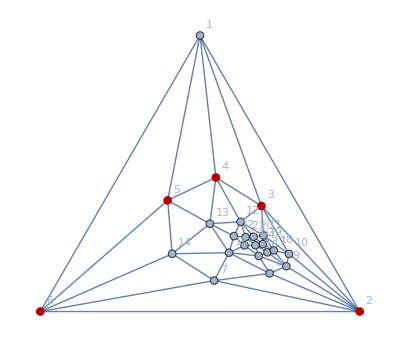

```mathematica
g10000=Graph[plantri[[10000]],GraphLayout->"TutteEmbedding",VertexLabels->"Name",GraphHighlight->{2,6,5,4,3}]
```

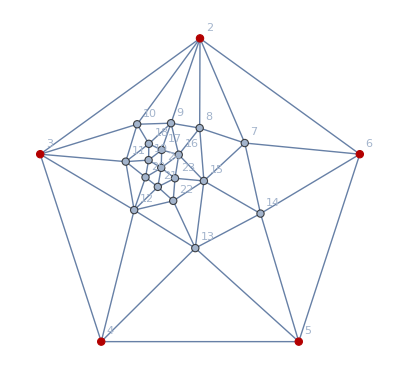

```mathematica
baseGraph=VertexDelete[g10000,1]
```

```mathematica
solsBase=GraphSolutions2[baseGraph];
```

$Aborted

```mathematica
Map[{SymbolToKey[#[[1]]],#[[2]]}&,{x1->1,x2->2,x3->3}]
```

{{1,1},{2,2},{3,3}}

```mathematica
Map[Map[{SymbolToKey[#[[1]]],#[[2]]}&,#]&,Out[428]]
```

{{{1,1},{2,2},{3,3}},{{1,1},{2,2},{3,4}},{{1,1},{2,3},{3,2}},{{1,1},{2,3},{3,4}},{{1,1},{2,4},{3,2}},{{1,1},{2,4},{3,3}},{{1,2},{2,1},{3,3}},{{1,2},{2,1},{3,4}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,4}},{{1,2},{2,4},{3,1}},{{1,2},{2,4},{3,3}},{{1,3},{2,1},{3,2}},{{1,3},{2,1},{3,4}},{{1,3},{2,2},{3,1}},{{1,3},{2,2},{3,4}},{{1,3},{2,4},{3,1}},{{1,3},{2,4},{3,2}},{{1,4},{2,1},{3,2}},{{1,4},{2,1},{3,3}},{{1,4},{2,2},{3,1}},{{1,4},{2,2},{3,3}},{{1,4},{2,3},{3,1}},{{1,4},{2,3},{3,2}}}

```mathematica
ColorTable[g_]:=Block[{sols=GraphSolutions2[g], transformed, same, different,vector, size=VertexCount[g]},
Print["solutions computed"];
Print[sols[[1]]];
transformed= Map[Map[{SymbolToKey[#[[1]]],#[[2]]}&,#]&,sols];
same=Table[0,{i,size},{j,size}];
different=Table[0,{i,size},{j,size}];
Table[
vector=Table[0,{i,size}];
Table[vector[[assignment[[1]] ]]=assignment[[2]],
{assignment,s}
];
Table[If[vector[[i]]==vector[[j]],
same[[i,j]]=same[[i,j]]+1;
same[[j,i]]=same[[j,i]]+1,
different[[i,j]]=different[[i,j]]+1;
different[[j,i]]=different[[j,i]]+1
],{i,Length[vector]},{j,Length[vector]}]
,{s,transformed}];
{MatrixForm[same/24],MatrixForm[different/24]}
]
```

```mathematica
ColorTable[Graph[plantri[[1]]]]
```

solutions computed

{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→1,x10→4,x11→2,x12→3}

{(20 | 0 | 0 | 0 | 0 | 0 | 8 | 8 | 8 | 8 | 8 | 0
0 | 20 | 0 | 8 | 8 | 0 | 0 | 0 | 8 | 0 | 8 | 8
0 | 0 | 20 | 0 | 8 | 8 | 8 | 0 | 0 | 8 | 0 | 8
0 | 8 | 0 | 20 | 0 | 8 | 0 | 8 | 0 | 0 | 8 | 8
0 | 8 | 8 | 0 | 20 | 0 | 8 | 0 | 8 | 0 | 0 | 8
0 | 0 | 8 | 8 | 0 | 20 | 0 | 8 | 0 | 8 | 0 | 8
8 | 0 | 8 | 0 | 8 | 0 | 20 | 0 | 8 | 8 | 0 | 0
8 | 0 | 0 | 8 | 0 | 8 | 0 | 20 | 0 | 8 | 8 | 0
8 | 8 | 0 | 0 | 8 | 0 | 8 | 0 | 20 | 0 | 8 | 0
8 | 0 | 8 | 0 | 0 | 8 | 8 | 8 | 0 | 20 | 0 | 0
8 | 8 | 0 | 8 | 0 | 0 | 0 | 8 | 8 | 0 | 20 | 0
0 | 8 | 8 | 8 | 8 | 8 | 0 | 0 | 0 | 0 | 0 | 20),(0 | 20 | 20 | 20 | 20 | 20 | 12 | 12 | 12 | 12 | 12 | 20
20 | 0 | 20 | 12 | 12 | 20 | 20 | 20 | 12 | 20 | 12 | 12
20 | 20 | 0 | 20 | 12 | 12 | 12 | 20 | 20 | 12 | 20 | 12
20 | 12 | 20 | 0 | 20 | 12 | 20 | 12 | 20 | 20 | 12 | 12
20 | 12 | 12 | 20 | 0 | 20 | 12 | 20 | 12 | 20 | 20 | 12
20 | 20 | 12 | 12 | 20 | 0 | 20 | 12 | 20 | 12 | 20 | 12
12 | 20 | 12 | 20 | 12 | 20 | 0 | 20 | 12 | 12 | 20 | 20
12 | 20 | 20 | 12 | 20 | 12 | 20 | 0 | 20 | 12 | 12 | 20
12 | 12 | 20 | 20 | 12 | 20 | 12 | 20 | 0 | 20 | 12 | 20
12 | 20 | 12 | 20 | 20 | 12 | 12 | 12 | 20 | 0 | 20 | 20
12 | 12 | 20 | 12 | 20 | 20 | 20 | 12 | 12 | 20 | 0 | 20
20 | 12 | 12 | 12 | 12 | 12 | 20 | 20 | 20 | 20 | 20 | 0)}

```mathematica
ColorTable[g10000]
```

$Aborted

```mathematica
problem=EdgeAdd[baseGraph,{3<->1,4<->1,5<->1,6<->1,1<->24,3<->24,2<->24,6<->24}]
```

```mathematica
ColorTable[problem]
```